Last modified:  24, September 39

# (ψ^P)_0 ell,m-mode projector

Builds the first order effective source from a λ^4 puncture in m-modes for a circular orbit

Computes the m-mode effective source from the 4th order puncture 
 for a particle on a circular orbit using comoving coordinates X^μ= (T,X,Y,Z) centered on the particle 
 X_p^μ = (T,0,0,0).  These are related to BL (t,r,θ,ϕ) coordinates by 

 T=((α+ρ_0-2)t-M √ρ_0(α^2-2α+ρ_0)ϕ)/(𝒟 ρ_0)=((a √M+√r_0 (-2 M+r_0)) t 𝒟-√M (a^2+r_0^2-2 a √(M r_0)) 𝒟 ϕ)/(2 a √M+√r0 (-3 M+r0)),

X= (r-M ρ_0)/ℬ=(r-r0)/ℬ,

Y=-Mρ_0 Cos[θ]=-r_0 Cos[θ],

Z= z_c Sin[(ϕ-Ω_p t)/2]=z_c Sin[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]
where 
ρ_0=r_0/M, α=a/(√(M r_0))
and
z_c=2 √(M/r_0)ℬ/(Ω_p 𝒟), ℬ=√((α^2+ρ_0-2)/ρ_0,), 𝒟=√((2α+ρ_0-3)/ρ_0,), Ω_p=1/(√((M α +M ρ_0)ρ_0,))

Note that in the projection we define 
y := cosθ, which is different from y_paper = cos^2 θ
For a=0  the m-modes of the NP components are symmetric under Y->-Y and change imaginary part under m->-m

## Setup

## Globals

```mathematica
ClearAll["Global`*"]
```

```mathematica
HP = 64; (* high precision *)
GP = 16; (* global precision *)
WP = 32; (* working precision *)
MP = 15; (* machine double *)
N64[f_]:=N[f,HP]
N32[f_]:=N[f,WP]
N15[f_]:=N[f,MP]
aSchw = 0;
aKerr = 0;
MKerr= 1;
massval = N64@MKerr;
spinval = N64@aKerr;


(* --- WT params: left and right patches --- *)
r0val = 10*MKerr;
rWTleft=N64[r0val-2MKerr]; (* WT left bdy *)
rTWRight=N64[r0val+2MKerr]; (* WT right bdy*)


mModeval = 2;
mUse=2;
ellMax=15;
```

## Import _s Y_lm (if needed)

```mathematica
Needs["SpinWeightedSpheroidalHarmonics`"]
```

```mathematica
sYlm[s_][l_,m_][θ_,ϕ_]:=SpinWeightedSphericalHarmonicY[s,l,m,θ,ϕ]
```

## Configurations

#### Memory management

```mathematica
ClearAll[heldOwnValueBytes,heldDefinitionBytes,TopGlobalOwnValueMemory,TopGlobalMemory];

SetAttributes[heldOwnValueBytes,HoldFirst];

heldOwnValueBytes[s_Symbol]:=ByteCount[OwnValues[Unevaluated[s]]];

SetAttributes[heldDefinitionBytes,HoldFirst];

heldDefinitionBytes[s_Symbol]:=Total[ByteCount/@{OwnValues[Unevaluated[s]],DownValues[Unevaluated[s]],UpValues[Unevaluated[s]],SubValues[Unevaluated[s]],FormatValues[Unevaluated[s]],NValues[Unevaluated[s]],DefaultValues[Unevaluated[s]],Options[Unevaluated[s]],Messages[Unevaluated[s]]}];

ClearAll[TopGlobalOwnValueMemory];

TopGlobalOwnValueMemory[n_:10,patt_:"Global`*"]:=Module[{names,rows},names=Names[patt];
rows=Table[With[{bytes=ToExpression[name,InputForm,Function[s,heldOwnValueBytes[s],HoldAllComplete]]},{name,bytes,N[bytes/2.^20]}],{name,names}];
rows=Select[rows,#[[2]]>0&];
rows=TakeLargestBy[rows,#[[2]]&,UpTo[n]];
Grid[Prepend[rows/. {name_,bytes_,mib_}:>{name,bytes,NumberForm[mib,{Infinity,3}]},{"Symbol","Bytes","MiB"}],Frame->All,Alignment->Left]];

ClearAll[TopGlobalMemory];

TopGlobalMemory[n_:10,patt_:"Global`*"]:=Module[{names,rows},names=Names[patt];
rows=Table[With[{bytes=ToExpression[name,InputForm,Function[s,heldDefinitionBytes[s],HoldAllComplete]]},{name,bytes,N[bytes/2.^20]}],{name,names}];
rows=Select[rows,#[[2]]>0&];
rows=TakeLargestBy[rows,#[[2]]&,UpTo[n]];
Grid[Prepend[rows/. {name_,bytes_,mib_}:>{name,bytes,NumberForm[mib,{Infinity,3}]},{"Symbol","Bytes","MiB"}],Frame->All,Alignment->Left]];
```

```mathematica
ClearAll[DefinitionMemoryBreakdown];

SetAttributes[DefinitionMemoryBreakdown,HoldFirst];

DefinitionMemoryBreakdown[s_Symbol]:=Grid[{{"OwnValues",ByteCount[OwnValues[Unevaluated[s]]]/2.^20},{"DownValues",ByteCount[DownValues[Unevaluated[s]]]/2.^20},{"SubValues",ByteCount[SubValues[Unevaluated[s]]]/2.^20},{"UpValues",ByteCount[UpValues[Unevaluated[s]]]/2.^20},{"FormatValues",ByteCount[FormatValues[Unevaluated[s]]]/2.^20},{"Options",ByteCount[Options[Unevaluated[s]]]/2.^20}},Frame->All,Alignment->Left]
```

##### Palettes and docked buttons (from Patrick B.)

Below is the full docked buttons code. In the following sections, we explain each part.

Correcting alignment

This docked button will go through the notebook and correctly align all the text.

```mathematica
buttonalignment = With[{styles={"Section","Subsection","Subsubsection"}},
	ToBoxes@Button["align",Map[Set[CurrentValue[#,{CellMargins,1,1}],
CurrentValue[PreviousCell[#,CellStyle->styles],{CellMargins,1,1}]]&,Cells[CellStyle->"Text"]]]];
```

Correctly re-enable evaluation property

This part of the above code creates a docked button that easily allows to deactivate cell evaluation and re - enable it,
	while keeping the texts, outputs,etc default (not evaluable).  Specifically, “re-enable” in fact just sets properties back to default.

```mathematica
buttonevaluable = ToBoxes@Column[Button[StringForm["Evaluable -> ``",#], 
CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}];
```

The below code does the same thing, but it creates a palette instead. Kept it for archive purposes.

```mathematica
CreatePalette@Column[Button[StringForm["Evaluatable -> ``",#],
	CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}]
```

Full docked buttons

Implementation of each part as a docked cell. For adding new features, simply create new data as shown for the above two buttons, i.e. ToBoxes[stuff] and then put it inside the BoxData.
				The next lines should not be touched and their purpose is to make the toolbar expand/collapse upon clicking of the bottom panel.

```mathematica
fullDockedCellsWithCollapseToolbar=Cell[BoxData[{buttonalignment,buttonevaluable}], 
					CellFrameLabelMargins->0,CellFrameLabels->{{None,None},{ButtonBox["",
			
ButtonFunction:>Function[With[{pc=ParentCell@EvaluationCell[]},SetOptions[pc,If[CurrentValue[pc,CellSize]===0,{CellSize->Inherited,CellElementSpacings->{},
				CellFrameMargins->Inherited},{CellSize->0,CellElementSpacings->{"CellMinHeight"->0},CellFrameMargins->0}]]]], ImageSize->{Scaled[2],15},Evaluator->Automatic],None}}];
				SetOptions[EvaluationNotebook[],DockedCells->fullDockedCellsWithCollapseToolbar]
				Clear[buttonalignment,buttonevaluable]
```

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions:>{"WindowClose":>Module[{dy,mn,yr},{dy,mn,yr}=
	   Map[(LinkWrite[First[$FrontEnd],FrontEnd`Value[#]];
     LinkRead[First[$FrontEnd]])&,{"Day","MonthName","Second"}];NotebookLocate["LastModified"];
	     NotebookWrite[InputNotebook[],Cell[TextData[{"Last modified:  ",dy,", ",mn," ",yr}],"Text",CellTags->"LastModified"]]]}]
```

## Preamble

```mathematica
<<xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$DefInfoQ=False;
$CVVerbose=False;
$PrePrint = ScreenDollarIndices;
$CovDFormat="Postfix";
```

```mathematica
SetOptions[ToCanonical,UseMetricOnVBundle->None]
```

{Verbose→False,UseMetricOnVBundle→None,Method→{ChangeCovD,ExpandChristoffel→False},MathLink:>$xpermQ,TimeVerbose→False}

```mathematica
SetOptions[Parallelize,Method->"FinestGrained"]
```

{DistributedContexts:>$Context,Method→FinestGrained,ProgressReporting:>$ProgressReporting}

```mathematica
SetOptions[ParallelMap,Method->"FinestGrained"]
```

{DistributedContexts:>$DistributedContexts,Method→FinestGrained,ProgressReporting:>$ProgressReporting}

```mathematica
org[expr_]:=ToCanonical[ContractMetric[expr,OverDerivatives->True]//CheckZeroDerivative,UseMetricOnVBundle->All]
```

## Manifolds, Coordinates, Metrics

```mathematica
DefManifold[M4,4,{α2,β2,γ2,μ2,ν2,ρ2,υ2,ι2,σ2,ζ2,ξ2,χ2}] (* Kerr spacetime*)
```

#### Constants

```mathematica
DefConstantSymbol[λ]
DefConstantSymbol[m] (* mode number *)
DefConstantSymbol[{a,M}] (* Kerr Mass *)
DefConstantSymbol[r0] (* constant particle radius *)
DefConstantSymbol[{ℬ,𝒟,zc,α,ρ0,Ω}] (* quantities eval'd at the particle *)
```

#### Coordinate Chart

```mathematica
DefChart[CM,M4,{0,1,2,3},{T[],X[],Y[],Z[]},ChartColor->Red] (* local coordinates centered  to the particle *)
```

```mathematica
DefChart[BL,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor->Blue] (* local coordinates centered on the Kerr BH *)
```

```mathematica
OnPart={X[]->0,Y[]->0,Z[]->0}; (* limit to the particle *)
```

```mathematica
(* aux  quantities in the coordinate transformation between X and x *)
myzc = 2(√M)/(√r0)ℬ/(Ω 𝒟)/.r0->ρ0 M//PowerExpand;
𝒟expr  =(√(2α+ρ0-3))/(√ρ0);
ℬexpr = (√(α^2+ρ0-2))/(√ρ0);
Ωexpr=1/(√ρ0 M(α+ρ0));
```

```mathematica
BDzcRules={zc->myzc,ℬ->ℬexpr,𝒟->𝒟expr,Ω->Ωexpr};
```

```mathematica
SchWLimit={α->0,a->0};
BDzcRules$SchWLimit=BDzcRules//.SchWLimit//Simplify;
```

```mathematica
ToVars={r0->M ρ0,a->α √M √r0};
```

```mathematica
$Assumptions={r0,M,a,α,Ω,ℬ,𝒟,zc,R[],X[],Y[],Z[], X,Y,y,zc}∈Reals&&zc>0&&𝒟>0&&ℬ>0&&Ω>0&&ρ0>0&&M>0&&0<a<1&&0<α<1&&R[]>0&&-zc<=Z[]<=zc&&X[]!=0&&-M ρ0<=Y[]<=M ρ0 && X[] ∈ Reals && X ∈ Reals;
```

```mathematica
(* α and ρ0 are dimensionless *)
αρ0Toar0$Rule = {α -> a r0^(-1/2) M^(-1/2) ,ρ0 -> r0/M};
𝒳𝒴𝒵ToXYZ$Rule = {𝒳 ->( ℬ/r0) X[]+1 ,  𝒴 ->Y[]/r0 , 𝒵 -> (ℬ*ρ0^(5/2)*Sqrt[zc^2-Z[]^2])/zc}/.ToVars;
```

```mathematica
zc//.BDzcRules//.αρ0Toar0$Rule
```

(2 M √(-2+a^2/(M r0)+r0/M) (a/(√M √r0)+r0/M))/(√(-3+(2 a)/(√M √r0)+r0/M))

```mathematica
αρToℬ={-2+α^2+ρ0->ℬ^2 ρ0};
αρTo𝒟={(-3+2 α+ρ0)->𝒟^2 ρ0};
apToBD=Join[αρToℬ,αρTo𝒟,{(α+ρ0)->(zc 𝒟)/(2 M ℬ)}];
```

#### Metric functions

```mathematica
metric$InTXYZCoordinates = ({{-(𝒴^4 α^4+𝒳^4 (-1+𝒴^2) ρ0^2+𝒴^2 α^2 ρ0 (2 α+ρ0)-2 𝒳 (𝒴^2 α+ρ0)^2+𝒳^2 ρ0 (𝒴^4 α^2+ρ0 (2 α+ρ0)))/(ρ0 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0)), 0, 0, (ρ0 (-𝒳^4 (-1+𝒴^2) ρ0^2 (-2+α+ρ0)+2 𝒳 (𝒴^2 α+ρ0) (ρ0-α ρ0+𝒴^2 α (-2+α+ρ0))-𝒴^2 α^2 (ρ0 (-α+ρ0)+𝒴^2 α^2 (-2+α+ρ0))-𝒳^2 ρ0 (ρ0 (-α+ρ0)+𝒴^4 α^2 (-2+α+ρ0))))/(𝒵 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0))}, {0, ((-2+α^2+ρ0) (𝒴^2 α^2+𝒳^2 ρ0))/(ρ0 (α^2+𝒳 (-2+𝒳 ρ0))), 0, 0}, {0, 0, (𝒴^2 α^2+𝒳^2 ρ0)/(ρ0-𝒴^2 ρ0), 0}, {(ρ0 (-𝒳^4 (-1+𝒴^2) ρ0^2 (-2+α+ρ0)+2 𝒳 (𝒴^2 α+ρ0) (ρ0-α ρ0+𝒴^2 α (-2+α+ρ0))-𝒴^2 α^2 (ρ0 (-α+ρ0)+𝒴^2 α^2 (-2+α+ρ0))-𝒳^2 ρ0 (ρ0 (-α+ρ0)+𝒴^4 α^2 (-2+α+ρ0))))/(𝒵 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0)), 0, 0, (ρ0^3 (-𝒴^4 α^4 (-2+α+ρ0)^2-𝒳^4 (-1+𝒴^2) ρ0^2 (-2+α+ρ0)^2+2 𝒳 (ρ0-α ρ0+𝒴^2 α (-2+α+ρ0))^2+𝒴^2 (-1+α) α^2 ρ0 (ρ0+α (-4+2 α+ρ0))+𝒳^2 ρ0 (-𝒴^4 α^2 (-2+α+ρ0)^2+(-1+α) ρ0 (ρ0+α (-4+2 α+ρ0)))))/(𝒵^2 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0))}})//.{α^2+ρ0-2->ℬ^2 ρ0,2α+ρ0-3->𝒟^2 ρ0};
```

```mathematica
metricSimp=((metric$InTXYZCoordinates/.𝒳𝒴𝒵ToXYZ$Rule/.ToVars//Simplify//PowerExpand)/.(1-Z[]^2/zc^2)^(n_.):>((zc^2-Z[]^2)^n)/((zc^2)^n)//PowerExpand)//.apToBD//Simplify;
```

```mathematica
metricCM=CTensor[metricSimp,{-CM,-CM}];
```

```mathematica
SetCMetric[metricCM,CM,SignatureOfMetric->{3,1,0}]
```

```mathematica
CDCM=CovDOfMetric[metricCM]; (* Covariant derivative compatible with metricCM on M4  *)
```

#### Chart conversion

```mathematica
TXYZCoordinates = {T[]->((a √M+√r0 (-2 M+r0)) t[] 𝒟-√M (a^2+r0^2-2 a √(M r0)) 𝒟 ϕ[])/(2 a √M+√r0 (-3 M+r0)),X[]->(r[]-r0)/ℬ,Y[]->-r0 Cos[θ[]],Z[]->zc Sin[1/2 (-(√M t[])/(a √M+r0^(3/2))+ϕ[])]};
```

```mathematica
MixedCoordinatesTransform={R[]->√(X[]^2+Y[]^2+Z[]^2),X[]->ℬ^-1(r[]-M ρ0),Y[]->-M ρ0 Cos[θ[]],Zp[]->zc Sin[ϕ[]],Z[]->zc Sin[ϕ[]/2],ℛ[]->√(zc^2+ϱ[]^2),ϱ[]->√(X[]^2+Y[]^2),z[]->(ϱ[]^2+zc^2/2)/(ϱ[] √(ϱ[]^2+zc^2))};
```

```mathematica
ϱℛzToXY={ℛ[]->√(zc^2+ϱ[]^2),ϱ[]->√(X[]^2+Y[]^2),z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))};
ϱℛzToXθ={ℛ[]->√(zc^2+ϱ[]^2),ϱ[]->√(X[]^2+Y[]^2),z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))}//.Y[]->-r0 Cos[θ[]];
zToXY={z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))};
XYtoBL={X[]->(r[]-r0)/ℬ,Y[]->-r0 Cos[θ[]]};
XtoBL=X[]->(r[]-r0)/ℬ;
YtoBL=Y[]->-r0 Cos[θ[]];
ZtoBL=Z[]->zc Sin[1/2 (-(√M t[])/(a √M+r0^(3/2))+ϕ[])];
ztoBL=z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))/.XYtoBL;
```

```mathematica
TrigArgToZ=1/2 (-(√M t[])/(a √M+r0^(3/2))+ϕ[])->ArcSin[Z[]/zc];
```

```mathematica
TovarsTog[f_]:=f//.ToVars/.apToBD//Together
TovarsSimp[f_]:=f//.ToVars/.apToBD//Simplify
```

#### Comoving Tetrad Basis

```mathematica
Map[PDCM[-α2],TXYZCoordinates,{2}]
```

{e |   | 0
α2 |  →((a √M+√r0 (-2 M+r0)) 𝒟 e |   | 0
α2 |  -√M (a^2+r0^2-2 a √(M r0)) 𝒟 e |   | 3
α2 |)/(2 a √M+√r0 (-3 M+r0)),e |   | 1
α2 |  →(e |   | 1
α2 |)/ℬ,e |   | 2
α2 |  →r0 e |   | 2
α2 |   Sin[θ],e |   | 3
α2 |  →1/2 zc (-(√M e |   | 0
α2 |)/(a √M+r0^(3/2))+e |   | 3
α2 |  ) Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}

```mathematica
Map[ToBasis[BL],%,{2}]
```

{e |   | 0
α2 |  →(a √M 𝒟 e |   | 0
α2 |)/(2 a √M+√r0 (-3 M+r0))-(2 M √r0 𝒟 e |   | 0
α2 |)/(2 a √M+√r0 (-3 M+r0))+(r0^(3/2) 𝒟 e |   | 0
α2 |)/(2 a √M+√r0 (-3 M+r0))-(a^2 √M 𝒟 e |   | 3
α2 |)/(2 a √M+√r0 (-3 M+r0))-(√M r0^2 𝒟 e |   | 3
α2 |)/(2 a √M+√r0 (-3 M+r0))+(2 a √M √(M r0) 𝒟 e |   | 3
α2 |)/(2 a √M+√r0 (-3 M+r0)),e |   | 1
α2 |  →(e |   | 1
α2 |)/ℬ,e |   | 2
α2 |  →r0 e |   | 2
α2 |   Sin[θ],e |   | 3
α2 |  →-(√M zc e |   | 0
α2 |   Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])/(2 (a √M+r0^(3/2)))+1/2 zc e |   | 3
α2 |   Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}

```mathematica
%//ComponentArray//Simplify
```

{{e |   | 0
0 |  →((a √M+√r0 (-2 M+r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)),e |   | 0
1 |  →0,e |   | 0
2 |  →0,e |   | 0
3 |  →-(√M (a^2+r0^2-2 a √(M r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0))},{e |   | 1
0 |  →0,e |   | 1
1 |  →1/ℬ,e |   | 1
2 |  →0,e |   | 1
3 |  →0},{e |   | 2
0 |  →0,e |   | 2
1 |  →0,e |   | 2
2 |  →r0 Sin[θ],e |   | 2
3 |  →0},{e |   | 3
0 |  →-(√M zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])/(2 (a √M+r0^(3/2))),e |   | 3
1 |  →0,e |   | 3
2 |  →0,e |   | 3
3 |  →1/2 zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}}

```mathematica
%/.Rule->ComponentValue;
```

#### Coordinate Jacobian

```mathematica
jacobianmatrix=ToValues@ComponentArray@Basis[-{α2,BL},{β2,CM}]
```

{{((a √M+√r0 (-2 M+r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)),0,0,-(√M zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])/(2 (a √M+r0^(3/2)))},{0,1/ℬ,0,0},{0,0,r0 Sin[θ],0},{-(√M (a^2+r0^2-2 a √(M r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)),0,0,1/2 zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}}

```mathematica
jacobianmatrix//MatrixForm
```

(((a √M+√r0 (-2 M+r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)) | 0 | 0 | -(√M zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])/(2 (a √M+r0^(3/2)))
0 | 1/ℬ | 0 | 0
0 | 0 | r0 Sin[θ] | 0
-(√M (a^2+r0^2-2 a √(M r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)) | 0 | 0 | 1/2 zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])

```mathematica
?SetBasisChange
```

```mathematica
SetBasisChange[CTensor[jacobianmatrix,{-BL,CM}],BL]; (* (∂X)/(∂x) indices?? how does this transform from CM to BL, for instance does it transform covariant or contravariant indices? *)
```

## Kinnersley tetrad

#### Transformation and definitions

```mathematica
KerrVals={Σ->r[]^2+a^2 Cos[θ[]]^2,Δ->r[]^2-2M r[]+a^2,ζ->r[]-I a Cos[θ[]],ζb->r[]+I a Cos[θ[]]};
```

```mathematica
BLtoCM={r[]->ℬ X[]+r0,Cos[θ[]]->Y[]/-r0,Sin[θ[]]->PowerExpand[Together[Sin[ArcCos[Y[]/-r0]]]],Csc[θ[]]->1/PowerExpand[Together[Sin[ArcCos[Y[]/-r0]]]],Cos[1/2 (-(√M t)/(a √M+Subscript[r, 0]^(3/2))+ϕ)]->PowerExpand[Together[Cos[ArcSin[Z[]/zc]]]],Cos[1/2 ((√M t)/(a √M+r0^(3/2))-ϕ)]->PowerExpand[Together[Cos[ArcSin[Z[]/zc]]]]};
```

#### BL tetrad legs

```mathematica
lBL=CTensor[(PowerExpand[√((2Σ)/Δ)1/(√(2Δ Σ))]{r[]^2+a^2,Δ,0,a}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
nBL=CTensor[(PowerExpand[(√Δ)/(√(2Σ))1/(√(2Δ Σ))]{r[]^2+a^2,-Δ,0,a}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
mBL=CTensor[((√Σ)/ζb 1/(√(2Σ)){I a Sin[θ[]],0,1,I/Sin[θ[]]}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
mBarBL=CTensor[((√Σ)/ζ 1/(√(2Σ)){-I a Sin[θ[]],0,1,-I/Sin[θ[]]}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
```

```mathematica
BLtoCM
```

{r→r0+ℬ X,Cos[θ]→-Y/r0,Sin[θ]→(√(r0^2-Y^2))/r0,Csc[θ]→r0/(√(r0^2-Y^2)),Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]→(√(zc^2-Z^2))/zc,Cos[1/2 ((√M t)/(a √M+r0^(3/2))-ϕ)]→(√(zc^2-Z^2))/zc}

#### Comoving tetrad Legs

```mathematica
lCM=(ToCTensor[lBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
nCM=(ToCTensor[nBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
mCM=(ToCTensor[mBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
mBarCM=(ToCTensor[mBarBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
```

```mathematica
lCM//Expand
```

CTensor[{(M zc α^2)/(2 ℬ^2 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))-(M^2 α^3)/(ℬ 𝒟 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))+(M zc ρ0)/(2 ℬ^2 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))-(2 M^2 ρ0)/(ℬ 𝒟 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))-(M^2 α ρ0)/(ℬ 𝒟 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))+(zc X)/(ℬ (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))-(4 M X)/(𝒟 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))+(zc X^2)/(2 M ρ0 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))-(2 ℬ X^2)/(𝒟 ρ0 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2)),1/ℬ,0,(M α √(ρ0 (zc-Z) (zc+Z)))/(2 ℬ (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))-(ℬ √(ρ0 (zc-Z) (zc+Z)))/(zc 𝒟 ρ0 (1-(2 M (M ρ0+ℬ X))/(M^2 ρ0 (α^2+ρ0)+2 M ℬ ρ0 X+ℬ^2 X^2)))},{CM},0]

```mathematica
TopGlobalMemory[10]
```

Symbol | Bytes | MiB
CDCM | 847968 | 0.809
names$1061257 | 50952 | 0.049
TangentM4 | 33448 | 0.032
metricCM | 29448 | 0.028
metricSimp | 29168 | 0.028
BL | 19064 | 0.018
CM | 18032 | 0.017
metric$InTXYZCoordinates | 15576 | 0.015
PDBL | 13096 | 0.012
PDCM | 13096 | 0.012

## h^S1 puncture coeffs

### Define Tetrad components

#### Define coefficients

Label indices: (R power, X power, Y power, Z power)

```mathematica
(* coefficients are constant! set the upvalues of the derivatives to zero *)
DefTensor[hS1llc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"ll"]
hS1llc/:PD[___][hS1llc[___]]:=0
hS1llc/:PDCM[___][hS1llc[___]]:=0
DefTensor[hS1lnc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"ln"]
hS1lnc/:PD[___][hS1lnc[___]]:=0
hS1lnc/:PDCM[___][hS1lnc[___]]:=0
DefTensor[hS1nnc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"nn"]
hS1nnc/:PD[___][hS1nnc[___]]:=0
hS1nnc/:PDCM[___][hS1nnc[___]]:=0
DefTensor[hS1lmc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"lm"]
hS1lmc/:PD[___][hS1lmc[___]]:=0
hS1lmc/:PDCM[___][hS1lmc[___]]:=0
DefTensor[hS1lmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"lm†"]
hS1lmbc/:PD[___][hS1lmbc[___]]:=0
hS1lmbc/:PDCM[___][hS1lmbc[___]]:=0
DefTensor[hS1nmc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"nm"]
hS1nmc/:PD[___][hS1nmc[___]]:=0
hS1nmc/:PDCM[___][hS1nmc[___]]:=0
DefTensor[hS1nmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"nm†"]
hS1nmbc/:PD[___][hS1nmbc[___]]:=0
hS1nmbc/:PDCM[___][hS1nmbc[___]]:=0
DefTensor[hS1mmc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"mm"]
hS1mmc/:PD[___][hS1mmc[___]]:=0
hS1mmc/:PDCM[___][hS1mmc[___]]:=0
DefTensor[hS1mmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"mm†"]
hS1mmbc/:PD[___][hS1mmbc[___]]:=0
hS1mmbc/:PDCM[___][hS1mmbc[___]]:=0
DefTensor[hS1mbmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"m†m†"]
hS1mbmbc/:PD[___][hS1mbmbc[___]]:=0
hS1mbmbc/:PDCM[___][hS1mbmbc[___]]:=0
```

### Import h_((a)(b))𝒫 rules, h_((a)(b))𝒫 world tube data, and (ℰ_((a)(b)))^(m,mΩ)[𝒲h𝒫](X,Y) off the particle

```mathematica
(*  hS1data contains the coefficients of rational functions  Subscript[h, (a)(b)]= ∑Subscript[Subscript[c, (a)(b)], npqr] R^n X^p Y^q Z^r   
Label indices:(Rpower,Xpower,Ypower,Zpower) but we've integrated over ϕ to get the m-modes so the Z powers are r=0 *)
```

#### hP rules and data

```mathematica
(* hS1FinalRules, hS1[NP]c, hS1[NP]Final *)
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/Data/mMode_hS_puncture/hS1data.mx"]
(* hS1Zp *)
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/Data/mMode_hS_puncture/hS1Pdata.mx"]  
(* puncture coefficients Subscript[Subscript[c, (a)(b)], npqr] explict rules *)
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/Data/mMode_hS_puncture/hS1TetradRules.mx"]
```

#### Teff rules and data

```mathematica
(*Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/Teffm_CM_XYWindow.mx"] (*  m-mode ℰ[h^(m,𝒫)𝒲(X,Y)] *)*) 

(*Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/EFEs.mx"] (* raw m-mode ℰ[h^(m,𝒫)] *)*)
(*Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/mMode_Teff_ab_NP_comoving_windowed/TabNP_eff_mModes_xCM_XYWindow.mx"] (* m-mode comoving Subscript[ℰ, (a)(b)][h^(m,𝒫)(X,Y)𝒲(X,Y)] w/ bump function window *)*)
```

```mathematica
(* should be fourth order Bump function *)
```

```mathematica
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/Data/mMode_hS_puncture/windowed/PDs_hS1MModes_2ndOrderPuncW.mx"]
```

```mathematica
(*Import["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/Data/mMode_Teff_ab_NP_comoving_windowed/EFEmhS1NP_xCM_XYwindowed_bumpPow4.mx"]*) (* Teff[NP]$MMode$XY functions of X,Y in the WT  *)
```

```mathematica
hSll$MMode$XY[m_][X_,Y_]=hS1llMModesW[m]//.ϱℛzToXY/.X[]->X/.Y[]->Y;
hSln$MMode$XY[m_][X_,Y_]=hS1lnMModesW[m]//.ϱℛzToXY/.X[]->X/.Y[]->Y;
hSlm$MMode$XY[m_][X_,Y_]=hS1lmMModesW[m]//.ϱℛzToXY/.X[]->X/.Y[]->Y;
hSlmb$MMode$XY[m_][X_,Y_]=hS1lmbMModesW[m]//.ϱℛzToXY/.X[]->X/.Y[]->Y;
hSnn$MMode$XY[m_][X_,Y_]=hS1nnMModesW[m]//.ϱℛzToXY/.X[]->X/.Y[]->Y;
hSnm$MMode$XY[m_][X_,Y_]=hS1nmMModesW[m]//.ϱℛzToXY/.X[]->X/.Y[]->Y;
hSnmb$MMode$XY[m_][X_,Y_]=hS1nmbMModesW[m]//.ϱℛzToXY/.X[]->X/.Y[]->Y;
hSmm$MMode$XY[m_][X_,Y_]=hS1mmMModesW[m]//.ϱℛzToXY/.X[]->X/.Y[]->Y;
hSmmb$MMode$XY[m_][X_,Y_]=hS1mmbMModesW[m]//.ϱℛzToXY/.X[]->X/.Y[]->Y;
hSmbmb$MMode$XY[m_][X_,Y_]=hS1mbmbMModesW[m]//.ϱℛzToXY/.X[]->X/.Y[]->Y;
```

#### Check the imports and set hS1FinalRules$Kerr and hS1FinalRules$SchwLimit rules

```mathematica
(* define the Schw.  limit polynomial coefficients *)
tmp=Normal[hS1FinalRules]//.BDzcRules/.SchWLimit;
hS1FinalRules$SchwLimit=Dispatch[tmp];
Clear@tmp;
```

```mathematica
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules$SchwLimit
```

-(5 (α^2-ρ0)^3)/(4 M^3 ℬ^3 𝒟^2 ρ0^6)

5/(4 M^3 (-3+ρ0) (-2+ρ0)^(3/2) √ρ0)

```mathematica
tmp=Normal[hS1FinalRules]//.BDzcRules;
hS1FinalRules$Kerr=Dispatch[tmp];
Clear@tmp;
```

```mathematica
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules$Kerr
```

-(5 (α^2-ρ0)^3)/(4 M^3 ℬ^3 𝒟^2 ρ0^6)

-(5 (α^2-ρ0)^3)/(4 M^3 ρ0^(7/2) (-3+2 α+ρ0) (-2+α^2+ρ0)^(3/2))

## Generate Window functions

### Bump window functions and derivatives

```mathematica
DefScalarFunction[{WX,dWX,ddWX,WY, dWY,ddWY}]
```

```mathematica
ClearAll[logWXp,logWXpp,logWYp,logWYpp,windowFinalRules];

logWXp[x_]:=D[1-1/(1-(ℬ xx/2)^4),xx]/. xx->x;
logWXpp[x_]:=D[1-1/(1-(ℬ xx/2)^4),{xx,2}]/. xx->x;

logWYp[y_]:=D[1-1/(1-(yy/r0)^4),yy]/. yy->y;
logWYpp[y_]:=D[1-1/(1-(yy/r0)^4),{yy,2}]/. yy->y;


ClearAll[windowDerivRules];
windowDerivRules={
HoldPattern[PDCM[a_][PDCM[b_][WX[X[]]]]]:>ddWX[X[]] PDCM[a][X[]] PDCM[b][X[]]+dWX[X[]] PDCM[a][PDCM[b][X[]]],HoldPattern[PDCM[a_][PDCM[b_][WY[Y[]]]]]:>ddWY[Y[]] PDCM[a][Y[]] PDCM[b][Y[]]+dWY[Y[]] PDCM[a][PDCM[b][Y[]]],HoldPattern[PDCM[a_][WX[X[]]]]:>dWX[X[]] PDCM[a][X[]],HoldPattern[PDCM[a_][WY[Y[]]]]:>dWY[Y[]] PDCM[a][Y[]],HoldPattern[PDCM[a_][dWX[X[]]]]:>ddWX[X[]] PDCM[a][X[]],HoldPattern[PDCM[a_][dWY[Y[]]]]:>ddWY[Y[]] PDCM[a][Y[]]};

ClearAll[windowPrimeRules,windowFinalRules];

windowPrimeRules={Derivative[1][WX][x_]:>dWX[x],Derivative[2][WX][x_]:>ddWX[x],Derivative[1][WY][y_]:>dWY[y],Derivative[2][WY][y_]:>ddWY[y],WX'[x_]:>dWX[x],WX''[x_]:>ddWX[x],WY'[y_]:>dWY[y],WY''[y_]:>ddWY[y]};

windowFinalRules={dWX[x_]:>WX[x] logWXp[x],ddWX[x_]:>WX[x] (logWXp[x]^2+logWXpp[x]),dWY[y_]:>WY[y] logWYp[y],ddWY[y_]:>WY[y] (logWYp[y]^2+logWYpp[y]),WX[x_]:>Exp[1-1/(1-(ℬ x/2)^4)],WY[y_]:>Exp[1-1/(1-(y/r0)^4)]};
```

## ψ^P(X,Y) in m-modes

## Mixed coordinate (t,X,Y,ϕ) NP background

#### Mixed tetrad legs

```mathematica
Clear[r0, ℬ, a, M]
```

```mathematica
M=1;
MKerr=1;
massval=1;
```

```mathematica
(* ============================================================*)
(*BL->mixed (t,X,Y,phi) Kinnersley tetrad*)
(* ============================================================*)ClearAll[rMix,yMix,sinThetaMix,SigmaMix,DeltaMix,denMix,lVecMix,nVecMix,mVecMix,mbVecMix];

rMix:=r0+ℬ X;
yMix:=-Y/r0;

sinThetaMix:=Sqrt[1-yMix^2];
SigmaMix:=rMix^2+a^2 yMix^2;
DeltaMix:=rMix^2-2 M rMix+a^2;

(*Standard Kinnersley m-vector denominator.*)
denMix:=rMix+I a yMix;
denBarMix := rMix - I a yMix;
```

```mathematica
ClearAll[lVecMix,nVecMix,mVecMix,mbVecMix];

lVecMix:=<|"t"->(rMix^2+a^2)/DeltaMix,"X"->1/ℬ,"Y"->0,"phi"->a/DeltaMix|>//TovarsSimp;

nVecMix:=<|"t"->(rMix^2+a^2)/(2 SigmaMix),"X"->-DeltaMix/(2 SigmaMix ℬ),"Y"->0,"phi"->a/(2 SigmaMix)|>//TovarsSimp;

mVecMix:=<|"t"->I a sinThetaMix/(Sqrt[2] denMix),"X"->0,"Y"->r0 sinThetaMix/(Sqrt[2] denMix),"phi"->I/(Sqrt[2] denMix sinThetaMix)|>//TovarsSimp;

mbVecMix:=<|"t"->-I a sinThetaMix/(Sqrt[2] denBarMix),"X"->0,"Y"->r0 sinThetaMix/(Sqrt[2] denBarMix),"phi"->-I/(Sqrt[2] denBarMix sinThetaMix)|> //TovarsSimp;
```

#### Define Mixed Metric and Check NP basis orthonormality relations

```mathematica
mbVecMix
```

<|t→-(ⅈ α √(1-Y^2/ρ0^2) √ρ0)/(√2 (X ℬ+(ⅈ Y α)/(√ρ0)+ρ0)),X→0,Y→(√(1-Y^2/ρ0^2) ρ0)/(√2 (X ℬ+(ⅈ Y α)/(√ρ0)+ρ0)),phi→-ⅈ/(√2 √(1-Y^2/ρ0^2) (X ℬ+(ⅈ Y α)/(√ρ0)+ρ0))|>

```mathematica
ClearAll[s2Mix,Aexpr,gBLMostlyPlus,gMixMostlyPlus,jacBLFromMix,gMixExpected,mixAssumptions];

s2Mix:=1-yMix^2;

Aexpr:=(rMix^2+a^2)^2-a^2 DeltaMix s2Mix;

gBLMostlyPlus:={{-(1-2 M rMix/SigmaMix),0,0,-2 M a rMix s2Mix/SigmaMix},{0,SigmaMix/DeltaMix,0,0},{0,0,SigmaMix,0},{-2 M a rMix s2Mix/SigmaMix,0,0,Aexpr s2Mix/SigmaMix}};

jacBLFromMix:={{1,0,0,0},{0,ℬ,0,0},{0,0,1/(r0 sinThetaMix),0},{0,0,0,1}};

gMixMostlyPlus:=Simplify[Transpose[jacBLFromMix].gBLMostlyPlus.jacBLFromMix];

gMixExpected:={{-(1-2 M rMix/SigmaMix),0,0,-2 M a rMix s2Mix/SigmaMix},{0,ℬ^2 SigmaMix/DeltaMix,0,0},{0,0,SigmaMix/(r0^2 s2Mix),0},{-2 M a rMix s2Mix/SigmaMix,0,0,Aexpr s2Mix/SigmaMix}};

mixAssumptions=Element[{X,Y},Reals]&&r0>0&&ℬ>0&&M>0&&-r0<Y<r0&&DeltaMix!=0&&SigmaMix!=0&&s2Mix>0;

metricResidual=FullSimplify[Together[gMixMostlyPlus-gMixExpected],Assumptions->mixAssumptions];

metricResidual//MatrixForm//Simplify
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
detMetricCheck=FullSimplify[Together[Det[gMixMostlyPlus]+ℬ^2 SigmaMix^2/r0^2],Assumptions->mixAssumptions]
```

0

```mathematica
?TovarsSimp
```

```mathematica
ClearAll[vecListMix,dotMix];

vecListMix[v_Association]:={v["t"],v["X"],v["Y"],v["phi"]};

dotMix[u_Association,v_Association]:=Simplify[vecListMix[u].gMixMostlyPlus.vecListMix[v]//.ToVars//TovarsSimp,Assumptions->{r0>0,ℬ>0,M>0,-1<yMix<1}];
```

```mathematica
Clear[basisResiduals, basisResidualsSafe]
```

```mathematica
basisResiduals={dotMix[lVecMix,lVecMix],dotMix[nVecMix,nVecMix],dotMix[mVecMix,mVecMix],dotMix[mbVecMix,mbVecMix],dotMix[lVecMix,nVecMix],dotMix[mVecMix,mbVecMix]};

basisResidualsSafe=Simplify[(Together/@basisResiduals)//.ToVars,Assumptions->mixAssumptions&&denMix!=0&&denBarMix!=0]
```

{0,0,0,0,-1,1}

```mathematica
basisResiduals
```

{0,0,0,0,-1,1}

```mathematica
basisCheckRaw={dotMix[lVecMix,lVecMix],dotMix[nVecMix,nVecMix],dotMix[mVecMix,mVecMix],dotMix[mbVecMix,mbVecMix],dotMix[lVecMix,nVecMix],dotMix[mVecMix,mbVecMix]};

basisCheckNum=Chop[N[basisCheckRaw,50],10^-20]
```

{0,0,0,0,-1.,1.}

```mathematica
basisTargets={0,0,0,0,-1,1};

basisResidualsNum=Chop[N64[basisCheckRaw-basisTargets],10^-20]
```

{0,0,0,0,0,0}

```mathematica
ClearAll[basisTargets,basisResidualsSafe,basisResiduals,detMetricCheck,basisCheckRaw,basisCheckNum,dotMix, vecListMix]
```

```mathematica
Clear[gMixExpected,TorsionPDBL,TrigArgToZ,jacBLFromMix,metricSimp,metricResidual,metricCM]
```

```mathematica
(*ClearAll[CDCM,ChristoffelPDBL,ChristoffelPDBLPDCM,ChristoffelPDCM]*)
```

#### Mixed NP spin coeffs

```mathematica
(* ============================================================*)
(* Kinnersley spin coefficients rewritten in mixed CM/BL coordinates (t,X,Y,ϕ) *)
(* ============================================================*)ClearAll[rhoNP,rhobNP,muNP,mubNP,tauNP,taubNP,piNP,pibNP,betaNP,betabNP,alphaNP,alphabNP,gammaNP,gammabNP,epsNP];

rhoNP:=-1/(rMix-I a yMix)//. ToVars //.apToBD;
rhobNP:=-1/(rMix+I a yMix)//.ToVars//.apToBD;

muNP:=DeltaMix rhoNP^2 rhobNP/2 //.ToVars//.apToBD; 
mubNP:=DeltaMix rhobNP^2 rhoNP/2 //.ToVars//.apToBD;

tauNP:=-I a sinThetaMix rhoNP rhobNP/Sqrt[2]//.ToVars//.apToBD;
taubNP:=I a sinThetaMix rhoNP rhobNP/Sqrt[2]//.ToVars//.apToBD;

piNP:=I a sinThetaMix rhoNP^2/Sqrt[2]//.ToVars//.apToBD;
pibNP:=-I a sinThetaMix rhobNP^2/Sqrt[2]//.ToVars//.apToBD;

betaNP:=-rhobNP yMix/(2 Sqrt[2] sinThetaMix)//.ToVars//.apToBD;
betabNP:=-rhoNP yMix/(2 Sqrt[2] sinThetaMix)//.ToVars//.apToBD;

alphaNP:=(piNP-betabNP)//.ToVars//.apToBD;
alphabNP:=(pibNP-betaNP)//.ToVars//.apToBD;

gammaNP:=(muNP+rhoNP rhobNP (rMix-M)/2)//.ToVars//.apToBD;
gammabNP:=(mubNP+rhoNP rhobNP (rMix-M)/2)//.ToVars//.apToBD;

epsNP:=0 //.ToVars;
epsbNP:=0 //.ToVars;
```

```mathematica
betaNP/.Y->r0
```

-r0/(2 √2 √(1-r0^2/ρ0^2) ρ0 (X ℬ-(ⅈ r0 α)/(√ρ0)+ρ0))

```mathematica
alphaNP//.ToVars//.apToBD//FullSimplify
```

(-ⅈ Y^2 α+2 ⅈ α ρ0^2+Y √ρ0 (X ℬ+ρ0))/(2 √(-(2 Y^2)/ρ0+2 ρ0) (ⅈ Y α+√ρ0 (X ℬ+ρ0))^2)

## Configuration for numerical evaluation (orbit parameters and grid)

```mathematica
(* ============================================================*)
(*Angular variable conventions*)
(* ============================================================*)
(*WARNING:
Here  we use y:=Cos[theta] as the spheroidal-projection variable.
This is NOT the same as the local variable Subscript[y, paper] in  https://arxiv.org/pdf/2404.10082 
or z[] appearing in the X,Y,z construction, e.g. z[]=(X[]^2+Y[]^2+zc^2/2)/(Sqrt[X[]^2+Y[]^2] Sqrt[X[]^2+Y[]^2+zc^2]) 
That z[] is a prolate-type variable and should not be used as Cos[theta] in the spheroidal harmonics.

The mixed coordinate Y is Y=-r0 Cos[theta]=-r0 y, hence y=-Y/r0.

Therefore the spheroidal projection is over little y: T_lm^s(X)=2 Pi Integrate[Conjugate[S_s,l,m[ArcCos[y],0;a omega]] T_s,m[X,-r0 y],{y,-1,1}].

In code: yGrid = Gauss-Legendre nodes for y=Cos[theta], YGrid=-r0 yGrid,SsphY[...] is evaluated on yGrid,TTeuk... is evaluated on YGrid.Note:Some references use y=Cos[theta]^2. That is NOT the convention in this notebook.*)
```

### Set global orbit numerical values

```mathematica
(*--- worldline params: circular orbit ---*)
r0val =N64@10;  (* particle radius 10M *)
ϕ0val=0; (* phi is irrelevant because we can always rotate to put the particle on the north pole *)
θ0val=N64[π/2]; (* equatorial  *)
ρ0val=N64[r0val/MKerr]; (* dimensionless radial particle loc  *)
α0val=N64[aKerr/Sqrt[MKerr*r0val]]; 
to0vals = {r0->r0val,θ0->θ0val,ϕ0->ϕ0val,M->MKerr, a->aKerr,α->α0val,ρ0->ρ0val};

(* --- WT params: left and right patches --- *)
rWTleft=N64[r0val-2]; (* WT left bdy *)
rTWRight=N64[r0val+2]; (* WT right bdy*)

(* --- mode params: test ell,m values --- *)
mUse=2;
ellUse=4;

ϵTiny=N64[1/10^5];

(*-- aux. functions at γ--- *)
𝒟0val = 𝒟//. BDzcRules//.to0vals;
ℬ0val = ℬ //.BDzcRules/.to0vals;
Ω0val = Ω//.BDzcRules /.to0vals;
zc0val = (zc /.BDzcRules /.Ω->Ω0val)//. ℬ -> ℬ0val //. 𝒟-> 𝒟0val //.to0vals;
to0valsAux={𝒟->𝒟0val,ℬ->ℬ0val,Ω->Ω0val,zc->zc0val};

vals==Dataset@(tovals = Join[to0vals,to0valsAux])

(* comoving coords/funcs *)
Xval[R_]:=X[]/.XtoBL/.tovals/.r[]->R
Yval[Θ_]:=Y[]/.YtoBL/.tovals/.θ[]->Θ
zval[R_,Θ_]:=z[]/.ϱℛzToXY/.X[]->Xval[R]/.Y[]->Yval[Θ]/.tovals
X0==Xval[r0val]/.XtoBL/.tovals/.to0vals
Y0==Yval[θ0val]/.YtoBL/.tovals/.to0vals
z0==Limit[zval[r0val,θ],θ->θ0val]/.YtoBL/.tovals/.to0vals
(*ℬ = ℬ/.to0valsAux;*)
```

vals==

X0==0.

Y0==0.

z0==∞

```mathematica
(* test point off the particle *)
Xtest =  N64@Xval[95/100]
Ytest = N64@Yval[π/3]


X0val =
  N64 @ (Xval[r0val] /. tovals /. to0vals);

Y0val =
  N64 @ (Yval[θ0val] /. tovals /. to0vals);

z0val =
  N64 @ (
    Limit[zval[r0val, θ], θ -> θ0val]
      /. YtoBL
      /. tovals
      /. to0vals
    )
```

-10.11820759818654837625151085100902496536879807724215390232581

-5.

∞

```mathematica
spinAudit=Dataset@N64[{"aKerr"->aKerr,"a"->a,"aInTovals"->(a/. tovals),"alphaInTovals"->(α/. tovals),"ℬ"->(ℬ/. tovals),"r0val"->r0val}]
```

#### Source helpers at (x^μ)_p

For a function  f = F(x,y)e^(-iωt+imϕ): v^μ∂_μ f =  [v^t(-ⅈωF)+v^ϕ(ⅈ mF)+ v^X∂_X F+v^Y∂_Y F]e^(-ⅈωt+ⅈmϕ)
Since X=X(r) and Y=Y(θ) , ∂_r F = X_(,r)F_(,x)  and , ∂_θ F = Y_(,θ)F_(,Y)  
with X = (r-r_0)/ℬ  and Y = -r_0cosθ, so X_(,r) = 1/ℬ and Y_(,θ)=r_0 sin(θ)=(r_0^2-Y^2)^(1/2)

```mathematica
ClearAll[XrCoeff,YthetaCoeff,omegaOfM];

XrCoeff:=1/ℬ;

YthetaCoeff:=Sqrt[r0val^2-Y^2];

omegaOfM[m_]:=m Ω0val;
```

## Radial Grid

### Radial grid generation utilities

```mathematica
(* ========================================================================= *)
(* Radial patch grids for the compact-support world-tube window              *)
(*                                                                           *)
(* The radial coordinate used in the source construction is                  *)
(*                                                                           *)
(*     X = (r - r0)/B,                                                       *)
(*                                                                           *)
(* where B is fixed by the background/orbit parameters.  The compact-support *)
(* window, however, is defined by a physical radial half-width Lwin, so that  *)
(*                                                                           *)
(*     W(r) != 0   for   |r - r0| < Lwin,                                   *)
(*     W(r)  = 0   for   |r - r0| >= Lwin.                                  *)
(*                                                                           *)
(* For the window used here, Lwin = 2 M by default.  Thus the world-tube     *)
(* boundaries occur at                                                       *)
(*                                                                           *)
(*     rWTLeft  = r0 - Lwin,                                                 *)
(*     rWTRight = r0 + Lwin,                                                 *)
(*                                                                           *)
(* corresponding approximately to                                           *)
(*                                                                           *)
(*     XWTLeft  = -Lwin/B,                                                   *)
(*     XWTRight =  Lwin/B.                                                   *)
(*                                                                           *)
(* These physical window boundaries, rather than X = +/-1, determine the     *)
(* radial extent of the grid.  A small exterior padding is included beyond   *)
(* each boundary so that the compact-support region W = 0 is explicitly      *)
(* represented in the numerical data and plots.                              *)
(*                                                                           *)
(* The grid is split at the world-tube boundaries.  This is useful for       *)
(* spectral calculations because the piecewise transition to W = 0 occurs    *)
(* at a Chebyshev-Lobatto patch endpoint rather than in the interior of a     *)
(* spectral patch.                                                           *)
(*                                                                           *)
(* makeRadialPatchGrids:                                                     *)
(*   Basic construction with one world-tube patch and one exterior patch     *)
(*   on each side of the particle.                                           *)
(*                                                                           *)
(* makeRadialPatchGridsRefined:                                              *)
(*   Refined construction which additionally splits each world-tube side     *)
(*   into an inner patch near the particle and an outer patch extending to   *)
(*   the compact-support boundary.                                           *)
(*                                                                           *)
(* Common options:                                                           *)
(*                                                                           *)
(*   "EpsilonX"          : excludes a small interval around X = X0, avoiding *)
(*                         direct evaluation at the particle.                 *)
(*                                                                           *)
(*   "WindowHalfWidthR"  : physical radial half-width Lwin of the compact    *)
(*                         support; default is 2 M (2.0 in M = 1 units).      *)
(*                                                                           *)
(*   "ExteriorPaddingR"  : physical radial extent included outside the       *)
(*                         world tube, where W is identically zero.           *)
(*                                                                           *)
(*   "NExterior"         : number of Chebyshev-Lobatto points used in each   *)
(*                         exterior zero-window patch.                        *)
(*                                                                           *)
(* The refined builder additionally uses                                    *)
(*                                                                           *)
(*   "InnerHalfWidth"    : half-width in X of the high-resolution region     *)
(*                         immediately adjacent to the particle.              *)
(*                                                                           *)
(* Both builders return the world-tube boundaries, exterior-domain           *)
(* boundaries, individual patch grids, and joined left/right grids in a      *)
(* common Association format.                                                *)
(* ========================================================================= *
```

```mathematica
(* ============================================================*)
(*Grid generation utilities*)
(* ============================================================*)
ClearAll[affineChebLobattoGrid];
(* cheby grid constructor *)
affineChebLobattoGrid[n_Integer,{xmin_,xmax_}]:=Module[{j,xi,x},
xi=Table[Cos[Pi j/(n-1)],{j,0,n-1}];
x=(xmin+xmax)/2+(xmax-xmin) xi/2;
Sort[N64/@x]];
```

#### old builders

```mathematica
(*ClearAll[makeRadialPatchGrids]

Options[makeRadialPatchGrids]={"EpsilonX"->ϵTiny};

makeRadialPatchGrids[nLeft_Integer,nRight_Integer,OptionsPattern[]]:=Module[{epsX,rLeftPhys,rRightPhys,xLeftOuter,xRightOuter,x0,xLeftGrid,xRightGrid},
epsX=OptionValue["EpsilonX"];
x0=X0val;
(* physical grid *)
rLeftPhys=r0val-ℬ0val;
rRightPhys=r0val+ℬ0val;
xLeftOuter=N64@(Xval[rLeftPhys]/. tovals/. to0vals);
xRightOuter=N64@(Xval[rRightPhys]/. tovals/. to0vals);
xLeftGrid=affineChebLobattoGrid[nLeft,{xLeftOuter,x0-epsX}];
xRightGrid=affineChebLobattoGrid[nRight,{x0+epsX,xRightOuter}];
<|
"X0"->x0,
"XLeftOuter"->xLeftOuter,
"XRightOuter"->xRightOuter,
"XLeftGrid"->xLeftGrid,
"XRightGrid"->xRightGrid
|>]; *)
```

```mathematica
(* refined version to add more points near the particle *)
```

```mathematica
(*ClearAll[makeRadialPatchGridsRefined];

Options[makeRadialPatchGridsRefined]={"EpsilonX"->ϵTiny,"InnerHalfWidth"->0.01};

makeRadialPatchGridsRefined[nLeftOuter_Integer,nLeftInner_Integer,nRightInner_Integer,nRightOuter_Integer,OptionsPattern[]]:=Module[{epsX,dxInner,x0,rLeftPhys,rRightPhys,xLeftOuter,xRightOuter,xLO,xLI,xRI,xRO},epsX=OptionValue["EpsilonX"];
dxInner=OptionValue["InnerHalfWidth"];
x0=X0val;
rLeftPhys=r0val-ℬ0val;
rRightPhys=r0val+ℬ0val;
xLeftOuter=N64@(Xval[rLeftPhys]/. tovals/. to0vals);
xRightOuter=N64@(Xval[rRightPhys]/. tovals/. to0vals);
xLO=affineChebLobattoGrid[nLeftOuter,{xLeftOuter,x0-dxInner}];
xLI=affineChebLobattoGrid[nLeftInner,{x0-dxInner,x0-epsX}];
xRI=affineChebLobattoGrid[nRightInner,{x0+epsX,x0+dxInner}];
xRO=affineChebLobattoGrid[nRightOuter,{x0+dxInner,xRightOuter}];
<|"X0"->x0,"XLeftOuter"->xLeftOuter,"XRightOuter"->xRightOuter,"XLeftOuterGrid"->xLO,"XLeftInnerGrid"->xLI,"XRightInnerGrid"->xRI,"XRightOuterGrid"->xRO,"XLeftGrid"->Join[Most[xLO],xLI],"XRightGrid"->Join[xRI,Rest[xRO]]|>]*)
```

#### new builders

```mathematica
ClearAll[makeRadialPatchGrids];

Options[makeRadialPatchGrids]={"EpsilonX"->ϵTiny,(*compact-support half-width in physical r*)"WindowHalfWidthR"->2.0,(*amount of physical r included outside the world tube*)"ExteriorPaddingR"->0.1,(*points in each exterior W=0 patch*)"NExterior"->2};

makeRadialPatchGrids[nLeft_Integer,nRight_Integer,OptionsPattern[]]:=Module[{epsX,Lwin,padR,nExt,x0,rWTLeft,rWTRight,rDomainLeft,rDomainRight,xWTLeft,xWTRight,xDomainLeft,xDomainRight,xLeftExteriorGrid,xLeftWTGrid,xRightWTGrid,xRightExteriorGrid,xLeftGrid,xRightGrid},epsX=OptionValue["EpsilonX"];
Lwin=OptionValue["WindowHalfWidthR"];
padR=OptionValue["ExteriorPaddingR"];
nExt=OptionValue["NExterior"];
x0=X0val;
(* ========================================================*)(*Physical compact-support boundaries*)(* ========================================================*)rWTLeft=r0val-Lwin;
rWTRight=r0val+Lwin;
(*extend beyond support so W=0 is actually represented*)rDomainLeft=rWTLeft-padR;
rDomainRight=rWTRight+padR;
(* ========================================================*)(*Convert physical r boundaries to X*)(* ========================================================*)xWTLeft=N64@(Xval[rWTLeft]/. tovals/. to0vals);
xWTRight=N64@(Xval[rWTRight]/. tovals/. to0vals);
xDomainLeft=N64@(Xval[rDomainLeft]/. tovals/. to0vals);
xDomainRight=N64@(Xval[rDomainRight]/. tovals/. to0vals);
(* ========================================================*)(*Four Chebyshev-Lobatto patches*)(**)(*zero|WT-left||particle||WT-right|zero*)(* ========================================================*)xLeftExteriorGrid=affineChebLobattoGrid[nExt,{xDomainLeft,xWTLeft}];
xLeftWTGrid=affineChebLobattoGrid[nLeft,{xWTLeft,x0-epsX}];
xRightWTGrid=affineChebLobattoGrid[nRight,{x0+epsX,xWTRight}];
xRightExteriorGrid=affineChebLobattoGrid[nExt,{xWTRight,xDomainRight}];
(*Avoid duplicating WT boundary Lobatto points*)xLeftGrid=Join[Most[xLeftExteriorGrid],xLeftWTGrid];
xRightGrid=Join[xRightWTGrid,Rest[xRightExteriorGrid]];
<|"X0"->x0,(*compact-support boundaries*)"XWTLeft"->xWTLeft,"XWTRight"->xWTRight,(*outer plotting/computational boundaries*)"XDomainLeft"->xDomainLeft,"XDomainRight"->xDomainRight,(*individual patches*)"XLeftExteriorGrid"->xLeftExteriorGrid,"XLeftWTGrid"->xLeftWTGrid,"XRightWTGrid"->xRightWTGrid,"XRightExteriorGrid"->xRightExteriorGrid,(*backwards-compatible joined grids*)"XLeftGrid"->xLeftGrid,"XRightGrid"->xRightGrid,(*useful physical metadata*)"RWTLeft"->rWTLeft,"RWTRight"->rWTRight,"WindowHalfWidthR"->Lwin,"ExteriorPaddingR"->padR|>];
```

```mathematica
ClearAll[makeRadialPatchGridsRefined];

Options[makeRadialPatchGridsRefined]={"EpsilonX"->ϵTiny,"InnerHalfWidth"->0.01,
(*physical r-width of compact support*)"WindowHalfWidthR"->2.0,(*physical r-region outside support,for showing W=0*)"ExteriorPaddingR"->0.1,(*number of points in each exterior zero patch*)"NExterior"->2};

makeRadialPatchGridsRefined[nLeftOuter_Integer,nLeftInner_Integer,nRightInner_Integer,nRightOuter_Integer,OptionsPattern[]]:=Module[{epsX,dxInner,Lwin,padR,nExt,x0,rWTLeft,rWTRight,rDomainLeft,rDomainRight,xWTLeft,xWTRight,xDomainLeft,xDomainRight,xLE,xLO,xLI,xRI,xRO,xRE,xLeft,xRight,xFull},epsX=OptionValue["EpsilonX"];
dxInner=OptionValue["InnerHalfWidth"];
Lwin=OptionValue["WindowHalfWidthR"];
padR=OptionValue["ExteriorPaddingR"];
nExt=OptionValue["NExterior"];
x0=X0val;
(*--------------------------------------------------------*)
(*Compact-support boundaries in physical r*)(*--------------------------------------------------------*)
rWTLeft=r0val-Lwin;
rWTRight=r0val+Lwin;
(*Extend a little outside the WT so that W=0 is visible*)
rDomainLeft=rWTLeft-padR;
rDomainRight=rWTRight+padR;
(*Convert all physical boundaries to X*)xWTLeft=N64@(Xval[rWTLeft]/. tovals/. to0vals);
xWTRight=N64@(Xval[rWTRight]/. tovals/. to0vals);
xDomainLeft=N64@(Xval[rDomainLeft]/. tovals/. to0vals);
xDomainRight=N64@(Xval[rDomainRight]/. tovals/. to0vals);
(*--------------------------------------------------------*)(*Six patches*)(**)(*exterior|outer|inner||inner|outer|exterior*)(*--------------------------------------------------------*)xLE=affineChebLobattoGrid[nExt,{xDomainLeft,xWTLeft}];
xLO=affineChebLobattoGrid[nLeftOuter,{xWTLeft,x0-dxInner}];
xLI=affineChebLobattoGrid[nLeftInner,{x0-dxInner,x0-epsX}];
xRI=affineChebLobattoGrid[nRightInner,{x0+epsX,x0+dxInner}];
xRO=affineChebLobattoGrid[nRightOuter,{x0+dxInner,xWTRight}];
xRE=affineChebLobattoGrid[nExt,{xWTRight,xDomainRight}];
(*Remove duplicated Lobatto endpoints when joining*)xLeft=Join[Most[xLE],Most[xLO],xLI];
xRight=Join[xRI,Rest[xRO],Rest[xRE]];
xFull=Join[xLeft,xRight];
<|"X0"->x0,(*world-tube/support boundaries*)"XWTLeft"->xWTLeft,"XWTRight"->xWTRight,(*full plotting/computational domain*)"XDomainLeft"->xDomainLeft,"XDomainRight"->xDomainRight,(*individual patches*)"XLeftExteriorGrid"->xLE,"XLeftOuterGrid"->xLO,"XLeftInnerGrid"->xLI,"XRightInnerGrid"->xRI,"XRightOuterGrid"->xRO,"XRightExteriorGrid"->xRE,(*joined grids*)"XLeftGrid"->xLeft,"XRightGrid"->xRight,"XFullGrid"->xFull,(*useful physical metadata*)"RWTLeft"->rWTLeft,"RWTRight"->rWTRight,"WindowHalfWidthR"->Lwin|>];
```

#### diagnostic utils

```mathematica
ClearAll[radialSourceResolutionReportPatches];

radialSourceResolutionReportPatches[xLeftGrid_,xRightGrid_,x0_:0]:=Module[{dL,dR,radii},dL=Sort[Abs[xLeftGrid-x0]];
dR=Sort[Abs[xRightGrid-x0]];
radii={10^-4,2 10^-4,5 10^-4,10^-3,2 10^-3,5 10^-3,10^-2,2 10^-2,5 10^-2,10^-1};
<|"nearest left distances"->Take[dL,UpTo[12]],"nearest right distances"->Take[dR,UpTo[12]],"counts within radius"->Dataset@Table[<|"radius"->r,"left count"->Count[dL,_?(#<=r&)],"right count"->Count[dR,_?(#<=r&)]|>,{r,radii}]|>];
```

```mathematica
ClearAll[radialSourceResolutionReport];

Options[radialSourceResolutionReport]={"Radii"->{10^-4,2 10^-4,5 10^-4,10^-3,2 10^-3,5 10^-3,10^-2,2 10^-2,5 10^-2,10^-1},"NNearest"->12,"NEdgeNearest"->8};


radialSourceResolutionReport[grids_Association,OptionsPattern[]]:=Module[{x0,xWTLeft,xWTRight,xLeftWT,xRightWT,dL,dR,dEdgeL,dEdgeR,radii,nNearest,nEdgeNearest},radii=OptionValue["Radii"];
nNearest=OptionValue["NNearest"];
nEdgeNearest=OptionValue["NEdgeNearest"];
x0=grids["X0"];
xWTLeft=grids["XWTLeft"];
xWTRight=grids["XWTRight"];
(*---------------------------------------------------------*)(*Restrict joined grids to the nonzero-window world tube*)(*---------------------------------------------------------*)xLeftWT=Select[grids["XLeftGrid"],xWTLeft<=#<=x0&];
xRightWT=Select[grids["XRightGrid"],x0<=#<=xWTRight&];
(*---------------------------------------------------------*)(*Distances from the particle*)(*---------------------------------------------------------*)dL=Sort[Abs[xLeftWT-x0]];
dR=Sort[Abs[xRightWT-x0]];
(*---------------------------------------------------------*)(*Distances from the compact-support boundaries*)(**)(*Remove the zero distance corresponding to the Lobatto*)(*endpoint lying exactly at the WT boundary.*)(*---------------------------------------------------------*)dEdgeL=Select[Sort[Abs[xLeftWT-xWTLeft]],#>0&];
dEdgeR=Select[Sort[Abs[xRightWT-xWTRight]],#>0&];
<|"world-tube X range"->{xWTLeft,xWTRight},"world-tube point counts"-><|"left"->Length[xLeftWT],"right"->Length[xRightWT]|>,"particle resolution"-><|"nearest left distances"->Take[dL,UpTo[nNearest]],"nearest right distances"->Take[dR,UpTo[nNearest]],"counts within radius"->Dataset@Table[<|"radius"->r,"left count"->Count[dL,_?(#<=r&)],"right count"->Count[dR,_?(#<=r&)]|>,{r,radii}]|>,"window-edge resolution"-><|"nearest left-edge spacings"->Take[dEdgeL,UpTo[nEdgeNearest]],"nearest right-edge spacings"->Take[dEdgeR,UpTo[nEdgeNearest]]|>|>];
```

### Build Radial grid

#### Test grid

```mathematica
ClearAll[NleftTest,NrightTest];

NleftTest=32;
NrightTest=32;

radialGridsTest=makeRadialPatchGrids[NleftTest,NrightTest,"EpsilonX"->ϵTiny,"WindowHalfWidthR"->2.0,"ExteriorPaddingR"->0.5,"NExterior"->12];

XLeftGridTest=radialGridsTest["XLeftGrid"];
XRightGridTest=radialGridsTest["XRightGrid"];
```

```mathematica
radialSourceResolutionReport[radialGridsTest]
```

<|world-tube X range→{-2.23607,2.23607},world-tube point counts→<|left→32,right→32|>,particle resolution→<|nearest left distances→{0.00001,0.00574625,0.0228961,0.0512836,0.0906175,0.140494,0.200402,0.269725,0.347754,0.433687,0.526642,0.625666},nearest right distances→{0.00001,0.00574625,0.0228961,0.0512836,0.0906175,0.140494,0.200402,0.269725,0.347754,0.433687,0.526642,0.625666},counts within radius→|>,window-edge resolution→<|nearest left-edge spacings→{0.00573625,0.0228861,0.0512736,0.0906075,0.140484,0.200392,0.269715,0.347744},nearest right-edge spacings→{0.00573625,0.0228861,0.0512736,0.0906075,0.140484,0.200392,0.269715,0.347744}|>|>

```mathematica
(* ClearAll[NleftTest,NrightTest]
NleftTest= 32; (*test *)
NrightTest= 32; (* test*)
radialGridsTest=makeRadialPatchGrids[NleftTest,NrightTest,"EpsilonX"->ϵTiny];


XLeftGridTest=radialGridsTest["XLeftGrid"];
XRightGridTest=radialGridsTest["XRightGrid"]; *)
```

#### Production grid

```mathematica
(* =============================================================*)
(*Production radial grid*)(**)(*128 points per world-tube side,plus exterior zero-window*)(*patches used to display/represent compact support.*)
(* =============================================================*)
nXLeft=128;
nXRight=128;

radialGrids=makeRadialPatchGrids[nXLeft,nXRight,"EpsilonX"->ϵTiny,"WindowHalfWidthR"->2.0,"ExteriorPaddingR"->0.5,"NExterior"->24];

XLeftGrid=radialGrids["XLeftGrid"];
XRightGrid=radialGrids["XRightGrid"];
```

```mathematica
radialSourceResolutionReport[radialGrids]
```

<|world-tube X range→{-2.23607,2.23607},world-tube point counts→<|left→128,right→128|>,particle resolution→<|nearest left distances→{0.00001,0.000352053,0.001378,0.00308722,0.00547866,0.00855086,0.0123019,0.0167296,0.0218311,0.0276034,0.034043,0.0411458},nearest right distances→{0.00001,0.000352053,0.001378,0.00308722,0.00547866,0.00855086,0.0123019,0.0167296,0.0218311,0.0276034,0.034043,0.0411458},counts within radius→|>,window-edge resolution→<|nearest left-edge spacings→{0.000342053,0.001368,0.00307722,0.00546866,0.00854086,0.0122919,0.0167196,0.0218211},nearest right-edge spacings→{0.000342053,0.001368,0.00307722,0.00546866,0.00854086,0.0122919,0.0167196,0.0218211}|>|>

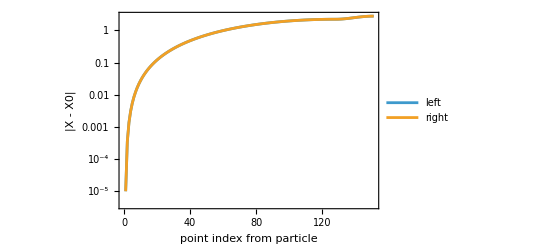

```mathematica
dL=Sort[Abs[XLeftGrid-X0val]];
dR=Sort[Abs[XRightGrid-X0val]];

ListLogPlot[{Transpose[{Range[Length[dL]],dL}],Transpose[{Range[Length[dR]],dR}]},Joined->True,Frame->True,FrameLabel->{"point index from particle","|X - X0|"},PlotLegends->{"left","right"}]
```

```mathematica
Clear[dL,dR]
```

```mathematica
(* ============================================================*)
(*Production radial grids:128 points per side*)
(* ============================================================*)
(*nXLeft=128;
nXRight=128;

radialGrids=makeRadialPatchGrids[nXLeft,nXRight,"EpsilonX"->ϵTiny];

XLeftGrid=radialGrids["XLeftGrid"];
XRightGrid=radialGrids["XRightGrid"];
radialSourceResolutionReport[XLeftGrid,XRightGrid,X0val]*)
```

#### refined production grid

```mathematica
radialGridsRefined=makeRadialPatchGridsRefined[48,96,96,48,"EpsilonX"->ϵTiny,"InnerHalfWidth"->0.01,"WindowHalfWidthR"->2.0,"ExteriorPaddingR"->0.5,"NExterior"->24];

XLeftGridProd=radialGridsRefined["XLeftGrid"];
XRightGridProd=radialGridsRefined["XRightGrid"];
```

```mathematica
(*radialGridsRefined=makeRadialPatchGridsRefined[48,96,96,48,"EpsilonX"->ϵTiny,"InnerHalfWidth"->0.01];

XLeftGridProd=radialGridsRefined["XLeftGrid"];
XRightGridProd=radialGridsRefined["XRightGrid"];*)radialSourceResolutionReportPatches[radialGridsRefined["XLeftInnerGrid"],radialGridsRefined["XRightInnerGrid"],X0val]
```

<|nearest left distances→{0.00001,0.000012731,0.0000209209,0.0000345609,0.000053636,0.0000781253,0.000108002,0.000143234,0.000183781,0.000229601,0.000280643,0.00033685},nearest right distances→{0.00001,0.000012731,0.0000209209,0.0000345609,0.000053636,0.0000781253,0.000108002,0.000143234,0.000183781,0.000229601,0.000280643,0.00033685},counts within radius→|>

```mathematica
radialSourceResolutionReport[radialGridsRefined]
```

<|world-tube X range→{-2.23607,2.23607},world-tube point counts→<|left→143,right→143|>,particle resolution→<|nearest left distances→{0.00001,0.000012731,0.0000209209,0.0000345609,0.000053636,0.0000781253,0.000108002,0.000143234,0.000183781,0.000229601,0.000280643,0.00033685},nearest right distances→{0.00001,0.000012731,0.0000209209,0.0000345609,0.000053636,0.0000781253,0.000108002,0.000143234,0.000183781,0.000229601,0.000280643,0.00033685},counts within radius→|>,window-edge resolution→<|nearest left-edge spacings→{0.00248554,0.00993106,0.0223033,0.039547,0.0615852,0.0883194,0.11963,0.155378},nearest right-edge spacings→{0.00248554,0.00993106,0.0223033,0.039547,0.0615852,0.0883194,0.11963,0.155378}|>|>

## Angular Grid

### Parameters

```mathematica
NYgrid = 128;
```

### Affine Chebychev-Lobatto Utils

```mathematica
(* ClearAll[makeAngularYGrid];

Options[makeAngularYGrid]={"EpsilonZ"->ϵTiny};

makeAngularYGrid[nY_Integer,OptionsPattern[]]:=
Module[
{epsZ,zGridRaw,thetaGridRaw,yGridRaw,yzPairs},
epsZ=OptionValue["EpsilonZ"];
zGridRaw=
affineChebLobattoGrid[
nY,
{-1+epsZ,1-epsZ}
];
thetaGridRaw=ArcCos/@zGridRaw;
yGridRaw=N64/@((Yval[#]/. tovals/. to0vals)&/@thetaGridRaw);
(*Sort by Y,because ListInterpolation wants increasing coordinate lists.*)yzPairs=SortBy[Transpose[{yGridRaw,zGridRaw,thetaGridRaw}],First];
<|
"YGrid"->yzPairs[[All,1]],
"ZOnYGrid"->yzPairs[[All,2]],
"ThetaOnYGrid"->yzPairs[[All,3]]
|>
];*)
```

```mathematica
ClearAll[makeAngularYGrid];

Options[makeAngularYGrid]={"EpsilonY"->ϵTiny,"EpsilonZ"->ϵTiny};

makeAngularYGrid[nYLeft_Integer,nYRight_Integer,OptionsPattern[]]:=Module[{epsY,epsZ,r0,yNorth,ySouth,yLeftGrid,yRightGrid,zLeftGrid,zRightGrid,thetaLeftGrid,thetaRightGrid},epsY=OptionValue["EpsilonY"];
epsZ=OptionValue["EpsilonZ"];
r0=N64@r0val;
(*---------------------------------------------------------*)
(*Y=-r0 Cos[theta]*)
(**)
(*north pole:z=+1,Y=-r0*)
(*particle:z=0,Y=0*)
(*south pole:z=-1,Y=+r0*)
(**)
(*epsY excludes the particle at Y=0.*)
(*epsZ optionally keeps the grid slightly away from the*)
(*angular poles,where logarithmic window derivatives can*)
(*be singular even though the full window vanishes.*)
(*---------------------------------------------------------*)
yNorth=-r0 (1-epsZ);
ySouth=r0 (1-epsZ);
(*Left/north side:Y<0*)yLeftGrid=affineChebLobattoGrid[nYLeft,{yNorth,-epsY}];
(*Right/south side:Y>0*)yRightGrid=affineChebLobattoGrid[nYRight,{epsY,ySouth}];
(*Convert back to z=Cos[theta]*)zLeftGrid=-yLeftGrid/r0;
zRightGrid=-yRightGrid/r0;
thetaLeftGrid=ArcCos/@zLeftGrid;
thetaRightGrid=ArcCos/@zRightGrid;
<|"Y0"->0.,"YNorth"->yNorth,"YSouth"->ySouth,"YLeftGrid"->yLeftGrid,"YRightGrid"->yRightGrid,"YGrid"->Join[yLeftGrid,yRightGrid],"ZLeftGrid"->zLeftGrid,"ZRightGrid"->zRightGrid,"ZOnYGrid"->Join[zLeftGrid,zRightGrid],"ThetaLeftGrid"->thetaLeftGrid,"ThetaRightGrid"->thetaRightGrid,"ThetaOnYGrid"->Join[thetaLeftGrid,thetaRightGrid]|>];
```

### Build Y grid

```mathematica
angularGrid=makeAngularYGrid[96,96,"EpsilonY"->ϵTiny];
```

```mathematica
YGrid=angularGrid["YGrid"];
YLeftGrid=angularGrid["YLeftGrid"];
YRightGrid=angularGrid["YRightGrid"];
ZOnYGrid=angularGrid["ZOnYGrid"];
ThetaOnYGrid=angularGrid["ThetaOnYGrid"];
```

```mathematica
{Min[YGrid],Max[YGrid],Min[ZOnYGrid],Max[ZOnYGrid]}
```

{-9.9999,9.9999,-0.99999,0.99999}

## Grid Patches

```mathematica
ClearAll[makePatch];

makePatch[name_String,xGrid_,yGrid_,zGrid_,thetaGrid_,xSide_Integer,ySide_Integer]:=<|"Name"->name,"XGrid"->xGrid,"YGrid"->yGrid,"ZOnYGrid"->zGrid,"ThetaOnYGrid"->thetaGrid,(*Radial side of the particle*)"XSide"->xSide,(*Angular/Y side of the particle*)"YSide"->ySide|>;
```

```mathematica
patchLL=makePatch["LeftLeft",XLeftGrid,YLeftGrid,angularGrid["ZLeftGrid"],angularGrid["ThetaLeftGrid"],-1,-1];

patchLR=makePatch["LeftRight",XLeftGrid,YRightGrid,angularGrid["ZRightGrid"],angularGrid["ThetaRightGrid"],-1,+1];

patchRL=makePatch["RightLeft",XRightGrid,YLeftGrid,angularGrid["ZLeftGrid"],angularGrid["ThetaLeftGrid"],+1,-1];

patchRR=makePatch["RightRight",XRightGrid,YRightGrid,angularGrid["ZRightGrid"],angularGrid["ThetaRightGrid"],+1,+1];
```

```mathematica
patchLLprod=makePatch["LeftLeft",XLeftGridProd,YLeftGrid,angularGrid["ZLeftGrid"],angularGrid["ThetaLeftGrid"],-1,-1];

patchLRprod=makePatch["LeftRight",XLeftGridProd,YRightGrid,angularGrid["ZRightGrid"],angularGrid["ThetaRightGrid"],-1,+1];

patchRLprod=makePatch["RightLeft",XRightGridProd,YLeftGrid,angularGrid["ZLeftGrid"],angularGrid["ThetaLeftGrid"],+1,-1];

patchRRprod=makePatch["RightRight",XRightGridProd,YRightGrid,angularGrid["ZRightGrid"],angularGrid["ThetaRightGrid"],+1,+1];
```

```mathematica
patchAssoc=<|"LL"->patchLL,"LR"->patchLR,"RL"->patchRL,"RR"->patchRR|>;
```

```mathematica
patchAssocProd=<|"LL"->patchLLprod,"LR"->patchLRprod,"RL"->patchRLprod,"RR"->patchRRprod|>;
```

```mathematica
patchLeft=
<|
"Name"->"Left",
"XGrid"->XLeftGrid,
"YGrid"->YGrid,
"ZOnYGrid"->ZOnYGrid,
"ThetaOnYGrid"->ThetaOnYGrid,
"Side"->-1
|>;

patchRight=
<|
"Name"->"Right",
"XGrid"->XRightGrid,
"YGrid"->YGrid,
"ZOnYGrid"->ZOnYGrid,
"ThetaOnYGrid"->ThetaOnYGrid,
"Side"->+1
|>;
```

```mathematica
patchLeftProd=
<|"Name"->"Left",
"XGrid"->XLeftGridProd,
"YGrid"->YGrid,
"ZOnYGrid"->ZOnYGrid,
"ThetaOnYGrid"->ThetaOnYGrid,
"Side"->-
1|>;

patchRightProd=
<|"Name"->"Right",
"XGrid"->XRightGridProd,
"YGrid"->YGrid,
"ZOnYGrid"->ZOnYGrid,
"ThetaOnYGrid"->ThetaOnYGrid,
"Side"->+1
|>;
```

```mathematica
{Length[patchLeftProd["XGrid"]],Length[patchRightProd["XGrid"]],MinMax[patchLeftProd["XGrid"]],MinMax[patchRightProd["XGrid"]]}
```

{166,166,{-2.79508,-0.00001},{0.00001,2.79508}}

### Grid Samplers

```mathematica
(* Sampler over the grid *)
```

```mathematica
sampleComponentGrid[f_,patch_Association]:=
Table[
f[X,Y],
{X,patch["XGrid"]},
{Y,patch["YGrid"]}
];
```

```mathematica
sampleComponentGrid[f_,XGrid_List,YGrid_List]:=
Table[
f[X,Y],
{X,XGrid},
{Y,YGrid}
];

makeXYArrays[XGrid_List,YGrid_List]:=
Module[
{XX,YY},
XX=ConstantArray[XGrid,Length[YGrid]]//Transpose;
YY=ConstantArray[YGrid,Length[XGrid]];
<|"X"->XX,"Y"->YY|>
];
```

### Patch interpolation Infra

```mathematica
(* ============================================================*)
(* Left/right patch infrastructure*)
(* ============================================================*)
ClearAll[gridMaxAbs,splitGridAt,makePatch,sampleComponentGrid];

gridMaxAbs[M_]:=Max[Abs[Flatten[M]]];

splitGridAt[XGrid_List,x0_:N64@0,gap_:N64@0]:=
Module[
{xLeft,xRight},
xLeft=Select[XGrid,#<x0-gap&];
xRight=Select[XGrid,#>x0+gap&];
<|
"Left"->xLeft,
"Right"->xRight
|>
];

makePatch[name_String,XGrid_List,YGrid_List]:=
<|
"Name"->name,
"XGrid"->XGrid,"YGrid"->YGrid,
"XMin"->Min[XGrid],"XMax"->Max[XGrid],
"YMin"->Min[YGrid],"YMax"->Max[YGrid]
|>;

sampleComponentGrid[f_,XGrid_List,YGrid_List]:=
Table[
f[X,Y],
{X,XGrid},
{Y,YGrid}
];

ClearAll[monitoredSampleComponentGrid];

monitoredSampleComponentGrid[f_,XGrid_List,YGrid_List,label_:"Sampling grid"]:=
Module[
{total,k=0},
total=Length[XGrid] Length[YGrid];
Monitor[Table[k++;
f[X,Y],{X,XGrid},{Y,YGrid}],Column[{Row[{label,": ",
Dynamic[k],"/",total}],ProgressIndicator[Dynamic[k],{0,total}]}]]
];
```

```mathematica
(* ============================================================*)
(* Tensor-product complex interpolation (MMA approach) *)
(* ============================================================*)
ClearAll[makeComplexTensorInterpolant];

makeComplexTensorInterpolant[XGrid_List,YGrid_List,vals_?MatrixQ,interpOrder_:{4,4}]:=
Module[
{reIF,imIF},
reIF=ListInterpolation[Re[vals],{XGrid,YGrid},InterpolationOrder->interpOrder];
imIF=ListInterpolation[Im[vals],{XGrid,YGrid},InterpolationOrder->interpOrder];
<|
"ReIF"->reIF,"ImIF"->imIF,
"F"->Function[{X,Y},reIF[X,Y]+I imIF[X,Y]],
"dX"->Function[{X,Y},Derivative[1,0][reIF][X,Y]+I Derivative[1,0][imIF][X,Y]],"dY"->Function[{X,Y},Derivative[0,1][reIF][X,Y]+I Derivative[0,1][imIF][X,Y]]
|>
];
```

```mathematica
(* ============================================================*)
(* Barycentric interpolation and diff matrices (manual approach) *)
(* ============================================================*)

(*Barycentric interpolation weights for arbitrary distinct nodes.*)
baryWeights1D[x_List]:=
Module[
{n=Length[x]},
Table[1/Product[If[j==k,1,x[[j]]-x[[k]]],{k,n}],{j,n}]
];

(*Spectral/finite interpolation differentiation matrix on arbitrary nodes.*)
diffMatrix1D[x_List]:=
Module[
{n=Length[x],w,D},
w=baryWeights1D[x];
D=Table[If[i==j,N64@0,w[[j]]/(w[[i]] (x[[i]]-x[[j]]))],{i,n},{j,n}];
Do[D[[i,i]]=-Total[Delete[D[[i]],i]],{i,n}];
D];

(*If M[[i,j]]=F[XGrid[[i]],YGrid[[j]]],then:*)
dXGrid[DX_][M_?MatrixQ]:=DX.M;

dYGrid[DY_][M_?MatrixQ]:=M.Transpose[DY];
```

## Condition Source and Build Derivative 2-jets

```mathematica
(* ============================================================*)
(*Spin weights of tetrad stress-energy components*)
(* ============================================================*)
ClearAll[componentSpinWeight];
componentSpinWeight=<|
"ll"->0,"ln"->0,"lm"->+1,"lmb"->-1,
"nn"->0,"nm"->+1,"nmb"->-1,
"mm"->+2,"mmb"->0,
"mbmb"->-2
|>;
```

### NP heads

```mathematica
ClearAll[conditionMetricSymbolic];
conditionMetricSymbolic[expr_]:=expr/. hS1FinalRules$Kerr/. tovals;
```

```mathematica
ClearAll[conditionSymbolic];
conditionSymbolic[expr_]:=expr/. hS1FinalRules$Kerr/. tovals;

ClearAll[hMModeHeads];

hMModeHeads=<|
"ll"->hSll$MMode$XY,"ln"->hSln$MMode$XY,"lm"->hSlm$MMode$XY,"lmb"->hSlmb$MMode$XY,
"nn"->hSnn$MMode$XY,"nm"->hSnm$MMode$XY,"nmb"->hSnmb$MMode$XY,
"mm"->hSmm$MMode$XY,"mmb"->hSmmb$MMode$XY,
"mbmb"->hSmbmb$MMode$XY|>;
```

```mathematica
(* Then memoize the symbolic source and jet for each component: *)
ClearAll@hExpr
hExpr[key_String,m_]:=hExpr[key,m]=Module[{head},head=hMModeHeads[key];
conditionSymbolic[head[m][X,Y]]];
```

```mathematica
ClearAll[hVal];

hVal[key_String,mm_Integer,x_?NumericQ,y_?NumericQ]:=Quiet@Check[N64[hExpr[key,mm]/. {X->x,Y->y}],Indeterminate];
```

### Jet build utils

```mathematica
(* build a second order derivative jet *)
```

```mathematica
ClearAll[makeJet2];

makeJet2[expr_]:=<|"F"->expr,"X"->D[expr,X],"Y"->D[expr,Y],"XX"->D[expr,{X,2}],"XY"->D[expr,X,Y],"YY"->D[expr,{Y,2}]|>;
```

```mathematica
(* ============================================================*)
(* effective-source jets *)
(* ============================================================*)
```

```mathematica
ClearAll[hExpr];
(* Then memoize the symbolic source and jet for each component: *)
hExpr[key_String,m_]:=hExpr[key,m]=Module[{head},head=hMModeHeads[key];
conditionSymbolic[head[m][X,Y]]];
ClearAll[hSJet2];
hSJet2[key_String,m_]:=hSJet2[key,m]=makeJet2[hExpr[key,m]];
```

```mathematica
ClearAll[hSJets2];
hSJets2[m_]:=AssociationMap[hSJet2[#,m]&,Keys[hMModeHeads]];
```

```mathematica
ClearAll[makeFirstOrderOp];
makeFirstOrderOp[AX_,AY_,A0_]:=
<|"AX"->AX,"AY"->AY, "A0"->A0,
"AX_X"->D[AX,X],"AX_Y"->D[AX,Y],"AY_X"->D[AY,X],"AY_Y"->D[AY,Y],
"A0_X"->D[A0,X],"A0_Y"->D[A0,Y]|>;
```

#### compile the 2jets of components needed for_-2T and for_(+2)T

```mathematica
geomCompileRules={M->N[massval,MP],a->N[spinval,MP],r0->N[r0val,MP],ℬ->N[ℬ0val,MP]}
```

{1→1.,a→0,r0→10.,ℬ→0.894427190999916}

```mathematica
ClearAll[compileXYExpr,compileJet2,hSJetCompiled];

compileXYExpr[expr_]:=Compile[{{x,_Real},{Yin,_Real}},Evaluate[N64[expr]//.tovals/. {X->x,Y->Yin}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}]

(*ClearAll[compileXYExpr,compileSymbolsLeft];

compileSymbolsLeft[expr_]:=DeleteDuplicates@Cases[Hold[expr],s_Symbol/;Context[s]==="Global`"&&!MemberQ[{X,Yin},s],Infinity];

compileXYExpr[expr_,paramRules_List]:=Module[{e,leftover},e=expr/. Y->Yin/. paramRules;
e=N[e,MP];
leftover=compileSymbolsLeft[e];
If[leftover=!={},Print["Unreplaced symbols before Compile: ",leftover];
Print["Expression head/key expression was: ",Short[e,3]];
Abort[];];
Compile[{{X,_Real},{Yin,_Real}},Evaluate[e],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}]]*)


compileJet2[jet_Association]:=Map[compileXYExpr,jet];

hSJetCompiled[key_String,m_Integer]:=hSJetCompiled[key,m]=compileJet2[hSJet2[key,m]];
```

```mathematica
ClearAll[evalCompiledJet2];
evalCompiledJet2[jetFuns_Association,x_?NumericQ,Yval_?NumericQ]:=Map[#[x,Yval]&,jetFuns];
```

#### Test the compilation utils on mUse

```mathematica
testψ0JetCompiled=<|"ll"->hSJetCompiled["ll",mUse],"lm"->hSJetCompiled["lm",mUse],"mm"->hSJetCompiled["mm",mUse]|>;
(*ORGψ4Compiled=<|"nn"->hSJetCompiled["nn",mUse],"nmb"->hSJetCompiled["nm",mUse],"mbmb"->hSJetCompiled["mbmb",mUse]|>;*)
```

```mathematica
IRGJetCompiled=<|"nn"->hSJetCompiled["nn",mUse],"nm"->hSJetCompiled["nm",mUse],"mm"->hSJetCompiled["mm",mUse]|>;
ORGJetCompiled=<|"ll"->hSJetCompiled["nn",mUse],"lm"->hSJetCompiled["lm",mUse],"mbmb"->hSJetCompiled["mbmb",mUse]|>;
```

```mathematica
testψ0JetCompiled["ll"]["F"][Xtest,Ytest]
```

-0.0731477+0.298329 ⅈ

```mathematica
(* ============================================================*)
(* compile the s=-2 effective-source 2-jets *)
(* ============================================================*)
hMinus2JetCompiled=<|"nn"->hSJetCompiled["nn",mUse],"nmb"->hSJetCompiled["nmb",mUse],"mbmb"->hSJetCompiled["mbmb",mUse]|>;
```

## Large m behaviour

### T_ab^(ℛ,m) large-m falloffs

```mathematica
ClearAll[fitPowerLaw];

fitPowerLaw[data_List,{mfitMin_,mfitMax_}]:=Module[{d,lm,z,pars},d=Select[data,mfitMin<=#[[1]]<=mfitMax&];
lm=LinearModelFit[({Log[#[[1]]],Log[#[[2]]]})&/@d,{1,z},z];
pars=lm["BestFitParameters"];
<|"slope"->pars[[2]],"p"->-pars[[2]],"R2"->lm["RSquared"],"model"->lm|>]
```

```mathematica
ClearAll[Xplot,Yplot]
Xplot = Xval[r0val+ϵTiny]
Yplot = Yval[θ0val+ϵTiny]
```

0.0000111803398874989484820458683436563811772030917980576286214

0.00009999999999833333333334166666666664682539682542438271604936

```mathematica
ClearAll[xFalloffGrid,yFalloffGrid,falloffPts];

xFalloffGrid=Select[Subdivide[-0.1,0.1,5],Abs[#]>0.04&];

yFalloffGrid=Select[Subdivide[-0.1,0.1,5],Abs[#]>0.04&];

falloffPts=Tuples[{xFalloffGrid,yFalloffGrid}];
```

```mathematica
ClearAll[hSNearParticleVal];

hSNearParticleVal[key_String,mm_Integer,epsX_?NumericQ,epsY_?NumericQ]:=Quiet@Check[N[hExpr[key,mm]/. {X->epsX,Y->epsY}],Indeterminate];
```

```mathematica
ClearAll[goodComplexQ,hSComponentRMS];

goodComplexQ[z_]:=NumericQ[z]&&FreeQ[z,Indeterminate|ComplexInfinity|DirectedInfinity|_Overflow];

hSComponentRMS[key_String,mm_Integer,pts_List:falloffPts]:=Module[{vals},vals=DeleteCases[Table[hVal[key,mm,pt[[1]],pt[[2]]],{pt,pts}],z_/;!goodComplexQ[z]];
If[vals==={},Missing["NoGoodValues"],Sqrt[Mean[Abs[vals]^2]]]];
```

```mathematica
ClearAll[hSFalloffData];

hSFalloffData[key_String,mmin_Integer,mmax_Integer]:=Select[Table[{mm,hSComponentRMS[key,mm]},{mm,mmin,mmax}],NumericQ[#[[2]]]&&#[[2]]>0&];
```

```mathematica
ClearAll[fitMFalloff];

fitMFalloff[data_List,{mfitMin_,mfitMax_}]:=Module[{d,lm,z,pars},d=Select[data,mfitMin<=#[[1]]<=mfitMax&];
lm=LinearModelFit[({Log[#[[1]]],Log[#[[2]]]})&/@d,{1,z},z];
pars=lm["BestFitParameters"];
<|"intercept"->pars[[1]],"slope"->pars[[2]],"p"->-pars[[2]],"R2"->lm["RSquared"],"model"->lm|>];
```

```mathematica
nmax=2;              (* puncture order*)
mRange={2,10};
fitRange={4,mRange[[2]]};

falloffData=AssociationMap[hSFalloffData[#,mRange[[1]],mRange[[2]]]&,Keys[hMModeHeads]];

falloffFits=AssociationMap[fitMFalloff[falloffData[#],fitRange]&,Keys[hMModeHeads]];

Dataset@AssociationMap[<|"measured p"->falloffFits[#]["p"],"target nmax"->nmax,"p - nmax"->falloffFits[#]["p"]-nmax,"slope"->falloffFits[#]["slope"],"R2"->falloffFits[#]["R2"]|>&,Keys[hMModeHeads]]
```

```mathematica
ClearAll[hSNearParticleFalloff];

hSNearParticleFalloff[key_String,{mmin_,mmax_},epsX_?NumericQ,epsY_?NumericQ]:=Select[Table[{mm,Abs@hSNearParticleVal[key,mm,epsX,epsY]},{mm,mmin,mmax}],NumericQ[#[[2]]]&&#[[2]]>0&];
```

```mathematica
epsX=10^-4;
epsY=10^-4;

mRange={2,10};
fitRange={4,mRange[[2]]};
nmax=4;
```

```mathematica
nearDataLL=hSNearParticleFalloff["ll",mRange,epsX,epsY];
nearFitLL=fitPowerLaw[nearDataLL,fitRange];

nearFitLL
```

<|slope→-0.103545,p→0.103545,R2→0.999653,model→FittedModel[…]|>

```mathematica
nearDataLN=hSNearParticleFalloff["ln",mRange,epsX,epsY];
nearFitLN=fitPowerLaw[nearDataLN,fitRange];

nearFitLN
```

<|slope→-0.121508,p→0.121508,R2→0.999531,model→FittedModel[…]|>

```mathematica
nearDataLM=hSNearParticleFalloff["lm",mRange,epsX,epsY];
nearFitLM=fitPowerLaw[nearDataLM,fitRange];
```

```mathematica
nearFitLM
```

<|slope→-0.108435,p→0.108435,R2→0.999957,model→FittedModel[…]|>

```mathematica
nearDataMMb=hSNearParticleFalloff["mmb",mRange,epsX,epsY];
nearFitMMb=fitPowerLaw[nearDataMMb,fitRange];
```

```mathematica
nearFitMMb
```

<|slope→-0.107237,p→0.107237,R2→0.999912,model→FittedModel[…]|>

```mathematica
nearDataMM=hSNearParticleFalloff["mm",mRange,epsX,epsY];
nearFitMM=fitPowerLaw[nearDataMMb,fitRange];
```

```mathematica
nearDirections=<|"radial+"->{10^-4,0},"radial-"->{-10^-4,0},"angular+"->{0,10^-4},"angular-"->{0,-10^-4},"diag++"->{10^-4,10^-4},"diag+-"->{10^-4,-10^-4}|>;
```

```mathematica
lmDirectionFits=Map[Function[eps,Module[{d,f},d=hSNearParticleFalloff["lm",mRange,eps[[1]],eps[[2]]];
f=fitPowerLaw[d,fitRange];
<|"p"->f["p"],"R2"->f["R2"],"p - 2"->f["p"]-2,"p - 3"->f["p"]-3|>]],nearDirections];


Dataset[lmDirectionFits]
```

```mathematica
llDirectionFits=Map[Function[eps,Module[{d,f},d=hSNearParticleFalloff["ll",mRange,eps[[1]],eps[[2]]];
f=fitPowerLaw[d,fitRange];
<|"p"->f["p"],"R2"->f["R2"],"p - 2"->f["p"]-2,"p - 3"->f["p"]-3|>]],nearDirections];
Dataset[llDirectionFits]
```

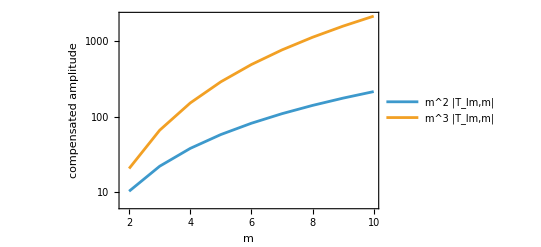

```mathematica
nearDataLM=hSNearParticleFalloff["lm",mRange,10^-4,10^-4];
ListLogPlot[{nearDataLM/. {mm_,val_}:>{mm,mm^2 val},nearDataLM/. {mm_,val_}:>{mm,mm^3 val}},Joined->True,Frame->True,FrameLabel->{"m","compensated amplitude"},PlotLegends->{"m^2 |T_lm,m|","m^3 |T_lm,m|"}]
```

```mathematica
mmbDirectionFits=Map[Function[eps,Module[{d,f},d=hSNearParticleFalloff["mmb",mRange,eps[[1]],eps[[2]]];
f=fitPowerLaw[d,fitRange];
<|"p"->f["p"],"R2"->f["R2"],"p - 2"->f["p"]-2,"p - 3"->f["p"]-3|>]],nearDirections];
```

```mathematica
ClearAll[parseMFromFile,loadIRGTeffGridFile,readMergedMFolder];

parseMFromFile[file_String]:=Module[{name,hit},name=FileNameTake[file];
hit=StringCases[name,"merged_"~~sign:("mp"|"mm")~~n:DigitCharacter..~~".mx":>If[sign==="mp",1,-1] ToExpression[n]];
If[hit==={},Missing["CouldNotParseM",name],First[hit]]];

loadIRGTeffGridFile[file_String]:=Module[{data},Clear[IRGTeffGridData];
(*These files define IRGTeffGridData*)Get[file];
data=IRGTeffGridData;
If[!AssociationQ[data],Print["Failed to load association from: ",file];
Return[$Failed]];
data];

readMergedMFolder[dir_String]:=Module[{files,pairs},files=SortBy[FileNames["TaBR_IRGGrid_merged_*.mx",dir],parseMFromFile];
Print["Found ",Length[files]," files"];
Print[Column[FileNameTake/@Take[files,UpTo[10]]]];
pairs=Table[parseMFromFile[file]->loadIRGTeffGridFile[file],{file,files}];
Association@DeleteCases[pairs,_->$Failed]];
```

```mathematica
mData=readMergedMFolder[mergedDir];

Keys[mData]
```

Keys::invrl: The argument readMergedMFolder[mergedDir] is not a valid Association or a list of rules.

Keys[readMergedMFolder[mergedDir]]

```mathematica
mData[-12]//Keys

mData[-12]["Data"]//Keys

mData[-12]["Components"]
```

Keys::invrl: The argument readMergedMFolder[mergedDir][-12] is not a valid Association or a list of rules.

Keys[readMergedMFolder[mergedDir][-12]]

Keys::invrl: The argument readMergedMFolder[mergedDir][-12][Data] is not a valid Association or a list of rules.

Keys[readMergedMFolder[mergedDir][-12][Data]]

readMergedMFolder[mergedDir][-12][Components]

```mathematica
ClearAll[finiteNumberQ,numericLeaves,gridNorm];

finiteNumberQ[z_]:=NumericQ[z]&&FreeQ[z,Indeterminate|ComplexInfinity|DirectedInfinity];

numericLeaves[obj_]:=Select[Cases[N[obj],z_?NumericQ:>z,Infinity],finiteNumberQ];

gridNorm[obj_Association,normType_:"rms"]:=Module[{vals},vals=numericLeaves[obj["Data"]];
If[Length[vals]==0,Missing["NoNumericValues"],Switch[normType,"max",Max[Abs[vals]],"l2",Sqrt[Total[Abs[vals]^2]],"rms",Sqrt[Mean[Abs[vals]^2]],"meanAbs",Mean[Abs[vals]],_,Sqrt[Mean[Abs[vals]^2]]]]];
```

```mathematica
mFalloffSigned=SortBy[KeyValueMap[{#1,gridNorm[#2,"rms"]}&,mData],First];

mFalloffAbs=SortBy[KeyValueMap[{#1,Sqrt[Mean[#2^2]]}&,GroupBy[Select[mFalloffSigned,NumericQ[#[[2]]]&],Abs[First[#]]&->Last]],First];

mFalloffAbs//Dataset
```

KeyValueMap::invak: The argument readMergedMFolder[mergedDir] is not a valid Association.

KeyValueMap::invak: The argument {#1,gridNorm[#2,rms]}& is not a valid Association.

Part::partw: Part 2 of readMergedMFolder[mergedDir] does not exist.

Part::partw: Part 2 of {#1,gridNorm[#2,rms]}& does not exist.

KeyValueMap::argt: KeyValueMap called with 0 arguments; 1 or 2 arguments are expected.

GroupBy::list1: The argument KeyValueMap[] is not a valid list of Associations or rules or lists of rules.

KeyValueMap::invak: The argument GroupBy[KeyValueMap[],(Abs[First[#1]]&)→Last] is not a valid Association.

KeyValueMap::invak: The argument {#1,√Mean[#2^2]}& is not a valid Association.

KeyValueMap[GroupBy[KeyValueMap[],(Abs[First[#1]]&)→Last],{#1,√Mean[#2^2]}&]

```mathematica
ListLogPlot[mFalloffAbs,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"|m|","RMS norm of grid data"},PlotLabel->"IRG grid m-mode falloff",ImageSize->Large]
```

KeyValueMap::invak: The argument False is not a valid Association.

ListLogPlot::lpn: KeyValueMap[GroupBy[KeyValueMap[],(Abs[First[#1]]&)→Last],{#1,√Mean[#2^2]}&] is not a list of numbers or pairs of numbers.

KeyValueMap::invak: The argument False is not a valid Association.

ListLogPlot::lpn: KeyValueMap[GroupBy[KeyValueMap[],(Abs[First[#1]]&)→Last],{#1,√Mean[#2^2]}&] is not a list of numbers or pairs of numbers.

ListLogPlot[KeyValueMap[GroupBy[KeyValueMap[],(Abs[First[#1]]&)→Last],{#1,√Mean[#2^2]}&],Joined→True,PlotMarkers→Automatic,Frame→True,FrameLabel→{|m|,RMS norm of grid data},PlotLabel→IRG grid m-mode falloff,ImageSize→Large]

```mathematica
ClearAll[fitPowerLawM];

fitPowerLawM[data_,{mmin_,mmax_}]:=Module[{tail,x,fit,p,curve,ms},tail=Select[data,mmin<=#[[1]]<=mmax&&#[[1]]>0&&#[[2]]>0&];
fit=LinearModelFit[({Log[#[[1]]],Log[#[[2]]]}&/@tail),x,x];
p=-Coefficient[Normal[fit],x];
ms=Range[mmin,mmax];
curve={#,Exp[fit[Log[#]]]}&/@ms;
<|"p"->p,"fit"->fit,"plot"->ListLogLogPlot[{data,curve},Joined->{False,True},PlotMarkers->{Automatic,None},Frame->True,FrameLabel->{"|m|","norm"},PlotLegends->{"data",Row[{"fit: |m|^-",NumberForm[p,{6,3}]}]},PlotLabel->Row[{"Power-law fit over ",mmin," ≤ |m| ≤ ",mmax}],ImageSize->Large]|>];
```

```mathematica
fitM=fitPowerLawM[mFalloffAbs,{8,20}];

fitM["p"]
fitM["plot"]
```

Part::partw: Part 2 of {#1,√Mean[#2^2]}& does not exist.

KeyValueMap::argt: KeyValueMap called with 0 arguments; 1 or 2 arguments are expected.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

ListLogLogPlot::lpn: {{},{{2.079441541679836,Log[2.718281828459045^(LinearModelFit[KeyValueMap[],x$88111,x$88111][2.079441541679836])]},{«57»,Log[(«44»)^(«14»[«1»][«59»])]},«9»,{«59»,Log[«1»]},{2.995732273553991,Log[2.718281828459045^(LinearModelFit[KeyValueMap[],x$88111,x$88111][«57»])]}}} is not a list of numbers or pairs of numbers.

0

ListLogLogPlot[{KeyValueMap[GroupBy[KeyValueMap[],(Abs[First[#1]]&)→Last],{#1,√Mean[#2^2]}&],{{8,ⅇ^(LinearModelFit[KeyValueMap[],x$88111,x$88111][Log[8]])},{9,ⅇ^(LinearModelFit[KeyValueMap[],x$88111,x$88111][Log[9]])},{10,ⅇ^(LinearModelFit[KeyValueMap[],x$88111,x$88111][Log[10]])},{11,ⅇ^(LinearModelFit[KeyValueMap[],x$88111,x$88111][Log[11]])},{12,ⅇ^(LinearModelFit[KeyValueMap[],x$88111,x$88111][Log[12]])},{13,ⅇ^(LinearModelFit[KeyValueMap[],x$88111,x$88111][Log[13]])},{14,ⅇ^(LinearModelFit[KeyValueMap[],x$88111,x$88111][Log[14]])},{15,ⅇ^(LinearModelFit[KeyValueMap[],x$88111,x$88111][Log[15]])},{16,ⅇ^(LinearModelFit[KeyValueMap[],x$88111,x$88111][Log[16]])},{17,ⅇ^(LinearModelFit[KeyValueMap[],x$88111,x$88111][Log[17]])},{18,ⅇ^(LinearModelFit[KeyValueMap[],x$88111,x$88111][Log[18]])},{19,ⅇ^(LinearModelFit[KeyValueMap[],x$88111,x$88111][Log[19]])},{20,ⅇ^(LinearModelFit[KeyValueMap[],x$88111,x$88111][Log[20]])}}},Joined→{False,True},PlotMarkers→{Automatic,None},Frame→True,FrameLabel→{|m|,norm},PlotLegends→{data,fit: |m|^-0},PlotLabel→Power-law fit over 8 ≤ |m| ≤ 20,ImageSize→Large]

```mathematica
ListLogPlot[{Select[mFalloffSigned,#[[1]]>0&],({Abs[#[[1]]],#[[2]]}&/@Select[mFalloffSigned,#[[1]]<0&])},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"|m|","RMS norm"},PlotLegends->{"+m","-m"},PlotLabel->"Positive vs negative m falloff",ImageSize->Large]
```

KeyValueMap::argt: KeyValueMap called with 0 arguments; 1 or 2 arguments are expected.

-Graphics-

### metric falloffs

```mathematica
epsX=10^-1;
epsY=10^-1;
nmax=4;              (* puncture order*)
mRange={30,100};
fitRange={80,100};
```

```mathematica
ClearAll[conditionMetricSymbolic];
conditionMetricSymbolic[expr_]:=expr/. hS1FinalRules$Kerr/. tovals;
```

```mathematica
ClearAll[hSMModeHeads];

hSMModeHeads=<|
"ll"->hSll$MMode$XY,"ln"->hSln$MMode$XY,"lm"->hSlm$MMode$XY,"lmb"->hSlmb$MMode$XY,
"nn"->hSnn$MMode$XY,"nm"->hSnm$MMode$XY,"nmb"->hSnmb$MMode$XY,
"mm"->hSmm$MMode$XY,"mmb"->hSmmb$MMode$XY,
"mbmb"->hSmbmb$MMode$XY|>;
```

```mathematica
(* Then memoize the symbolic source and jet for each component: *)
ClearAll@hSExpr
hSExpr[key_String,m_]:=hSExpr[key,m]=Module[{head},head=hSMModeHeads[key];
conditionMetricSymbolic[head[m][X,Y]]];
```

```mathematica
ClearAll[hSVal];

hSVal[key_String,mm_Integer,x_?NumericQ,y_?NumericQ]:=Quiet@Check[N64[hSExpr[key,mm]/. {X->x,Y->y}],Indeterminate];
```

```mathematica
ClearAll[hSNearParticleVal];

hSNearParticleVal[key_String,mm_Integer,epsX_?NumericQ,epsY_?NumericQ]:=Quiet@Check[N[hSExpr[key,mm]/. {X->epsX,Y->epsY}],Indeterminate];
```

```mathematica
ClearAll[hSNearParticleFalloff];

hSNearParticleFalloff[key_String,{mmin_,mmax_},epsX_?NumericQ,epsY_?NumericQ]:=Select[Table[{mm,Abs@hSNearParticleVal[key,mm,epsX,epsY]},{mm,mmin,mmax}],NumericQ[#[[2]]]&&#[[2]]>0&];
```

```mathematica
ClearAll[goodComplexQ,hSComponentRMS];

goodComplexQ[z_]:=NumericQ[z]&&FreeQ[z,Indeterminate|ComplexInfinity|DirectedInfinity|_Overflow];

hSComponentRMS[key_String,mm_Integer,pts_List:falloffPts]:=Module[{vals},vals=DeleteCases[Table[hSVal[key,mm,pt[[1]],pt[[2]]],{pt,pts}],z_/;!goodComplexQ[z]];
If[vals==={},Missing["NoGoodValues"],Sqrt[Mean[Abs[vals]^2]]]];
```

```mathematica
ClearAll[hSFalloffData];

hSFalloffData[key_String,mmin_Integer,mmax_Integer]:=Select[Table[{mm,hSComponentRMS[key,mm]},{mm,mmin,mmax}],NumericQ[#[[2]]]&&#[[2]]>0&];
```

```mathematica
hSfalloffData=AssociationMap[hSFalloffData[#,mRange[[1]],mRange[[2]]]&,Keys[hSMModeHeads]];

hSfalloffFits=AssociationMap[fitMFalloff[hSfalloffData[#],fitRange]&,Keys[hSMModeHeads]];

Dataset@AssociationMap[<|"measured p"->hSfalloffFits[#]["p"],"target nmax"->nmax,"p - nmax"->hSfalloffFits[#]["p"]-nmax,"slope"->hSfalloffFits[#]["slope"],"R2"->hSfalloffFits[#]["R2"]|>&,Keys[hMModeHeads]]
```

$Aborted

```mathematica
hSnearDataLN=hSNearParticleFalloff["nn",mRange,epsX,epsY];
nearFitLN=fitPowerLaw[hSnearDataLN,fitRange];
```

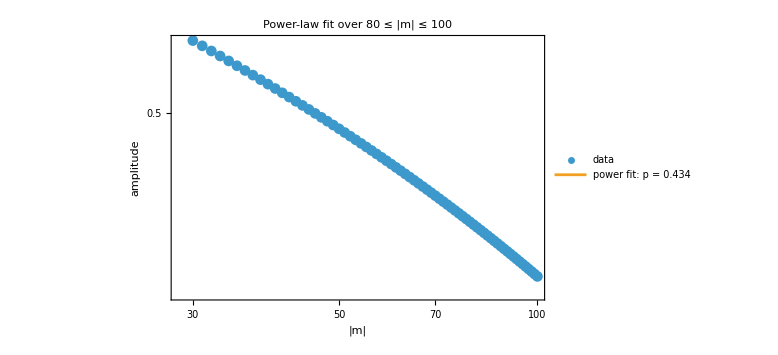
<|p→0.433923,fit→FittedModel[…],RSquared→0.999854,curve→{{80,0.405815},{81,0.403634},{82,0.40149},{83,0.399384},{84,0.397314},{85,0.395279},{86,0.393278},{87,0.39131},{88,0.389374},{89,0.38747},{90,0.385596},{91,0.383751},{92,0.381936},{93,0.380148},{94,0.378388},{95,0.376655},{96,0.374947},{97,0.373265},{98,0.371607},{99,0.369974},{100,0.368364}},plot→-Graphics-|>

```mathematica
nearFitLN
```

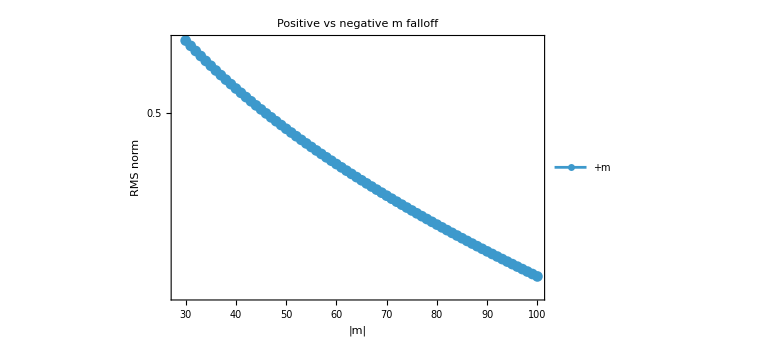

```mathematica
ListLogPlot[{Select[hSnearDataLN,#[[1]]>0&]},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"|m|","RMS norm"},PlotLegends->{"+m","-m"},PlotLabel->"Positive vs negative m falloff",ImageSize->Large]
```

```mathematica
ClearAll[fitExpLaw,fitPowerLaw,compareFalloffFits];

fitExpLaw[data_,{mmin_,mmax_}]:=Module[{tail,x,fit,alpha,curve,ms},tail=Select[data,mmin<=#[[1]]<=mmax&&#[[1]]>0&&#[[2]]>0&];
If[Length[tail]<3,Return[<|"error"->"Too few data points","tailData"->tail|>]];
fit=LinearModelFit[({#[[1]],Log[#[[2]]]}&/@tail),x,x];
alpha=-Coefficient[Normal[fit],x];
ms=Range[mmin,mmax];
curve={#,Exp[fit[#]]}&/@ms;
<|"alpha"->alpha,"fit"->fit,"RSquared"->fit["RSquared"],"curve"->curve,"plot"->ListLogPlot[{data,curve},Joined->{False,True},PlotMarkers->{Automatic,None},Frame->True,FrameLabel->{"|m|","amplitude"},PlotLegends->{"data",Row[{"exp fit: α = ",NumberForm[alpha,{6,4}]}]},PlotLabel->Row[{"Exponential fit over ",mmin," ≤ |m| ≤ ",mmax}],ImageSize->Large]|>];

fitPowerLaw[data_,{mmin_,mmax_}]:=Module[{tail,x,fit,p,curve,ms},tail=Select[data,mmin<=#[[1]]<=mmax&&#[[1]]>0&&#[[2]]>0&];
If[Length[tail]<3,Return[<|"error"->"Too few data points","tailData"->tail|>]];
fit=LinearModelFit[({Log[#[[1]]],Log[#[[2]]]}&/@tail),x,x];
p=-Coefficient[Normal[fit],x];
ms=Range[mmin,mmax];
curve={#,Exp[fit[Log[#]]]}&/@ms;
<|"p"->p,"fit"->fit,"RSquared"->fit["RSquared"],"curve"->curve,"plot"->ListLogLogPlot[{data,curve},Joined->{False,True},PlotMarkers->{Automatic,None},Frame->True,FrameLabel->{"|m|","amplitude"},PlotLegends->{"data",Row[{"power fit: p = ",NumberForm[p,{6,3}]}]},PlotLabel->Row[{"Power-law fit over ",mmin," ≤ |m| ≤ ",mmax}],ImageSize->Large]|>];

compareFalloffFits[data_,fitRange_]:=Module[{exp,pow},exp=fitExpLaw[data,fitRange];
pow=fitPowerLaw[data,fitRange];
<|"fitRange"->fitRange,"exponentialAlpha"->exp["alpha"],"exponentialRSquared"->exp["RSquared"],"powerLawP"->pow["p"],"powerLawRSquared"->pow["RSquared"],"expPlot"->exp["plot"],"powerPlot"->pow["plot"]|>];
```

0.00522431

0.998301

0.411657

0.999322

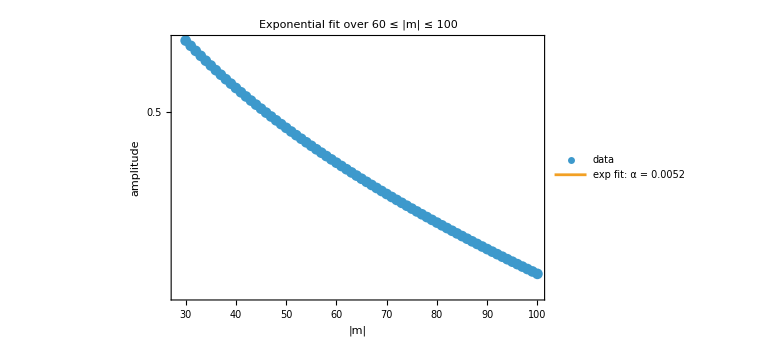

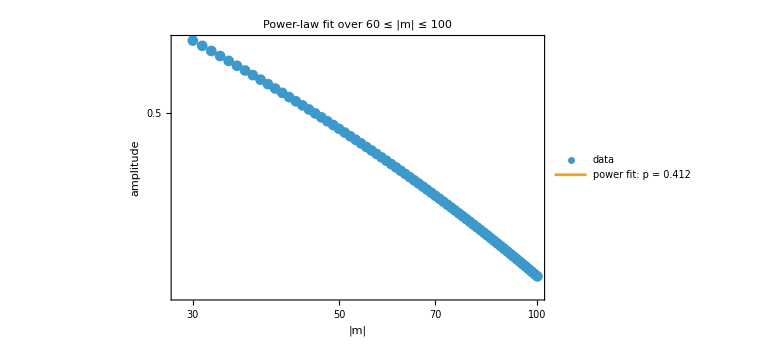

```mathematica
fitRange={60,100};

cmp=compareFalloffFits[hSnearDataLN,fitRange];

cmp["exponentialAlpha"]
cmp["exponentialRSquared"]

cmp["powerLawP"]
cmp["powerLawRSquared"]

cmp["expPlot"]
cmp["powerPlot"]
```

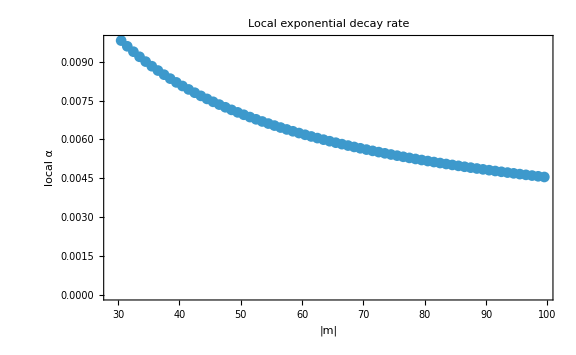

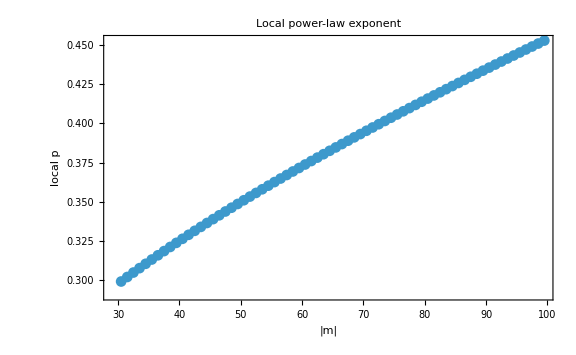

```mathematica
ClearAll[localAlpha,localP];

localAlpha[data_]:=Module[{clean,pairs},clean=Select[data,#[[1]]>0&&#[[2]]>0&];
pairs=Partition[clean,2,1];
({Mean[{#[[1,1]],#[[2,1]]}],-Log[#[[2,2]]/#[[1,2]]]/(#[[2,1]]-#[[1,1]])}&/@pairs)];

localP[data_]:=Module[{clean,pairs},clean=Select[data,#[[1]]>0&&#[[2]]>0&];
pairs=Partition[clean,2,1];
({Mean[{#[[1,1]],#[[2,1]]}],-Log[#[[2,2]]/#[[1,2]]]/Log[#[[2,1]]/#[[1,1]]]}&/@pairs)];

ListPlot[localAlpha[hSnearDataLN],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"|m|","local α"},PlotLabel->"Local exponential decay rate",ImageSize->Large]

ListPlot[localP[hSnearDataLN],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"|m|","local p"},PlotLabel->"Local power-law exponent",ImageSize->Large]
```

## Dump NP components of h_ab^P to file

```mathematica
mMaxTest=3;
mMax=10;
```

### Test cache export

```mathematica
(* ============================================================*)
(*Evaluate compiled T_ab^eff 2-jets on the full X,Y grid*)(*one file per m*)(* ============================================================*)ClearAll[mFileTag,dumphSGridCache,loadhSGridCache,evalCompiledObjectOnXYGrid,computehSGridForM,runhSGridCache];

mFileTag[m_Integer]:=If[m<0,"m"<>ToString[Abs[m]],"p"<>ToString[m]];

dumphSGridCache[file_String,obj_Association]:=Module[{},Clear[hSGridCache];
hSGridCache=obj;
DumpSave[file,hSGridCache];
Clear[hSGridCache];
file];

loadhSGridCache[file_String]:=Module[{},Clear[hSGridCache];
Get[file];
hSGridCache];
```

```mathematica
evalCompiledObjectOnXYGrid[obj_Association,xgrid_List,ygrid_List]:=AssociationMap[evalCompiledObjectOnXYGrid[obj[#],xgrid,ygrid]&,Keys[obj]];

evalCompiledObjectOnXYGrid[f_,xgrid_List,ygrid_List]:=Module[{xs,ys},xs=Developer`ToPackedArray[N@xgrid];
ys=Developer`ToPackedArray[N@ygrid];
Developer`ToPackedArray[Table[f[x,y],{x,xs},{y,ys}]]];
```

#### old single Y-patch infra

```mathematica
Options[computehSGridForM]={"Components"->{"ll","lm","lmb","ln","mm"},
"OutputDirectory"->Automatic,"Overwrite"->False,"ExtraMetadata"-><||>};

computehSGridForM[m_Integer,xPatchGrids_Association,ygrid_List,OptionsPattern[]]:=Module[{components,outDir,overwrite,extra,file,jetFuns,data,obj},components=OptionValue["Components"];
outDir=OptionValue["OutputDirectory"];
overwrite=TrueQ@OptionValue["Overwrite"];
extra=OptionValue["ExtraMetadata"];
If[outDir===Automatic,outDir=FileNameJoin[{NotebookDirectory[],"hS_psi0_IRG_Comps_GridCache"}]];
If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];
file=FileNameJoin[{outDir,"hSIRGGrid_m"<>mFileTag[m]<>".mx"}];
If[FileExistsQ[file]&&!overwrite,Return[<|"m"->m,"status"->"exists","file"->file|>]];
Print["m = ",m,": compiling components ",components];
jetFuns=AssociationMap[hSJetCompiled[#,m]&,components];
Print["m = ",m,": evaluating on X,Y grids"];
data=AssociationMap[Function[patchName,AssociationMap[evalCompiledObjectOnXYGrid[jetFuns[#],xPatchGrids[patchName],ygrid]&,components]],Keys[xPatchGrids]];
obj=<|"m"->m,"components"->components,"YGrid"->ygrid,"XPatchGrids"->xPatchGrids,"Data"->data,"Dimensions"->AssociationMap[<|"NX"->Length[xPatchGrids[#]],"NY"->Length[ygrid]|>&,Keys[xPatchGrids]],"Created"->DateString[],"Metadata"->extra|>;
dumphSGridCache[file,obj];
<|"m"->m,"status"->"computed","file"->file,"components"->components,"patches"->Keys[xPatchGrids]|>];
```

```mathematica
Options[runhSIRGGridCache]={"Components"->{"ll","ln", "lm","mm"},"OutputDirectory"->Automatic,"Overwrite"->True,"Parallel"->True,"ExtraMetadata"-><||>};

runhSIRGGridCache[mList_List,xPatchGrids_Association,ygrid_List,OptionsPattern[]]:=Module[{components,outDir,overwrite,parallel,extra,worker,results},components=OptionValue["Components"];
outDir=OptionValue["OutputDirectory"];
overwrite=TrueQ@OptionValue["Overwrite"];
parallel=TrueQ@OptionValue["Parallel"];
extra=OptionValue["ExtraMetadata"];
If[outDir===Automatic,outDir=FileNameJoin[{NotebookDirectory[],"hSab_NP_IRGcomps_Cache"}]];
If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];
worker[mm_Integer]:=computehSGridForM[mm,xPatchGrids,ygrid,"Components"->components,"OutputDirectory"->outDir,"Overwrite"->overwrite,"ExtraMetadata"->extra];
If[parallel,LaunchKernels[];
DistributeDefinitions[mFileTag,dumphSGridCache,loadhSGridCache,evalCompiledObjectOnXYGrid,computehSGridForM,hSJetCompiled,compileJet2,hSJet2,hS1FinalRules$Kerr,tovals,to0vals];
results=ParallelMap[worker,mList,Method->"CoarsestGrained"],results=Map[worker,mList]];
Dataset[results]];
```

#### new multi patch test-run

```mathematica
ClearAll[computehSGridForM$Allpatches];

Options[computehSGridForM$Allpatches]={"Components"->{"ll","lm","lmb","ln","mm"},"OutputDirectory"->Automatic,"Overwrite"->False,"ExtraMetadata"-><||>};

computehSGridForM$Allpatches[m_Integer,patches_Association,OptionsPattern[]]:=Module[{components,outDir,overwrite,extra,file,jetFuns,data,obj,patchNames,dimensions,storedPatches},components=OptionValue["Components"];
outDir=OptionValue["OutputDirectory"];
overwrite=TrueQ@OptionValue["Overwrite"];
extra=OptionValue["ExtraMetadata"];
If[outDir===Automatic,outDir=FileNameJoin[{NotebookDirectory[],"hS_psi0_IRG_Comps_GridCache"}]];
If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];
(*--------------------------------------------------------*)(*One cache file per m.Each file contains all four*)(*(X,Y) patches:LL,LR,RL,RR.*)(*--------------------------------------------------------*)file=FileNameJoin[{outDir,"hSIRGGrid_m"<>mFileTag[m]<>".mx"}];
If[FileExistsQ[file]&&!overwrite,Return[<|"m"->m,"status"->"exists","file"->file|>]];
patchNames=Keys[patches];
Print["m = ",m,": compiling components ",components];
(*Compile only once for this m*)jetFuns=AssociationMap[hSJetCompiled[#,m]&,components];
Print["m = ",m,": evaluating patches ",patchNames];
(* ========================================================*)(*Evaluate every component on every 2D X-Y patch*)(**)(*Data structure:*)(**)(*Data["LL"]["ll"]*)(*Data["LL"]["lm"]*)(*...*)(*Data["RR"]["mm"]*)(* ========================================================*)data=AssociationMap[Function[patchName,With[{xgrid=patches[patchName]["XGrid"],ygrid=patches[patchName]["YGrid"]},AssociationMap[evalCompiledObjectOnXYGrid[jetFuns[#],xgrid,ygrid]&,components]]],patchNames];
(*--------------------------------------------------------*)(*Store dimensions and side information patch by patch*)(*--------------------------------------------------------*)dimensions=AssociationMap[Function[patchName,With[{p=patches[patchName]},<|"NX"->Length[p["XGrid"]],"NY"->Length[p["YGrid"]],"XSide"->p["XSide"],"YSide"->p["YSide"]|>]],patchNames];
(*--------------------------------------------------------*)(*Save the coordinate information used for every patch.*)(*This replaces the old single YGrid+XPatchGrids setup.*)(*--------------------------------------------------------*)storedPatches=AssociationMap[Function[patchName,KeyTake[patches[patchName],{"Name","XSide","YSide","XGrid","YGrid","ZOnYGrid","ThetaOnYGrid"}]],patchNames];
obj=<|"m"->m,"components"->components,"Patches"->storedPatches,"Data"->data,"Dimensions"->dimensions,"Created"->DateString[],"Metadata"->extra|>;
dumphSGridCache[file,obj];
<|"m"->m,"status"->"computed","file"->file,"components"->components,"patches"->patchNames,"dimensions"->dimensions|>];


ClearAll[runhSIRGGridCache$Allpatches];
Options[runhSIRGGridCache$Allpatches]={"Components"->{"ll","ln", "lm","mm"},"OutputDirectory"->Automatic,"Overwrite"->True,"Parallel"->True,"ExtraMetadata"-><||>};

runhSIRGGridCache$Allpatches[mList_List,patches_Association,OptionsPattern[]]:=Module[{components,outDir,overwrite,parallel,extra,patchNames,jobs,worker,results},components=OptionValue["Components"];
outDir=OptionValue["OutputDirectory"];
overwrite=TrueQ@OptionValue["Overwrite"];
parallel=TrueQ@OptionValue["Parallel"];
extra=OptionValue["ExtraMetadata"];
If[outDir===Automatic,outDir=FileNameJoin[{NotebookDirectory[],"hSab_NP_IRGcomps_Cache"}]];
If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];
patchNames=Keys[patches];
(*---------------------------------------------------------*)(*One job for every {m,2D patch} combination*)(**)(*LL:X<0,Y<0*)(*LR:X<0,Y>0*)(*RL:X>0,Y<0*)(*RR:X>0,Y>0*)(*---------------------------------------------------------*)jobs=Flatten[Table[{mm,patchName},{mm,mList},{patchName,patchNames}],1];
worker[{mm_Integer,patchName_String}]:=Module[{patch,meta},patch=patches[patchName];
(*Add patch information to whatever metadata was supplied*)meta=Join[If[AssociationQ[extra],extra,<||>],<|"Patch"->patchName,"PatchName"->patch["Name"],"XSide"->patch["XSide"],"YSide"->patch["YSide"]|>];
computehSGridForM$Allpatches[mm,patch,"Components"->components,"OutputDirectory"->outDir,"Overwrite"->overwrite,"ExtraMetadata"->meta]];
If[parallel,LaunchKernels[];
DistributeDefinitions[mFileTag,dumphSGridCache,loadhSGridCache,evalCompiledObjectOnXYGrid,computehSGridForM$Allpatches,hSJetCompiled,compileJet2,hSJet2,hS1FinalRules$Kerr,tovals,to0vals];
results=ParallelMap[worker,jobs,Method->"CoarsestGrained"],results=Map[worker,jobs]];
Dataset[results]];
```

#### Generate hP_m Cacha data

```mathematica
mMax=10;
```

```mathematica
xPatchGridsTest=<|"Left"->XLeftGrid,"Right"->XRightGrid|>;

mList=Range[-mMax,mMax];

irgCacheReport=runhSIRGGridCache[mList,xPatchGridsTest,YGrid,"Components"->{"ll","ln", "lm","mm"},"OutputDirectory"->FileNameJoin[{NotebookDirectory[],"hSIRGGridCache_XYwindowed_testGrid_a", ToString[aKerr]}],"Overwrite"->False,"Parallel"->True,"ExtraMetadata"-><|"description"->"Compiled IRG hS 2-jets on X,Y grid needed for ψ0 puncture","nXLeft"->Length[XLeftGrid],"nXRight"->Length[XRightGrid],"nY"->Length[YGrid]|>];
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

m = -10: compiling components {ll,ln,lm,mm}

m = -4: compiling components {ll,ln,lm,mm}

m = 1: compiling components {ll,ln,lm,mm}

m = 6: compiling components {ll,ln,lm,mm}

m = 6: evaluating on X,Y grids

m = 1: evaluating on X,Y grids

m = -4: evaluating on X,Y grids

m = -10: evaluating on X,Y grids

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

General::munfl: 1/2.718281828459045235360287471352662497757247093699959574966967628^26633.1 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.718281828459045235360287471352662497757247093699959574966967628^2515.29 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.718281828459045235360287471352662497757247093699959574966967628^1859.67 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

General::munfl: 1/2.718281828459045235360287471352662497757247093699959574966967628^26633.1 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.718281828459045235360287471352662497757247093699959574966967628^2515.29 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.718281828459045235360287471352662497757247093699959574966967628^1859.67 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

General::munfl: 1/2.718281828459045235360287471352662497757247093699959574966967628^26633.1 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.718281828459045235360287471352662497757247093699959574966967628^2515.29 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.718281828459045235360287471352662497757247093699959574966967628^1859.67 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

General::munfl: 1/2.718281828459045235360287471352662497757247093699959574966967628^26633.1 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.718281828459045235360287471352662497757247093699959574966967628^2515.29 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.718281828459045235360287471352662497757247093699959574966967628^1859.67 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

m = 2: compiling components {ll,ln,lm,mm}

m = 2: evaluating on X,Y grids

m = -3: compiling components {ll,ln,lm,mm}

m = 7: compiling components {ll,ln,lm,mm}

m = -3: evaluating on X,Y grids

m = 7: evaluating on X,Y grids

m = -9: compiling components {ll,ln,lm,mm}

m = -9: evaluating on X,Y grids

m = 3: compiling components {ll,ln,lm,mm}

m = 3: evaluating on X,Y grids

m = -2: compiling components {ll,ln,lm,mm}

m = -2: evaluating on X,Y grids

m = 8: compiling components {ll,ln,lm,mm}

m = 8: evaluating on X,Y grids

m = -8: compiling components {ll,ln,lm,mm}

m = -8: evaluating on X,Y grids

```mathematica
irgCacheReport$allPatches=runhSIRGGridCache$Allpatches[mList,patchAssoc,"Parallel"->True,"Overwrite"->False];
```

### Production h_ab export

```mathematica
(* ============================================================*)
(*Kerr-safe compiled hS grid exporter:one file per m*)
(*Uses hSJetCompiled[key,m]*)
(* ============================================================*)ClearAll[mTag,evalJetOnXYGrid,evalComponentJetOnPatch,computeIRGhSGridForM,dumpIRGhSGridForM,runIRGhSGridExport];

mTag[m_Integer]:=If[m<0,"m"<>ToString[Abs[m]],"p"<>ToString[m]];
```

#### old stuff

```mathematica
(*Evaluate one compiled function f[x,y] on an X,Y tensor grid.*)
evalJetOnXYGrid[f_,xgrid_List,ygrid_List]:=
Module[{xs,ys},
xs=Developer`ToPackedArray@N[xgrid];
ys=Developer`ToPackedArray@N[ygrid];
Developer`ToPackedArray[Table[Quiet@Check[f[x,y],Indeterminate],{x,xs},{y,ys}]]];


(*A hSJetCompiled[key,m] object should be an association:<|"F"->cf,"Fx"->cfX,"Fy"->cfY,...|> This evaluates all jet entries on one patch.*)
evalComponentJetOnPatch[jet_Association,xgrid_List,ygrid_List]:=AssociationMap[evalJetOnXYGrid[jet[#],xgrid,ygrid]&,Keys[jet]];


Options[computeIRGhSGridForM]={"Components"->{"ll","lm","mm"},"PatchGrids"->Automatic,"YGrid"->Automatic,"Metadata"-><||>};

computeIRGhSGridForM[m_Integer,OptionsPattern[]]:=Module[{components,patchGrids,ygrid,metadata,compiledJets,data},components=OptionValue["Components"];
patchGrids=OptionValue["PatchGrids"];
ygrid=OptionValue["YGrid"];
metadata=OptionValue["Metadata"];
If[patchGrids===Automatic,patchGrids=<|"left"->XLeftGridProd,"right"->XRightGridProd|>];
If[ygrid===Automatic,ygrid=YGrid];
Print["m = ",m,": compiling hab components ",components];
compiledJets=AssociationMap[hSJetCompiled[#,m]&,components];
Print["m = ",m,": evaluating on X,Y grids"];
data=AssociationMap[Function[patch,AssociationMap[evalComponentJetOnPatch[compiledJets[#],patchGrids[patch],ygrid]&,components]],Keys[patchGrids]];
<|"Type"->"CompiledhSGrid","Gauge"->"IRG","SpinSource"->"+2","m"->m,"Components"->components,"JetKeys"->AssociationMap[Keys[compiledJets[#]]&,components],"PatchNames"->Keys[patchGrids],"XPatchGrids"->patchGrids,"YGrid"->ygrid,"Data"->data,"Dimensions"->AssociationMap[<|"NX"->Length[patchGrids[#]],"NY"->Length[ygrid]|>&,Keys[patchGrids]],"Metadata"->metadata,"Created"->DateString[]|>];


dumpIRGhSGridForM[file_String,obj_Association]:=
Module[{},
Clear[IRGhSGridData];
IRGhSGridData=obj;
DumpSave[file,IRGhSGridData];
Clear[IRGhSGridData];
file];
```

```mathematica
Options[runIRGhSGridExport]=
{"Components"->{"ll","lm","mm"},
"MList"->Automatic,"OutputDirectory"->Automatic,
"PatchGrids"->Automatic,
"YGrid"->Automatic,"Overwrite"->False,
"Parallel"->True,"Metadata"-><||>};

runIRGhSGridExport[OptionsPattern[]]:=Module[{components,mList,outDir,patchGrids,ygrid,overwrite,parallel,metadata,worker,results},components=OptionValue["Components"];
mList=OptionValue["MList"];
outDir=OptionValue["OutputDirectory"];
patchGrids=OptionValue["PatchGrids"];
ygrid=OptionValue["YGrid"];
overwrite=TrueQ@OptionValue["Overwrite"];
parallel=TrueQ@OptionValue["Parallel"];
metadata=OptionValue["Metadata"];
If[mList===Automatic,mList=Range[-mMax,mMax]];
If[outDir===Automatic,outDir=FileNameJoin[{NotebookDirectory[],"TabR_IRGGridData"}]];
If[patchGrids===Automatic,patchGrids=<|"left"->XLeftGridProd,"right"->XRightGridProd|>];
If[ygrid===Automatic,ygrid=YGrid];
If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];
worker[mm_Integer]:=Module[{file,obj},file=FileNameJoin[{outDir,"hSGrid_m"<>mTag[mm]<> "_a"<> ToString[aKerr]<>".mx"}];
If[FileExistsQ[file]&&!overwrite,Return[<|"m"->mm,"status"->"exists","file"->file|>]];
obj=computeIRGhSGridForM[mm,"Components"->components,"PatchGrids"->patchGrids,"YGrid"->ygrid,"Metadata"->metadata];
dumpIRGhSGridForM[file,obj];
<|"m"->mm,"status"->"computed","file"->file,"components"->components,"patches"->Keys[patchGrids]|>];
If[parallel,LaunchKernels[];
DistributeDefinitions[mTag,evalJetOnXYGrid,evalComponentJetOnPatch,computeIRGhSGridForM,dumpIRGhSGridForM,hSJetCompiled,compileJet2,hSJet2,hS1FinalRules$Kerr,tovals,to0vals, XLeftGridProd,XRightGridProd,patchLeftProd, patchRightProd, YGrid];
results=ParallelMap[worker,mList,Method->"CoarsestGrained"],results=Map[worker,mList]];
Dataset[results]];
```

```mathematica
irgReport=runIRGTeffGridExport["Components"->{"ll","lm","mm"},
"MList"->Range[-mMax,mMax],
"OutputDirectory"->FileNameJoin[{NotebookDirectory[],"hSm_for_ψmP_Jets_GridData"}],
"PatchGrids"->
<|
"left"->XLeftGridProd,
"right"->XRightGridProd
|>,
"YGrid"->YGrid,
"Overwrite"->False,
"Parallel"->True,
"Metadata"->
<|
"aKerr"->aKerr,"r0"->r0val,"B"->ℬ0val,"X0"->X0val,
"nXLeft"->Length[XLeftGridProd],"nXRight"->Length[XRightGridProd],
"nY"->Length[YGrid],
"Windows" ->{WX[x_]:>Exp[1-1/(1-(ℬ x/2)^4)],WY[y_]:>Exp[1-1/(1-(y/r0)^4)]},
"note"->"Kerr IRG effective-source 2-jets generated from TeffJetCompiled"
|>
];
```

$Aborted

#### new multi patch prod

```mathematica
(* ========================================================================*)
(*Low-level tensor-grid evaluation*)
(* ========================================================================*)
(*Evaluate one compiled function f[x,y] on an X,Y tensor grid.*)
ClearAll[evalJetOnXYGrid];

evalJetOnXYGrid[f_,xgrid_List,ygrid_List]:=Module[{xs,ys},xs=Developer`ToPackedArray@N[xgrid];
ys=Developer`ToPackedArray@N[ygrid];
Developer`ToPackedArray[Table[Quiet@Check[f[x,y],Indeterminate],{x,xs},{y,ys}]]];


(*A hSJetCompiled[key,m] object has the form*
*<|"F"->cf,"Fx"->cfX,"Fy"->cfY,...|>*
*Evaluate every jet entry on one X x Y patch.*)
ClearAll[evalComponentJetOnPatch];

evalComponentJetOnPatch[jet_Association,xgrid_List,ygrid_List]:=AssociationMap[evalJetOnXYGrid[jet[#],xgrid,ygrid]&,Keys[jet]];
```

```mathematica
(* ========================================================================*)(*Compute all IRG hS components for one m on all 2D patches*)     (**)
(*The production domain is split into four X-Y patches:*)(**)
(*LL:X<0,Y<0*)(*LR:X<0,Y>0*)(*RL:X>0,Y<0*)(*RR:X>0,Y>0*)(**)
(*Each patch carries its own XGrid,YGrid,ZOnYGrid and ThetaOnYGrid.*)(*The compiled component jets are constructed only once per m and are*)
(*then evaluated on all four tensor-product patches.*)(* ========================================================================*)
ClearAll[computeIRGhSGridForM];

Options[computeIRGhSGridForM]={"Components"->{"ll","lm","mm"},"Patches"->Automatic,"Metadata"-><||>};

computeIRGhSGridForM[m_Integer,OptionsPattern[]]:=Module[{components,patches,metadata,patchNames,compiledJets,data,dimensions,storedPatches},components=OptionValue["Components"];
patches=OptionValue["Patches"];
metadata=OptionValue["Metadata"];
(*Default to the four production patches*)If[patches===Automatic,patches=patchAssocProd];
patchNames=Keys[patches];
(*--------------------------------------------------------------------*)
(*Compile each requested NP component once for this m*)
(*--------------------------------------------------------------------*)Print["m = ",m,": compiling hab components ",components];
compiledJets=AssociationMap[hSJetCompiled[#,m]&,components];
(*--------------------------------------------------------------------*)
(*Evaluate every component on every 2D patch*)(**)(*Result structure:*)
(**)(*data["LL"]["ll"]["F"]*)(*data["LL"]["ll"]["Fx"]*)(*...*)(*data["RR"]["mm"]["Fxy"]*)(*--------------------------------------------------------------------*)Print["m = ",m,": evaluating patches ",patchNames];
data=AssociationMap[Function[patchName,With[{p=patches[patchName]},AssociationMap[evalComponentJetOnPatch[compiledJets[#],p["XGrid"],p["YGrid"]]&,components]]],patchNames];
(*--------------------------------------------------------------------*)(*Dimensions and side information for each patch*)(*--------------------------------------------------------------------*)dimensions=AssociationMap[Function[patchName,With[{p=patches[patchName]},<|"NX"->Length[p["XGrid"]],"NY"->Length[p["YGrid"]],"XSide"->p["XSide"],"YSide"->p["YSide"]|>]],patchNames];
(*--------------------------------------------------------------------*)(*Store the grids used for each patch*)(**)(*There is deliberately no longer a global YGrid:LL/RL use YLeft,*)(*while LR/RR use YRight.*)(*--------------------------------------------------------------------*)storedPatches=AssociationMap[Function[patchName,KeyTake[patches[patchName],{"Name","XSide","YSide","XGrid","YGrid","ZOnYGrid","ThetaOnYGrid"}]],patchNames];
<|"Type"->"CompiledhSGrid","Gauge"->"IRG","SpinSource"->"+2","m"->m,"Components"->components,"JetKeys"->AssociationMap[Keys[compiledJets[#]]&,components],"PatchNames"->patchNames,"Patches"->storedPatches,"Data"->data,"Dimensions"->dimensions,"Metadata"->metadata,"Created"->DateString[]|>];

(* ========================================================================*)
(*Dump one complete m-mode,containing all four X-Y patches*)(* ========================================================================*)
ClearAll[dumpIRGhSGridForM];

dumpIRGhSGridForM[file_String,obj_Association]:=Module[{},Clear[IRGhSGridData];
IRGhSGridData=obj;
DumpSave[file,IRGhSGridData];
Clear[IRGhSGridData];
file];
```

```mathematica
(* ========================================================================*)(*Production export over all m modes*)(**)(*Parallelization is over m.For a given m,the compiled jets are built*)(*once and evaluated on LL,LR,RL and RR.*)(* ========================================================================*)ClearAll[runIRGhSGridExport];

Options[runIRGhSGridExport]={"Components"->{"ll","lm","mm"},"MList"->Automatic,"OutputDirectory"->Automatic,"Patches"->Automatic,"Overwrite"->False,"Parallel"->True,"Metadata"-><||>};

runIRGhSGridExport[OptionsPattern[]]:=Module[{components,mList,outDir,patches,overwrite,parallel,metadata,worker,results},components=OptionValue["Components"];
mList=OptionValue["MList"];
outDir=OptionValue["OutputDirectory"];
patches=OptionValue["Patches"];
overwrite=TrueQ@OptionValue["Overwrite"];
parallel=TrueQ@OptionValue["Parallel"];
metadata=OptionValue["Metadata"];
(*--------------------------------------------------------------------*)(*Defaults*)(*--------------------------------------------------------------------*)If[mList===Automatic,mList=Range[-mMax,mMax]];
If[outDir===Automatic,outDir=FileNameJoin[{NotebookDirectory[],"TabR_IRGGridData"}]];
If[patches===Automatic,patches=patchAssocProd];
If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];
(*--------------------------------------------------------------------*)(*One complete cache file per m,containing LL/LR/RL/RR*)(*--------------------------------------------------------------------*)worker[mm_Integer]:=Module[{file,obj},file=FileNameJoin[{outDir,"hSGrid_m"<>mTag[mm]<>"_a"<>ToString[aKerr]<>".mx"}];
If[FileExistsQ[file]&&!overwrite,Return[<|"m"->mm,"status"->"exists","file"->file,"patches"->Keys[patches]|>]];
obj=computeIRGhSGridForM[mm,"Components"->components,"Patches"->patches,"Metadata"->metadata];
dumpIRGhSGridForM[file,obj];
<|"m"->mm,"status"->"computed","file"->file,"components"->components,"patches"->Keys[patches],"dimensions"->obj["Dimensions"]|>];
(*--------------------------------------------------------------------*)(*Parallelize over m,not over patches.*)(**)(*This avoids recompiling hSJetCompiled four times for each m.*)(*--------------------------------------------------------------------*)If[parallel,LaunchKernels[];
DistributeDefinitions[mTag,evalJetOnXYGrid,evalComponentJetOnPatch,computeIRGhSGridForM,dumpIRGhSGridForM,hSJetCompiled,compileJet2,hSJet2,hS1FinalRules$Kerr,tovals,to0vals,aKerr,patches];
results=ParallelMap[worker,mList,Method->"CoarsestGrained"],results=Map[worker,mList]];
Dataset[results]];
```

```mathematica
hSresultsProd=runIRGhSGridExport["Patches"->patchAssocProd,"Components"->{"ll","lm","mm"},"Parallel"->True,"Overwrite"->False];
```

## Compute ψ0P for a circular orbit

### Direction derivatives and derivative jets

```mathematica
ClearAll[makeModeDirectionalOpMixed];
makeModeDirectionalOpMixed[vec_Association,m_,zeroExtra_:0]:=
Module[
{omega,AX,AY,A0},
omega=m Ω0val;
AX=vec["X"];
AY=vec["Y"];
A0=-I omega vec["t"]+I m vec["phi"]+zeroExtra;
makeFirstOrderOp[AX,AY,A0]];
```

```mathematica
(* ============================================================*)
(*Apply first-order operators to precomputed jets*)
(* ============================================================*)
```

```mathematica
ClearAll[applyOpToJet2];

applyOpToJet2[op_Association,jet_Association]:=
op["AX"] jet["X"]+op["AY"] jet["Y"]+op["A0"] jet["F"];
```

```mathematica
ClearAll[applyTwoOpsToJet2];

applyTwoOpsToJet2[outer_Association,inner_Association,jet_Association]:=
Module[
{g,gX,gY},
g=
inner["AX"] jet["X"]+inner["AY"] jet["Y"]+inner["A0"] jet["F"];
gX=
inner["AX"] jet["XX"]+inner["AY"] jet["XY"]
+(inner["AX_X"]+inner["A0"]) jet["X"]
+inner["AY_X"] jet["Y"]+inner["A0_X"] jet["F"];
gY
=inner["AX"] jet["XY"]+inner["AY"] jet["YY"]
+inner["AX_Y"] jet["X"]+(inner["AY_Y"]
+inner["A0"]) jet["Y"]+inner["A0_Y"] jet["F"];

outer["AX"] gX+outer["AY"] gY+outer["A0"] g
];
```

```mathematica
ClearAll[makeModeDirectionalOpXY];
(*---  directional derivative v^μ∂_μ ---*) 
makeModeDirectionalOpXY[vec_Association,m_,zeroExtra_:0]:=
Module[
{omega,AX,AY,A0},
omega=omegaOfM[m];
AX=vec["r"] XrCoeff;
AY=vec["theta"] YthetaCoeff;
A0=-I omega vec["t"]+I m vec["phi"]+zeroExtra;
makeFirstOrderOp[AX,AY,A0]
];
```

```mathematica
ClearAll[applyTwoOpsToJet2Num];

applyTwoOpsToJet2Num[outer_Association,inner_Association,jet_Association]:=
Module[
{g,gX,gY},
g=inner["AX"] jet["X"]+inner["AY"] jet["Y"]+inner["A0"] jet["F"];
gX=inner["AX"] jet["XX"]+inner["AY"] jet["XY"]
+(inner["AX_X"]+inner["A0"]) jet["X"]+inner["AY_X"] jet["Y"]+inner["A0_X"] jet["F"];
gY=inner["AX"] jet["XY"]+inner["AY"] jet["YY"]
+inner["AX_Y"] jet["X"]+(inner["AY_Y"]+inner["A0"]) jet["Y"]+inner["A0_Y"] jet["F"];
outer["AX"] gX+outer["AY"] gY+outer["A0"] g];
```

### NP derivatives

```mathematica
(*Dop=makeModeDirectionalOpMixed[lVecMix,mUse];
Δop=makeModeDirectionalOpMixed[nVecMix,mUse];
δop=makeModeDirectionalOpMixed[mVecMix,mUse];
δbarop=makeModeDirectionalOpMixed[mbVecMix,mUse];*)
```

### Numerical sampling of hS and utils for C-code generation

```mathematica
(* deactivated *)
```

```mathematica
ClearAll[conditionMetricNumericKerr];
(* condition source for numerical eval and interpolation routines *)
conditionMetricNumericSchw[expr_]:=N64[expr/. hS1FinalRules$SchwLimit/. tovals];

(* condition source for numerical eval and interpolation routines *)
conditionMetricNumericKerr[expr_]:=N64[expr/. hS1FinalRules/. tovals];
```

```mathematica
conditionMetricNumeric[expr_]:= If[aKerr>0, 
conditionMetricNumericKerr[expr], conditionMetricNumericSchw[expr]]
```

```mathematica
ClearAll@{hSll$MMode$XY$numeric,hSln$MMode$XY$numeric,hSlm$MMode$XY$numeric,hSlmb$MMode$XY$numeric,
hSnn$MMode$XY$numeric,hSnm$MMode$XY$numeric,hSnmb$MMode$XY$numeric,hSmm$MMode$XY$numeric,
hSmmb$MMode$XY$numeric,hSmbmb$MMode$XY$numeric}
hSll$MMode$XY$numeric[m_][X_,Y_]:=conditionMetricNumeric@ hSll$MMode$XY[m][X,Y]
hSln$MMode$XY$numeric[m_][X_,Y_]:=conditionMetricNumeric@hSln$MMode$XY[m][X,Y]
hSlm$MMode$XY$numeric[m_][X_,Y_]:=conditionMetricNumeric@hSlm$MMode$XY[m][X,Y]
hSlmb$MMode$XY$numeric[m_][X_,Y_]:=conditionMetricNumeric@hSlmb$MMode$XY[m][X,Y]
hSnn$MMode$XY$numeric[m_][X_,Y_]:=conditionMetricNumeric@hSnn$MMode$XY[m][X,Y]
hSnm$MMode$XY$numeric[m_][X_,Y_]:=conditionMetricNumeric@hSnm$MMode$XY[m][X,Y]
hSnmb$MMode$XY$numeric[m_][X_,Y_]:=conditionMetricNumeric@hSnmb$MMode$XY[m][X,Y]
hSmm$MMode$XY$numeric[m_][X_,Y_]:=conditionMetricNumeric@hSmm$MMode$XY[m][X,Y]
hSmmb$MMode$XY$numeric[m_][X_,Y_]:=conditionMetricNumeric@hSmmb$MMode$XY[m][X,Y]
hSmbmb$MMode$XY$numeric[m_][X_,Y_]:=conditionMetricNumeric@hSmbmb$MMode$XY[m][X,Y]
```

```mathematica
(* ============================================================*)
(* sample all tetrad components*)
(* ============================================================*)ClearAll[hSNumericFunction,hSNumericFunctions,sampleAllhSComponentsOnPatch];


hSNumericFunction[key_String,m_?NumericQ]:=
Module[
{head},
head=hMModeHeads[key];
Function[{X,Y},
conditionMetricNumeric[head[m][X,Y]]]
];

hSNumericFunctions[m_?NumericQ]:=
Association@KeyValueMap[
Function[
{key,head},
key->Function[{X,Y},conditionMetricNumeric[head[m][X,Y]]]
],
hMModeHeads
];

sampleAllhSComponentsOnPatch[m_?NumericQ,patch_Association]:=
Module[
{fns},
fns=hSNumericFunctions[m];
Association@KeyValueMap[
Function[{key,f},
key->sampleComponentGrid[f,patch["XGrid"], patch["YGrid"]]],fns]
];

selecthSComponents[assoc_Association,keys_List]:=AssociationThread[keys,assoc/@keys];
```

```mathematica
hSmbmb$MMode$XY$numeric[2][-1.118033988749,-5]
```

-0.0459746

Sample the metric

```mathematica
mUse=mModeval;

(* small test bunch *)
hSnnLeftVals=sampleComponentGrid[hSnn$MMode$XY$numeric[mUse],patchLeft["XGrid"],patchLeft["YGrid"] ];
hSnnRightVals=sampleComponentGrid[hSnn$MMode$XY$numeric[mUse],patchRight["XGrid"],patchRight["YGrid"]];
```

$Aborted

$Aborted

```mathematica
(* left patch *)
hSLeftVals=sampleAllhSComponentsOnPatch[mUse,patchLeft];
```

$Aborted

```mathematica
(* right patch *)
hSRightVals=sampleAllhSComponentsOnPatch[mUse,patchRight];
```

```mathematica
(* checks *)
Keys[hSLeftVals]
```

```mathematica
(* split off the  s=-2 and s=+2 the Teuk Eqns: 
Subscript[(𝒪Ψ), -2]= Subscript[T, -2] and (𝒪Ψ)_(+2)= (T_(+2))_
*)
(* s=-2: {p,q}={-4,0} source *)
ψORGLeftVals=selecthSComponents[hSLeftVals,{"nn","nmb","mbmb"}];
ψORGRightVals=selecthSComponents[hSRightVals,{"nn","nmb","mbmb"}];
(* s=+2  {p,q}={+4,0} source *)
ψIRGLeftVals=selecthSComponents[hSLeftVals,{"ll","lm","mm"}];
ψIRGRightVals=selecthSComponents[hSRightVals,{"ll","lm","mm"}];
```

```mathematica
AssociationMap[Dimensions[#["Values"]]&,ψIRGLeftVals]
```

AssociationMap::invrlf: Applying Dimensions[#1[Values]]& to ll→sampleComponentGrid[Function[{X$,Y$},conditionSourceKerr[Teffll$MMode$XY[2][X$,Y$]]],<|Name→Left,«4»,Side→-1|>] yields {1}, which is not a valid rule, list of rules or association.

AssociationMap::invrlf: Applying Dimensions[#1[Values]]& to ln→sampleComponentGrid[Function[{X$,Y$},conditionSourceKerr[Teffln$MMode$XY[2][X$,Y$]]],<|Name→Left,«4»,Side→-1|>] yields {1}, which is not a valid rule, list of rules or association.

AssociationMap::invrlf: Applying Dimensions[#1[Values]]& to lm→sampleComponentGrid[Function[{X$,Y$},conditionSourceKerr[Tefflm$MMode$XY[2][X$,Y$]]],<|Name→Left,«4»,Side→-1|>] yields {1}, which is not a valid rule, list of rules or association.

General::stop: Further output of AssociationMap::invrlf will be suppressed during this calculation.

Association[{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}]

```mathematica
Testops=makePsi0Ops[2];

Keys[Testops["A1"]]
```

{AX,AY,A0,AX_X,AX_Y,AY_X,AY_Y,A0_X,A0_Y}

## ψ^P definition from jets

```mathematica
ClearAll[Dnp,Δnp,δnp,δbarnp,Dnp$m,Δnp$m,δnp$m,δbnp$msetMixedNPOps];

setMixedNPOps[m_]:=
(
Dnp=makeModeDirectionalOpMixed[lVecMix,m];
Δnp=makeModeDirectionalOpMixed[nVecMix,m];
δnp=makeModeDirectionalOpMixed[mVecMix,m];
δbarnp=makeModeDirectionalOpMixed[mbVecMix,m];
);

(* DnpSym[f_]:=Module[{α}, lNP[α]CDCM[-α][f]]
ΔnpSym[f_]:=Module[{α}, nNP[α]CDCM[-α][f]]
δnpSym[f_]=Module[{α}, mNP[α]CDCM[-α][f]]
δbarnpSym[f_]:=Module[{α}, mbNP[α]CDCM[-α][f]]
*)
```

```mathematica
(* ============================================================*)
ClearAll[D4,Δ4,δ4,δb4];
(* ============================================================*)
(*Shifted NP derivative operators*)

(*
D4[m_][{a_Integer,b_Integer,c_Integer,d_Integer}][f_]:=DnpSym[f]+(a epsNP+b epsbNP+c rhoNP+d rhobNP) f;

Δ4[m_][{a_Integer,b_Integer,c_Integer,d_Integer}][f_]:=ΔnpSym[f]+(a gammaNP+b gammabNP+c muNP+d mubNP) f;

δ4[m_][{a_Integer,b_Integer,c_Integer,d_Integer}][f_]:=δnpSym[f]+(a alphabNP+b betaNP+c pibNP+d tauNP) f;

δb4[m_][{a_Integer,b_Integer,c_Integer,d_Integer}][f_]:=δbarnpSym[f]+(a alphaNP+b betabNP+c piNP+d taubNP) f; *)
```

```mathematica
(*ClearAll[psi0NP];

psi0NP[m_][hll_,hlm_,hmm_]:=1/2 (δ4[m][{-1,-3,1,0}][δ4[m][{-2,-2,1,0}][hll]]+D4[m][{-3,1,0,-1}][D4[m][{-2,2,0,-1}][hmm]]-D4[m][{-3,1,0,-1}][δ4[m][{0,-2,2,0}][hlm]]-δ4[m][{-1,-3,1,0}][D4[{-2,0,0,-2}][hlm]]);*)
```

```mathematica
ClearAll[makePsi0Ops,psi0FromMetricExpr];

makePsi0Ops[m_]:=<|
(*δ-αbar-3 β+πbar*) "A1"->makeModeDirectionalOpMixed[mVecMix,m,-alphabNP-3 betaNP+pibNP],
(*δ-2 αbar-2 β+πbar*)"A2"->makeModeDirectionalOpMixed[mVecMix,m,-2 alphabNP-2 betaNP+pibNP],
(*D-3 ε+εbar-ρbar*)"B1"->makeModeDirectionalOpMixed[lVecMix,m,-3 epsNP+epsbNP-rhobNP],
(*D-2 ε+2 εbar-ρbar*)"B2"->makeModeDirectionalOpMixed[lVecMix,m,-2 epsNP+2 epsbNP-rhobNP],
(*δ-2 β+2 πbar*)"C"->makeModeDirectionalOpMixed[mVecMix,m,-2 betaNP+2 pibNP],
(*D-2 ε-2 ρbar*)"E"->makeModeDirectionalOpMixed[lVecMix,m,-2 epsNP-2 rhobNP]
|>;
(* ============================================================*)
(*psi0 metric-extraction operator*)
(* ============================================================*)
ClearAll[makePsi0Ops,psi0FromMetricExpr];

makePsi0Ops[m_]:=<|
"A1"->makeModeDirectionalOpMixed[mVecMix,m,-alphabNP-3 betaNP+pibNP],"A2"->makeModeDirectionalOpMixed[mVecMix,m,-2 alphabNP-2 betaNP+pibNP],"B1"->makeModeDirectionalOpMixed[lVecMix,m,-3 epsNP+epsbNP-rhobNP],"B2"->makeModeDirectionalOpMixed[lVecMix,m,-2 epsNP+2 epsbNP-rhobNP],"C"->makeModeDirectionalOpMixed[mVecMix,m,2 pibNP-2 betaNP],
"E"->makeModeDirectionalOpMixed[lVecMix,m,-2 epsNP-2 rhobNP]
|>;
```

```mathematica
psi0FromMetricExpr[jets_Association,m_]:=
Module[
{ops},
ops=makePsi0Ops[m];
1/2 (
applyTwoOpsToJet2[ops["A1"],ops["A2"],jets["ll"]]
+applyTwoOpsToJet2[ops["B1"],ops["B2"],jets["mm"]]
-applyTwoOpsToJet2[ops["B1"],ops["C"],jets["lm"]]
-applyTwoOpsToJet2[ops["A1"],ops["E"],jets["lm"]]
)
];
```

### Apply the source operators to get T= S^ab T_ab

```mathematica
(* ============================================================*)
(*Memoized Teukolsky source expressions by m-mode*)
(* ============================================================*)
ClearAll[hSJetsByM,psi0Expr,makeNumericXYFunction,psi0Fun];

(* memoized hS jets *)
hSJetsByM[m_]:=hSJetsByM[m]=hSJets2[m];

(* memoized Teuk jets *)
psi0Expr[m_]:=psi0Expr[m]=psi0FromMetricExpr[hSJetsByM[m],m];

(* insert param values *)
makeNumericXYFunction[expr_]:=With[{expr0=expr},Function[{x,y},N64@(expr0//.tovals/. {X->x,Y->y})]];

psi0Fun[m_]:=psi0Fun[m]=makeNumericXYFunction[psi0Expr[m]];
```

```mathematica
psi0Fun[2][Xtest,Ytest]
```

0.2290282427899499041117290316425664998636075485583694692704+0.0032420233851738427352643271924195225540244996340289300565 ⅈ

## ψ^P m-mode parallelization and dump

```mathematica
hSCachebaseDir="/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/Data/mMode_hS_puncture/"
```

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/Data/mMode_hS_puncture/

```mathematica
CloseKernels[];
LaunchKernels[];
```

```mathematica
compileRules=Join[tovals,{M->MKerr,a->aKerr,r0->r0val,ℬ->ℬ0val}];
```

```mathematica
ClearAll[mergeRules,toMachineRules,cacheHash,ensureDirectory,writeMXObject,readMXObject,getCached,safeName,numberTag,spinTag,compiledCacheFile,compileSymbolsLeft,compileXYExpr,compileLeaves,compileJet2Leaves ]
```

```mathematica
(*Rules earlier in the list win.*)
mergeRules[primary_List,fallback_List]:=DeleteDuplicatesBy[Join[primary,fallback],First];
toMachineRules[rules_List]:=rules/. Rule[l_,r_]:>Rule[l,N[r,MP]];
cacheHash[obj_]:=StringTake[IntegerString[Hash[HoldComplete[obj],"SHA256"],16],20];

ensureDirectory[dir_String]:=If[!DirectoryQ[dir],CreateDirectory[dir,CreateIntermediateDirectories->True]];

safeName[x_]:=StringReplace[ToString[x,InputForm],RegularExpression["[^A-Za-z0-9_-]"]->"_"]
```

```mathematica
numberTag[x_?NumericQ]:=Module[{s},s=ToString@NumberForm[Chop[N[x,16]],{Infinity,12},NumberPoint->".",NumberPadding->{"",""},ExponentFunction->(Null&)];
s=StringTrim[s];
If[StringContainsQ[s,"."],s=StringReplace[s,RegularExpression["0+$"]->""];
s=StringReplace[s,RegularExpression["\\.$"]->""];];
If[s=="-0",s="0"];
StringReplace[s,{"-"->"m","."->"p"}]];


spinTag[x_?NumericQ]:=StringReplace[ToString[InputForm[N[x,10]]],{"-"->"m","."->"p","`"->""}]
```

```mathematica
ClearAll[$hSMXObject];

writeMXObject[file_String,obj_]:=Module[{dir,tmp},dir=DirectoryName[file];
ensureDirectory[dir];
tmp=FileNameJoin[{dir,"."<>FileBaseName[file]<>"-"<>CreateUUID[]<>".mx"}];
Clear[$hSMXObject];
$hSMXObject=obj;
DumpSave[tmp,$hSMXObject];
If[FileExistsQ[file],DeleteFile[file]];
RenameFile[tmp,file];
Clear[$hSMXObject];
file];

readMXObject[file_String]:=Module[{},Clear[$hSMXObject];
Get[file];
$hSMXObject];

SetAttributes[getCached,HoldRest];

getCached[file_String,build_]:=Module[{obj},If[FileExistsQ[file],Return[readMXObject[file]]];
obj=build;
writeMXObject[file,obj];
obj];

inithSCompileCache[root_String:FileNameJoin[{NotebookDirectory[],"hSCompileCache"}]]:=Module[{overrideRules},$hSCompileCacheVersion=1;
$hSCacheRoot=root;
overrideRules={a->aKerr,r0->r0val,ℬ->ℬ0val};
(*Override rules first,then tovals.*)
$hSCompileRules=toMachineRules@mergeRules[overrideRules,tovals];
$hSCompileHash=cacheHash[{$hSCompileRules,$SystemID,$VersionNumber,$hSCompileCacheVersion}];
$hSCompiledCacheDir=FileNameJoin[{$hSCacheRoot,"CompiledIngredients",$SystemID<>"-WL"<>ToString[$VersionNumber],$hSCompileHash}];
ensureDirectory[$hSCompiledCacheDir];
$hSCompiledCacheDir];


compiledCacheFile[kind_String,args___]:=FileNameJoin[{$hSCompiledCacheDir,kind<>"-"<>StringRiffle[safeName/@{args},"-"]<>".mx"}];
```

```mathematica
ClearAll[xIn,yIn];

compileSymbolsLeft[expr_,allowed_List:{xIn,yIn}]:=DeleteDuplicates@Cases[Hold[expr],s_Symbol/;Context[s]==="Global`"&&!MemberQ[allowed,s],Infinity];

compileXYExpr[expr_,rules_List:$hSCompileRules]:=
Module[
{e,leftover},
e=expr/. rules/. {X->xIn,Y->yIn};
e=N[e,MP];
leftover=compileSymbolsLeft[e];
If[leftover=!={},Print["Unreplaced symbols before Compile: ",leftover];
Print["Expression sample: ",Short[e,4]];
Abort[];];
Compile[
{{xIn,_Real},{yIn,_Real}},
Evaluate[e],
RuntimeOptions->"Speed",
CompilationOptions->{"ExpressionOptimization"->True}
]
];
```

```mathematica
compileLeaves[assoc_Association]:=Association@KeyValueMap[Function[{key,val},key->compileLeaves[val]],assoc];

compileLeaves[list_List]:=compileLeaves/@list;

compileLeaves[expr_]:=compileXYExpr[expr];

compileJet2Leaves[jet_Association]:=compileLeaves[jet];

compileOp[op_Association]:=compileLeaves[op];
```

```mathematica
(* memoized compile leaves *)
hSJetCompiledCached[key_String,m_Integer]:=
hSJetCompiledCached[key,m]=
getCached[compiledCacheFile["hSJet2",key,"m"<>ToString[m]],compileJet2Leaves[hSJet2[key,m]]];
```

```mathematica
ClearAll[initPsi0Parallel];

initPsi0Parallel[]:=
Module[
{nbDir,cacheRoot},
nbDir=NotebookDirectory[];
cacheRoot=FileNameJoin[{nbDir,"hSCompileCache_a"<>spinTag[aKerr]}];
Print["cache root = ",cacheRoot];
Print["StringQ[cacheRoot] = ",StringQ[cacheRoot]];
(*IMPORTANT:initialize master first*)
inithSCompileCache[cacheRoot];
Print["$hSCompileRules initialized = ",ListQ[$hSCompileRules]];
LaunchKernels[];
DistributeDefinitions[hSJet2,makeModeDirectionalOpMixed,makeFirstOrderOp,makePsi0Ops,applyTwoOpsToJet2Num,mergeRules,toMachineRules,cacheHash,ensureDirectory,safeName,writeMXObject,readMXObject,getCached,compiledCacheFile,compileSymbolsLeft,compileXYExpr,compileLeaves,compileJet2Leaves,compileOp,hSJetCompiledCached,lVecMix,mVecMix,epsNP,epsbNP,rhoNP,rhobNP,alphaNP,alphabNP,betaNP,pibNP,MKerr,aKerr,r0val,ℬ0val,tovals,inithSCompileCache];
With[{root=cacheRoot},ParallelEvaluate[$HistoryLength=0;
inithSCompileCache[root];];];
cacheRoot];
```

```mathematica
initPsi0Parallel[];
```

cache root = /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/hSCompileCache_a0

StringQ[cacheRoot] = True

$hSCompileRules initialized = True

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

```mathematica
(* ============================================================*)
(*Build numerical ingredients for one m*)
(* ============================================================*)
ClearAll[psi0MIngredients];

psi0MIngredients[m_Integer]:=Module[{jets,ops},jets=<|"ll"->hSJetCompiledCached["ll",m],"lm"->hSJetCompiledCached["lm",m],"mm"->hSJetCompiledCached["mm",m]|>;
ops=AssociationMap[compileOp[makePsi0Ops[m][#]]&,{"A1","A2","B1","B2","C","E"}];
<|"Jets"->jets,"Ops"->ops|>];
```

```mathematica
ClearAll[evalCompiledAssoc];

evalCompiledAssoc[a_Association,x_?NumericQ,y_?NumericQ]:=Map[#[x,y]&,a];
```

```mathematica
ClearAll[psi0MEvaluator];

psi0MEvaluator[m_Integer]:=Module[{ingredients,jetsC,opsC},
ingredients=psi0MIngredients[m];
jetsC=ingredients["Jets"];
opsC=ingredients["Ops"];
Function[{x,y},Module[{jets,ops},jets=AssociationMap[evalCompiledAssoc[jetsC[#],x,y]&,{"ll","lm","mm"}];
ops=AssociationMap[evalCompiledAssoc[opsC[#],x,y]&,{"A1","A2","B1","B2","C","E"}];
1/2 (applyTwoOpsToJet2Num[ops["A1"],ops["A2"],jets["ll"]]+applyTwoOpsToJet2Num[ops["B1"],ops["B2"],jets["mm"]]-applyTwoOpsToJet2Num[ops["B1"],ops["C"],jets["lm"]]-applyTwoOpsToJet2Num[ops["A1"],ops["E"],jets["lm"]])]]];
```

```mathematica
ing=psi0MIngredients[2];

jllC=ing["Jets"]["ll"];

Head[jllC]
Keys[jllC]
```

Association

{F,X,Y,XX,XY,YY}

```mathematica
jllNum=evalCompiledAssoc[jllC,Xtest,Ytest];

AssociationQ[jllNum]
jllNum
```

True

<|F→-0.0731477+0.298329 ⅈ,X→0.0552902+0.0572834 ⅈ,Y→-0.00235098+0.0403571 ⅈ,XX→0.0242624+0.00495714 ⅈ,XY→0.00818673+0.00856254 ⅈ,YY→0.00215509-0.0126366 ⅈ|>

```mathematica
a1C=ing["Ops"]["A1"];

a1Num=evalCompiledAssoc[a1C,Xtest,Ytest];

AssociationQ[a1Num]
a1Num
```

True

<|AX→0,AY→6.44603,A0→-2.14868,AX_X→0,AX_Y→0,AY_X→-6.06895,AY_Y→0.429735,A0_X→2.02298,A0_Y→0.229192|>

```mathematica
psi03 = psi0MEvaluator[3];

psi03[Xtest, Ytest]
```

-0.0449759-0.0358863 ⅈ

```mathematica
psi02=psi0MEvaluator[2];

Table[psi02[x,y],{x,{-0.5,0.,0.5}},{y,{-0.7,0.,0.7}}]
```

CompiledFunction::cfn: Numerical error encountered at instruction 13; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0.^(7/4) encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

Power::infy: Infinite expression 1/0.^(5/4) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

CompiledFunction::cfn: Numerical error encountered at instruction 16; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfn will be suppressed during this calculation.

{{0.0757264+0.245261 ⅈ,-1.2449-0.0820607 ⅈ,0.266616-0.305534 ⅈ},{0.505397+0.00225911 ⅈ,Indeterminate,0.763998-0.00933381 ⅈ},{0.0777148-0.19591 ⅈ,-1.07593+0.0529147 ⅈ,0.22812+0.228671 ⅈ}}

```mathematica
$psi0MCacheDir
```

$psi0MCacheDir

```mathematica
$psi0MCacheDir=FileNameJoin[{$hSCacheRoot,"Psi0m"}];

ensureDirectory[$psi0MCacheDir];
```

```mathematica
ClearAll[psi0MFile,computePsi0M];

psi0MFile[m_Integer]:=FileNameJoin[{$psi0MCacheDir,"psi0_m"<>ToString[m]<>".mx"}];

computePsi0M[m_Integer,xGrid_List,yGrid_List]:=Module[{file,fun,data,payload},file=psi0MFile[m];
If[FileExistsQ[file],Return[readMXObject[file]]];
Print["Computing psi0 for m = ",m];
fun=psi0MEvaluator[m];
data=Table[fun[x,y],{x,xGrid},{y,yGrid}];
payload=<|"m"->m,"aKerr"->aKerr,"XGrid"->xGrid,"YGrid"->yGrid,"Psi0"->data|>;
writeMXObject[file,payload];
payload];
```

```mathematica
mList=DeleteDuplicates[mList];

ψ0pm$results=ParallelTable[computePsi0M[m,XLeftGridProd,XRightGrid],{m,mList}];
```

Computing psi0 for m = -10

Computing psi0 for m = -7

Computing psi0 for m = -4

Computing psi0 for m = -1

Computing psi0 for m = 0

Computing psi0 for m = -3

Computing psi0 for m = -6

Computing psi0 for m = -9

Computing psi0 for m = 1

Computing psi0 for m = 2

Computing psi0 for m = -2

Computing psi0 for m = -5

Computing psi0 for m = -8

Computing psi0 for m = 3

Computing psi0 for m = 5

Computing psi0 for m = 7

Computing psi0 for m = 9

Computing psi0 for m = 4

Computing psi0 for m = 6

Computing psi0 for m = 8

Computing psi0 for m = 10

## Projecting onto ell-modes

```mathematica
NumY=128; (* number of projection points *)
```

### Import S_(lmω,s)(θ) package

```mathematica
Needs["SpinWeightedSpheroidalHarmonics`"]
```

### Lightweight coordinate utilities

```mathematica
(* define helpers *)
```

```mathematica
ClearAll[yOfYCoord,YofYCos,thetaOfYCos];

yOfYCoord[Yval_?NumericQ]:=N64@(-Yval/r0val);
YofYCos[yCos_?NumericQ]:=N64@(-r0val yCos);
thetaOfYCos[yCos_?NumericQ]:=ArcCos[yCos];
```

### Def Spheroidal harmonics

```mathematica
ClearAll[SsphThetaPhi,SsphY];

SsphThetaPhi[s_,ell_,m_,omega_][theta_?NumericQ,phi_?NumericQ]:=
Module[
{gamma},
gamma=aKerr omega;
SpinWeightedSpheroidalHarmonicS[s,ell,m,gamma][theta,phi]
];

SsphY[s_,ell_,m_,omega_][yCos_?NumericQ]:=
Module[
{theta},
theta=ArcCos[yCos];
SsphThetaPhi[s,ell,m,omega][theta,N64@0]
];
```

## Gauss-Legendre integration setup

#### Test params

```mathematica
omegaUse=mUse Ω0val; (* ω = m Subscript[Ω, 0] *)
```

### Create block of mode- indices

```mathematica
ClearAll[ ellListForM,mListForEllMax,mList,validPairsPlus2,validPairsMinus2];
ClearAll[omegaOfM,yCosGrid];

ellListForM[s_Integer,ellMax_Integer,m_Integer]:=Range[Max[Abs[m],Abs[s]],ellMax];
mListForEllMax[ellMax_Integer]:=Range[-ellMax,ellMax];
mList=mListForEllMax[ellMax];

validPairsPlus2=Flatten[Table[Table[{ell,m},{ell,ellListForM[2,ellMax,m]}],{m,mList}],1];
validPairsMinus2=Flatten[Table[Table[{ell,m},{ell,ellListForM[2,ellMax,m]}],{m,mList}],1];


omegaOfM[m_Integer]:=m Ω0val;
yCosGrid=N64[-YGrid/r0val];

yCosGridSph=N[-SetPrecision[YGrid,80]/SetPrecision[r0val,80],80];
```

### Import NumericalDifferentialEquationAnalysis (centered) GL routine

```mathematica
(* ============================================================*)
(*Gauss-Legendre orthogonality check for SWSH spheroidal modes*)
(* ============================================================*)
Needs["NumericalDifferentialEquationAnalysis`"];

ClearAll[makeGaussLegendreRule,sphValsOnRule];

makeGaussLegendreRule[n_Integer,wp_:WP]:=
Module[
{gw},
gw=GaussianQuadratureWeights[n,-1,1,wp];
<|
"yGrid"->N64/@gw[[All,1]],
"Weights"->N64/@gw[[All,2]]
|>
];

ClearAll[makeGLPanel,makeCompositeGLRule];

makeGLPanel[n_Integer,{a_?NumericQ,b_?NumericQ},wp_:WP]:=Module[
{gw},
gw=GaussianQuadratureWeights[n,a,b,wp];
<|"yGrid"->N64/@gw[[All,1]],"Weights"->N64/@gw[[All,2]]|>];

makeCompositeGLRule[panels_List,nList_List,wp_:WP]:=Module[
{rules,y,w,ord},
rules=MapThread[makeGLPanel[#1,#2,wp]&,{nList,panels}];
y=Join@@(#[["yGrid"]]&/@rules);
w=Join@@(#[["Weights"]]&/@rules);
ord=Ordering[y];
<|"yGrid"->y[[ord]],"Weights"->w[[ord]]|>];

centralRule=makeCompositeGLRule[{{-1,-3/10},{-3/10,-8/100},{-8/100,8/100},{8/100,3/10},{3/10,1}},{48,64,160,64,48},80];
(* centralSplitRule=makeCompositeGLRule[{{-1,-0.3},{-0.3,-0.08},{-0.08,0},{0,0.08},{0.08,0.3},{0.3,1}},{48,64,96,96,64,48},80]; *)
yGrid=centralRule["yGrid"];
weights=centralRule["Weights"];
YGrid=N64[-r0val yGrid];


sphValsOnRule[s_,m_,omega_,ellList_List,rule_Association]:=Association@Table[ell->Table[SsphY[s,ell,m,omega][y],{y,rule["yGrid"]}],{ell,ellList}];
```

## Build a Spheroidal S cache

```mathematica
(*ClearAll[makeGLPanel,makeCompositeGLRule,centralRule];
ClearAll[makeGaussLegendreRule,sphValsOnRule,sphOrthogonalityMatrix,sphOrthogonalityCheck];*)
```

```mathematica
ClearAll[initSpheroidalCache];

initSpheroidalCache[root_String:FileNameJoin[{NotebookDirectory[],"SpheroidalCompiledCache"}]]:=Module[{},$SpheroidalCacheVersion=1;
$SpheroidalCacheRoot=FileNameJoin[{root,"SpheroidalTables",$SystemID<>"-WL"<>ToString[$VersionNumber]}];
ensureDirectory[$SpheroidalCacheRoot];
$SpheroidalCacheRoot]
```

```mathematica
ClearAll[integerLabelQ,exactIntLabel,validSWSHLabelQ];

integerLabelQ[x_]:=IntegerQ[x]||TrueQ[NumericQ[x]&&Abs[N[x-Round[x],50]]<10^-30];
ClearAll[exactIntLabel];

exactIntLabel[x_Integer]:=x;

exactIntLabel[x_?NumericQ]:=Module[{xx,rr},xx=N[x,80];
rr=Round[xx];
If[Abs[xx-rr]<10^-40,Rationalize[rr,0],Print["Bad non-integer spheroidal label: ",x];
Abort[]]];

exactIntLabel[x_]:=Module[{},Print["Bad non-numeric/non-integer spheroidal label: ",x];
Abort[]];

validSWSHLabelQ[s_,ell_,m_]:=Module[{ss,ll,mm},ss=exactIntLabel[s];
ll=exactIntLabel[ell];
mm=exactIntLabel[m];
ll>=Max[Abs[ss],Abs[mm]]];
```

```mathematica
sphKeyString[s_Integer,ell_Integer,m_Integer,omega_,yGrid_List,prec_Integer]:=StringRiffle[{"s"<>ToString[s],"ell"<>ToString[ell],"m"<>ToString[m],"om"<>cacheHash[N[omega,40]],"a"<>cacheHash[N[aKerr,40]],"grid"<>cacheHash[N[yGrid,40]],"p"<>ToString[prec],"v"<>ToString[$SpheroidalCacheVersion]},"-"];
```

```mathematica
sphTableFile[s_Integer,ell_Integer,m_Integer,omega_,yGrid_List,prec_Integer]:=FileNameJoin[{$SpheroidalCacheRoot,sphKeyString[s,ell,m,omega,yGrid,prec]<>".mx"}];
```

```mathematica
initSpheroidalCache[root_String:FileNameJoin[{NotebookDirectory[],"hSCompileCache"}]]:=Module[{},$SpheroidalCacheVersion=1;
$SpheroidalCacheRoot=FileNameJoin[{root,"SpheroidalTables",$SystemID<>"-WL"<>ToString[$VersionNumber]}];
ensureDirectory[$SpheroidalCacheRoot];
$SpheroidalCacheRoot];
```

#### make cache of values

For projection, we need values at your quadrature nodes, the fastest thing is just to cache the vector of spheroidal harmonic values on the grid.

```mathematica
(* ============================================================*)
(*Production compile/cache infrastructure*)
(* ============================================================*)ClearAll[mergeRules,toMachineRules,cacheHash,ensureDirectory,getCached,safeName]
ClearAll[buildSphYTable,SphYTableCached,buildSphBundleForM];
ClearAll[validSpheroidalPairs,prebuildSpheroidalTables];


(*Rules earlier in the list win.*)
mergeRules[primary_List,fallback_List]:=DeleteDuplicatesBy[Join[primary,fallback],First];
toMachineRules[rules_List]:=rules/. Rule[l_,r_]:>Rule[l,N[r,MachinePrecision]];
cacheHash[obj_]:=StringTake[IntegerString[Hash[HoldComplete[obj],"SHA256"],16],20];
ensureDirectory[dir_String]:=If[!DirectoryQ[dir],CreateDirectory[dir,CreateIntermediateDirectories->True]];
safeName[x_]:=StringReplace[ToString[x,InputForm],RegularExpression["[^A-Za-z0-9_-]"]->"_"];
```

```mathematica
SetAttributes[getCached,HoldRest];
getCached[file_String,build_]:=Module[{obj},If[FileExistsQ[file],Return[readMXObject[file]]];
obj=build;
writeMXObject[file,obj];
obj];
```

```mathematica
ClearAll[sphYDirect];
sphYDirect[s0_,ell0_,m0_,omega_?NumericQ,yCos_?NumericQ,prec_Integer:WP]:=Module[{ss,ll,mm,theta,gamma,val},ss=exactIntLabel[s0];
ll=exactIntLabel[ell0];
mm=exactIntLabel[m0];
If[!And@@(IntegerQ/@{ss,ll,mm}),Print["Labels are not exact integers: ",InputForm/@{ss,ll,mm}];
Abort[]];
If[!TrueQ[ll>=Max[Abs[ss],Abs[mm]]],Print["Invalid SWSH labels: ",{ss,ll,mm}];
Abort[]];
theta=N[ArcCos[yCos],prec];
gamma=N[aKerr omega,prec];
val=SpinWeightedSpheroidalHarmonicS[ss,ll,mm,gamma][theta,0];
If[!NumericQ[val],Print["SWSH did not evaluate numerically for labels: ",{ss,ll,mm}];
Print["Heads: ",Head/@{ss,ll,mm}];
Print["InputForm labels: ",InputForm/@{ss,ll,mm}];
Print["gamma = ",gamma,", theta = ",theta];
Abort[]];
N[val,prec]];


buildSphYTable[s_,ell_,m_,omega_?NumericQ,yGrid_List,prec_Integer:WP]:=Module[{ss,ll,mm,vals},ss=exactIntLabel[s];
ll=exactIntLabel[ell];
mm=exactIntLabel[m];
vals=Table[sphYDirect[ss,ll,mm,omega,y,prec],{y,N[yGrid,prec]}];
<|"s"->ss,"ell"->ll,"m"->mm,"omega"->N[omega,prec],"gamma"->N[aKerr omega,prec],"aKerr"->N[aKerr,prec],"Precision"->prec,"yGrid"->N[yGrid,prec],"Values"->vals|>];

SphYTableCached[s_Integer,ell_Integer,m_Integer,omega_?NumericQ,yGrid_List,prec_Integer:WP]:=Module[{file},file=sphTableFile[s,ell,m,omega,yGrid,prec];
getCached[file,buildSphYTable[s,ell,m,omega,yGrid,prec]]];

buildSphBundleForM[s_Integer,ellList_List,m_Integer,omega_?NumericQ,yGrid_List,prec_Integer:WP]:=Association@Table[ell->SphYTableCached[s,ell,m,omega,yGrid,prec]["Values"],{ell,ellList}];


validSpheroidalPairs[s0_,ellMax0_]:=Module[{s,ellMax},s=exactIntLabel[s0];
ellMax=exactIntLabel[ellMax0];
Flatten[Table[Table[{s,ell,m},{ell,Max[Abs[m],Abs[s]],ellMax}],{m,-ellMax,ellMax}],1]];

prebuildSpheroidalTables[sList_List,ellMax_Integer,omegaOfM_,yGrid_List,prec_Integer:WP]:=Module[{specs},specs=DeleteDuplicates@Flatten[Table[validSpheroidalPairs[s,ellMax],{s,sList}],1];
ParallelMap[Function[spec,Module[{s,ell,m,omega},{s,ell,m}=spec;
omega=omegaOfM[m];
SphYTableCached[s,ell,m,omega,yGrid,prec]]],specs]];
```

```mathematica
sphYDirect[2.`60,15.`60,-15.`60,omegaOfM[-15],yCosGrid[[10]]]
```

6.08259996228148271779832629586×10^-9

#### parallelize it

```mathematica
(* ============================================================*)
(* parallel kernel setup*)
(* ============================================================*)
CloseKernels[];

LaunchKernels[]
ParallelEvaluate[$HistoryLength=0;
Needs["NumericalDifferentialEquationAnalysis`"];
Needs["SpinWeightedSpheroidalHarmonics`"];
];


cacheRoot=FileNameJoin[{NotebookDirectory[],"SpheroialCache"}];

(*Define/redefine all functions on the master kernel BEFORE this line.*)
DistributeDefinitions[N64,WP,MP,aKerr,ensureDirectory,cacheHash,writeMXObject,readMXObject,getCached,initSpheroidalCache,sphKeyString,sphTableFile,sphYDirect,buildSphYTable,SphYTableCached,ellListForM,mListForEllMax,validSpheroidalPairs,prebuildSpheroidalTables,cacheRoot,exactIntLabel,validSpheroidalPairs,prebuildSpheroidalTables,SphYTableCached,sphTableFile,sphKeyString,buildSphYTable,sphYDirect,getCached,writeMXObject,readMXObject,ensureDirectory,cacheHash,N64,WP,aKerr,omegaOfM
];

ParallelEvaluate[initSpheroidalCache[cacheRoot]]
(*ParallelEvaluate[{$KernelID,DirectoryQ[$SpheroidalCacheRoot],$SpheroidalCacheRoot,DownValues[SphYTableCached]=!={},DownValues[validSpheroidalPairs]=!={}}]*)
```

{Local,Local,Local,Local}

{/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/SpheroialCache/SpheroidalTables/MacOSX-ARM64-WL14.2,/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/SpheroialCache/SpheroidalTables/MacOSX-ARM64-WL14.2,/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/SpheroialCache/SpheroidalTables/MacOSX-ARM64-WL14.2,/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/SpheroialCache/SpheroidalTables/MacOSX-ARM64-WL14.2}

```mathematica
yCosGrid=N64[-YGrid/r0val];
```

```mathematica
prebuildSpheroidalTables[{2,-2},ellMax,omegaOfM,yCosGridSph,WP]
```

$Aborted

```mathematica
Clear[SphYTableCached, sphKeyString, sphTableFile,buildSphYTable , prebuildSpheroidalTables]
ClearAll[mergeRules,toMachineRules,cacheHash,ensureDirectory,getCached,safeName]
ClearAll[integerLabelQ,exactIntLabel,validSWSHLabelQ];
ClearAll[buildSphYTable,SphYTableCached,buildSphBundleForM];
```

#### Serial cache (uneval’d)

```mathematica
(* ============================================================*)
(*Serial spheroidal table cache-- robust fallback*)(* ============================================================*)ClearAll[sphTableGoodQ,SphYTableCachedSerial,prebuildSpheroidalTablesSerial];

sphTableGoodQ[obj_Association]:=Module[{vals},vals=Lookup[obj,"Values",$Failed];
ListQ[vals]&&FreeQ[vals,$Failed]&&FreeQ[vals,SpinWeightedSpheroidalHarmonicS|SpinWeightedSpheroidalHarmonicS]&&VectorQ[vals,NumericQ]];

sphTableGoodQ[_]:=False;

SphYTableCachedSerial[s_,ell_,m_,omega_?NumericQ,yGrid_List,prec_Integer:MP]:=Module[{file,obj},file=sphTableFile[s,ell,m,omega,yGrid,prec];
If[FileExistsQ[file],obj=readMXObject[file];
If[sphTableGoodQ[obj],Return[obj],Print["Deleting bad spheroidal cache file: ",file];
DeleteFile[file];];];
obj=buildSphYTable[s,ell,m,omega,yGrid,prec];
If[!sphTableGoodQ[obj],Print["Bad spheroidal table built for: ",{s,ell,m}];
Abort[];];
writeMXObject[file,obj];
obj];
```

```mathematica
prebuildSpheroidalTablesSerial[sList_List,ellMax_Integer,omegaOfM_,yGrid_List,prec_Integer:MP]:=Module[{specs,n,k=0,built={},failed={},spec,s,ell,m,omega},specs=DeleteDuplicates@Flatten[Table[validSpheroidalPairs[s,ellMax],{s,sList}],1];
n=Length[specs];
Monitor[Do[k++;
spec=specs[[k]];
{s,ell,m}=spec;
omega=omegaOfM[m];
Quiet@Check[SphYTableCachedSerial[s,ell,m,omega,yGrid,prec];
AppendTo[built,spec],AppendTo[failed,spec]],{k,n}],Row[{"building spheroidal table ",k,"/",n,"   current = ",If[k>=1&&k<=n,specs[[k]],""],"   failed = ",Length[failed]}]];
<|"Built"->built,"Failed"->failed,"Count"->Length[built],"FailedCount"->Length[failed]|>];
```

```mathematica
$SpheroidalCacheVersion=200;
initSpheroidalCache[];

yCosGridSph=N64[-SetPrecision[YGrid,WP]/SetPrecision[r0val,WP]];

sphBuildEllmax15=prebuildSpheroidalTablesSerial[{2,-2},ellMax,omegaOfM,yCosGridSph,WP];
```

Part::partw: Part 505 of … does not exist.

Set::shape: Lists {s$63970,ell$63970,m$63970} and … are not the same shape.

#### Validate the cache

```mathematica
ClearAll[sphTableDir,sphCacheFiles];

sphTableDir=FileNameJoin[{(*your hSCompileCache directory*),"SpheroidalTables","MacOSX-ARM64-WL14.2"}];

sphCacheFiles=FileNames["*.mx",sphTableDir];

<|"NumberOfFiles"->Length[sphCacheFiles],"DuplicateNamesQ"->Not@DuplicateFreeQ[FileNameTake/@sphCacheFiles],"ZeroByteFiles"->Select[sphCacheFiles,FileByteCount[#]==0&],"FileSizeRangeMiB"->If[sphCacheFiles==={},Missing["NoFiles"],N[MinMax[FileByteCount/@sphCacheFiles]/2^20]]|>
```

<|NumberOfFiles→0,DuplicateNamesQ→False,ZeroByteFiles→{},FileSizeRangeMiB→Missing[NoFiles]|>

```mathematica
ClearAll[checkGLRule];

checkGLRule[rule_Association]:=Module[{y,w},y=rule["yGrid"];
w=rule["Weights"];
<|"NumberOfNodes"->Length[y],"NumberOfWeights"->Length[w],"OrderedQ"->OrderedQ[y],"DuplicateNodesQ"->Not@DuplicateFreeQ[y],"NodeRange"->MinMax[y],"PositiveWeightsQ"->And@@Thread[w>0],"WeightSum"->Total[w],"WeightSumError"->Abs[Total[w]-2]|>];

checkGLRule[centralRule]
```

<|NumberOfNodes→384,NumberOfWeights→384,OrderedQ→True,DuplicateNodesQ→False,NodeRange→{-0.9995698525383491415101895220470897740311281775968523635145291685,0.9995698525383491415101895220470897740311281775968523635145291685},PositiveWeightsQ→True,WeightSum→2.,WeightSumError→0.|>

```mathematica
ClearAll[checkGLMoments];

checkGLMoments[rule_Association,nMax_Integer:20]:=Module[{y,w},y=rule["yGrid"];
w=rule["Weights"];
Table[<|"n"->n,"Numerical"->Total[w y^n],"Exact"->If[EvenQ[n],2/(n+1),0],"AbsoluteError"->Abs[Total[w y^n]-If[EvenQ[n],2/(n+1),0]]|>,{n,0,nMax}]];

Dataset@checkGLMoments[centralRule]
```

```mathematica
ClearAll[sphMatrixOnRule];

sphMatrixOnRule[s_Integer,m_Integer,omega0_?NumericQ,ellList_List,rule_Association]:=Module[{assoc},assoc=sphValsOnRule[s,m,omega0,ellList,rule];
Developer`ToPackedArray@N@Lookup[assoc,ellList]];
```

0.0619391092317345838072332870985183434016687277851399396597653904

```mathematica
sUse=-2;
mUse=2;
omegaUse=omegaOfM[mUse];
ellCheckMax=4;
ellListUse=Range[Max[Abs[sUse],Abs[mUse]],4];

sphMat=sphMatrixOnRule[sUse,mUse,omegaUse,ellListUse,centralRule];

Dimensions[sphMat]
```

{2,384}

```mathematica
{Length[ellListUse],Length[centralRule["yGrid"]]}
```

{2,384}

```mathematica
ClearAll[offDiagonalPart,checkSpheroidalFamily];

offDiagonalPart[matrix_?MatrixQ]:=matrix-DiagonalMatrix[Diagonal[matrix]];

checkSpheroidalFamily[s_Integer,m_Integer,omega0_?NumericQ,ellList_List,rule_Association]:=Module[{y,w,sphMat,gram,norms,normMatrix,normalizedGram,coeffs,normalizedSphMat,weightedBra,field,recoveredCoeffs},y=N@rule["yGrid"];
w=N@rule["Weights"];
sphMat=sphMatrixOnRule[s,m,omega0,ellList,rule];
gram=Map[# w&,Conjugate[sphMat]].Transpose[sphMat];
norms=Re@Diagonal[gram];
normMatrix=DiagonalMatrix[1/Sqrt[norms]];
normalizedGram=normMatrix.gram.normMatrix;
normalizedSphMat=MapThread[#1/Sqrt[#2]&,{sphMat,norms}];
SeedRandom[12345];
coeffs=RandomReal[{-1,1},Length[ellList]]+I RandomReal[{-1,1},Length[ellList]];
field=coeffs.normalizedSphMat;
weightedBra=Map[# w&,Conjugate[normalizedSphMat]];
recoveredCoeffs=weightedBra.field;
<|"s"->s,"m"->m,"omega0"->omega0,"ellList"->ellList,"Dimensions"->Dimensions[sphMat],"NumericMatrixQ"->MatrixQ[sphMat,NumericQ],"RawNorms"->AssociationThread[ellList,norms],"RawNormRange"->MinMax[norms],"MaxRawNormErrorFromOne"->Max[Abs[norms-1]],"MaxNormalizedDiagonalError"->Max[Abs[Diagonal[normalizedGram]-1]],"MaxNormalizedOffDiagonal"->Max[Abs[offDiagonalPart[normalizedGram]]],"MaxImaginaryPartOfValues"->Max[Abs[Im[sphMat]]],"NormalizedRoundTripError"->Max[Abs[recoveredCoeffs-coeffs]],"NormalizedGramMatrix"->normalizedGram|>];
```

```mathematica
report=checkSpheroidalFamily[sUse,mUse,omegaUse,ellListUse,centralRule];
```

```mathematica
report
```

<|s→-2,m→2,omega0→0.0619391092317345838072332870985183434016687277851399396597653904,ellList→{2,3},Dimensions→{2,384},NumericMatrixQ→True,RawNorms→<|2→0.159155,3→0.159155|>,RawNormRange→{0.159155,0.159155},MaxRawNormErrorFromOne→0.840845,MaxNormalizedDiagonalError→2.22045×10^-16,MaxNormalizedOffDiagonal→8.74641×10^-17,MaxImaginaryPartOfValues→0,NormalizedRoundTripError→2.48253×10^-16,NormalizedGramMatrix→{{1.,-8.74641×10^-17},{-6.50212×10^-17,1.}}|>

### Check orthogonality

#### utils

```mathematica
sphOrthogonalityMatrix[s_Integer,m_Integer,omega_?NumericQ,
ellList_List,nY_Integer:NumY,wp_:MP,phiFactor_:2 Pi]:=Module[
{rule,weights,vals,mat},
rule=makeGaussLegendreRule[nY,wp];
weights=rule["Weights"];
vals=sphValsOnRule[s,m,omega,ellList,rule];
mat=
Table[
phiFactor Total[weights Conjugate[vals[ell1]] vals[ell2]],
{ell1,ellList},
{ell2,ellList}
];
mat];

sphOrthogonalityCheck[s_Integer,m_Integer,omega_?NumericQ,
ellList_List,nY_Integer:NumY,wp_:MP,phiFactor_:2 Pi]:=Module[
{mat,id,err,offDiag},
mat=sphOrthogonalityMatrix[s,m,omega,ellList,nY,wp,phiFactor];
id=IdentityMatrix[Length[ellList]];
err=mat-id;
offDiag=err-DiagonalMatrix[Diagonal[err]];
<|
"Matrix"->mat,
"ErrorMatrix"->err,
"MaxAbsError"->Max[Abs[Flatten[err]]],
"MaxAbsDiagonalError"->Max[Abs[Diagonal[err]]],
"MaxAbsOffDiagonal"->Max[Abs[Flatten[offDiag]]]
|>
];
```

#### perform check

```mathematica
(* check orthogonality *)

omegaUse=mUse Ω0val; (* ω = m Subscript[Ω, 0] *)

ellMinMinus2=Max[Abs[-2],Abs[mUse]];
ellListMinus2=Range[ellMinMinus2,ellMinMinus2+6];

checkMinus2=sphOrthogonalityCheck[-2,mUse,omegaUse,ellListMinus2,NumY];

checkMinus2["Matrix"]//MatrixForm

{checkMinus2["MaxAbsError"],checkMinus2["MaxAbsDiagonalError"],checkMinus2["MaxAbsOffDiagonal"]}
```

(1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1.)

{0.,0.,0.}

```mathematica
ellMinPlus2=Max[Abs[+2],Abs[mUse]];
ellListPlus2=Range[ellMinPlus2,ellMinPlus2+6];

checkPlus2=sphOrthogonalityCheck[+2,mUse,omegaUse,ellListPlus2,NumY];

checkPlus2["Matrix"]//MatrixForm

{checkPlus2["MaxAbsError"],checkPlus2["MaxAbsDiagonalError"],checkPlus2["MaxAbsOffDiagonal"]}
```

(1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1.)

{0.,0.,0.}

```mathematica
Clear[checkMinus2, checkPlus2, sphOrthogonalityCheck,sphOrthogonalityMatrix]
```

## Spheroidal S projections

### Define projection utilities

```mathematica
ClearAll[YofYCos,makeAngularProjector];

YofYCos[y_?NumericQ]:=N64@(-r0val y);

makeAngularProjector[s_Integer,ell_Integer,m_Integer,nY_Integer:96,wp_:MP]:=
Module[
{omega,rule,yGrid,YGrid,weights,sphVals,projector},
omega=m Ω0val;
rule=makeGaussLegendreRule[nY,wp];
yGrid=rule["yGrid"];
weights=rule["Weights"];
YGrid=YofYCos/@yGrid;
sphVals=Table[SsphY[s,ell,m,omega][y],{y,yGrid}];
projector=2 Pi weights Conjugate[sphVals];
<|"s"->s,
"ell"->ell,
"m"->m,
"omega"->omega,
"yGrid"->yGrid,"YGrid"->YGrid,
"Weights"->weights,
"SpheroidalValues"->sphVals,
"Projector"->projector
|>
];
```

```mathematica
ClearAll[projectAtXGL,projectOnXGridGL];

projectAtXGL[psifun_,projector_Association][Xval_?NumericQ]:=
Module[
{yGrid,projWeights,vals},
yGrid=projector["YGrid"];
projWeights=projector["Projector"];
vals=Table[
psifun[Xval,y],
{y,yGrid}
];
If[
!VectorQ[vals,NumericQ],
Print["Non-numeric projection values detected at X = ",Xval];
Print[Short[vals,3]];
Abort[];
];
Total[projWeights vals]
];

projectOnXGridGL[psifun_,XGrid_List,projector_Association]:=Table[projectAtXGL[psifun,projector][X],{X,XGrid}];
```

```mathematica
Clear[projectOnXGridGL]
projectOnXGridGL[psifun_,XGrid_List,projector_Association]:=
Table[
projectAtXGL[psifun,projector][X],
{X,XGrid}
]
(* parallelized version *)
ClearAll[projectOnXGridGLParallel];
projectOnXGridGLParallel[psifun_,XGrid_List,projector_Association]:=ParallelTable[projectAtXGL[psifun,projector][x],{x,XGrid}];
```

```mathematica
(* =================================== *)
(* introduce cutoff near the poles *)
(* =================================== *)
```

```mathematica
ClearAll[makeGaussLegendreRuleCut,makeAngularProjectorCut];
```

```mathematica
makeGaussLegendreRuleCut[n_Integer,ycut_,wp_:MP]:=Module[{gw},gw=GaussianQuadratureWeights[n,-1+ycut,1-ycut,wp];
<|"yGrid"->N64/@gw[[All,1]],"Weights"->N64/@gw[[All,2]]|>];

makeAngularProjectorCut[s_Integer,ell_Integer,m_Integer,nY_Integer:96,ycut_:10^-3,wp_:WP]:=Module[{omega,rule,yGrid,YGrid,weights,sphVals,projector},omega=m Ω0val;
rule=makeGaussLegendreRuleCut[nY,ycut,wp];
yGrid=rule["yGrid"];
weights=rule["Weights"];
YGrid=YofYCos/@yGrid;
sphVals=Table[SsphY[s,ell,m,omega][y],{y,yGrid}];
projector=2 Pi weights Conjugate[sphVals];
<|"s"->s,"ell"->ell,"m"->m,"omega"->omega,"yGrid"->yGrid,"YGrid"->YGrid,"Weights"->weights,"SpheroidalValues"->sphVals,"Projector"->projector|>];
```

```mathematica
(*----------------------------------------------*)
```

```mathematica
(*---------- main projector utilities ----------*)
(*----------------------------------------------*)
```

```mathematica
angularProjection[psifun_,projector_Association,Xval_?NumericQ]:=Module[{yGrid,YGrid,weights,sph,srcVals},yGrid=projector["yGrid"];
YGrid=projector["YGrid"];
weights=projector["Weights"];
sph=projector["SpheroidalValues"];
srcVals=Table[psifun[Xval,YGrid[[j]]],{j,Length[yGrid]}];
Total[weights Conjugate[sph] srcVals]];
```

### Do the projections on a test mode

```mathematica
sUse=2;
```

```mathematica
projector=<|"yGrid"->yGrid,"YGrid"->YGrid,"Weights"->weights,"SpheroidalValues"->SphYTableCached[sUse,ellUse,mUse,omegaUse,yGrid,60]["Values"]|>;
```

```mathematica
projMinus2=makeAngularProjector[-2,ellUse,mUse,96];

projPlus2=makeAngularProjector[+2,ellUse,mUse,96];
```

```mathematica
psi0TestellmLeftVals=Timing@projectOnXGridGL[psi0Fun[mUse],patchLeft["XGrid"],projPlus2];


psi0TestellmRightVals=Timing@projectOnXGridGL[psi0Fun[mUse],patchRight["XGrid"],projPlus2];
```

$Aborted

$Aborted

```mathematica
psi0TestellmLeftVals
```

{6.37106,{-0.000968413+0.000101694 ⅈ,-0.00096728+0.000101858 ⅈ,-0.000963897+0.000102354 ⅈ,-0.000958305+0.000103186 ⅈ,-0.000950576+0.000104363 ⅈ,-0.000940804+0.000105895 ⅈ,-0.00092911+0.000107791 ⅈ,-0.000915632+0.00011006 ⅈ,-0.000900522+0.000112706 ⅈ,-0.000883928+0.000115723 ⅈ,-0.000865968+0.00011909 ⅈ,-0.000846645+0.000122752 ⅈ,-0.000825665+0.00012659 ⅈ,-0.000801932+0.000130336 ⅈ,-0.000772275+0.000133401 ⅈ,-0.000728223+0.000134489 ⅈ,-0.000648132+0.000130871 ⅈ,-0.000479038+0.000117161 ⅈ,-0.0000979724+0.0000838369 ⅈ,0.000761484+0.0000169248 ⅈ,0.00262364-0.0000968549 ⅈ,0.00637842-0.000250534 ⅈ,0.0131712-0.000372532 ⅈ,0.0236064-0.000269215 ⅈ,0.0359929+0.000358435 ⅈ,0.0451951+0.00168283 ⅈ,0.0455452+0.00341866 ⅈ,0.036582+0.00492246 ⅈ,0.0236153+0.00577007 ⅈ,0.0123322+0.00603307 ⅈ,0.00536071+0.00602235 ⅈ,0.00307325+0.00598965 ⅈ}}

### Check convergence of projections

#### Utilities for convergence checks

```mathematica
(* ============================================================*)
(*Serial convergence check in angular Gauss-Legendre order nY *)
(* ============================================================*)ClearAll[maxAbsNorm,convergencePairErrors,runAngularProjectionConvergence];

maxAbsNorm[v_List]:=Max[Abs[v]];

convergencePairErrors[vals_List]:=Module[
{pairs,diffs,rels},
pairs=Partition[vals,2,1];
diffs=Max[Abs[#2-#1]]&@@@pairs;
rels=Table[
diffs[[k]]/Max[maxAbsNorm[pairs[[k,2]]],10^-30],
{k,Length[pairs]}
];
Transpose[{diffs,rels}]
];

runAngularProjectionConvergence[psifun_,s_Integer,ell_Integer,m_Integer,XGrid_List,nYList_List]:=
Module[
{valsByNY,valsList,errList},
valsByNY=Association@Table[
nY->Module[{proj},
proj=makeAngularProjector[s,ell,m,nY];
projectOnXGridGL[psifun,XGrid,proj]],
{nY,nYList}
];
valsList=valsByNY/@nYList;
errList=convergencePairErrors[valsList];
<|
"nYList"->nYList,
"ValuesByNY"->valsByNY,
"PairwiseErrors"->Association@Table[
{nYList[[k]],nYList[[k+1]]}->
<|
"MaxAbsDifference"->errList[[k,1]],
"RelativeMaxDifference"->errList[[k,2]]
|>,{k,Length[nYList]-1}]
|>
];
```

```mathematica
ClearAll[maxErrorLocation];

maxErrorLocation[v1_List,v2_List,XGrid_List]:=Module[{err,k},err=Abs[v2-v1];
k=First@Ordering[err,-1];
<|"Index"->k,"X"->XGrid[[k]],"v1"->v1[[k]],"v2"->v2[[k]],"AbsError"->err[[k]],"RelError"->err[[k]]/Max[Abs[v2[[k]]],10^-30]|>];
```

```mathematica
ClearAll[angularIntegrandSamples];

angularIntegrandSamples[psifun_,projector_Association,Xval_?NumericQ]:=Module[{yGrid,YGrid,sph,srcVals,vals},
yGrid=projector["yGrid"];
YGrid=projector["YGrid"];
sph=projector["SpheroidalValues"];
srcVals=Table[psifun[Xval,YGrid[[j]]],{j,Length[yGrid]}];
vals=Table[Conjugate[sph[[j]]] srcVals[[j]],{j,Length[yGrid]}];
<|"yGrid"->yGrid,"YGrid"->YGrid,"SourceValues"->srcVals,"IntegrandValues"->vals,"Data"->Transpose[{yGrid,Re[vals],Im[vals],Abs[vals]}],"SourceAbsData"->Transpose[{yGrid,Abs[srcVals]}],"IntegrandAbsData"->Transpose[{yGrid,Abs[vals]}]|>];

ClearAll[angularIntegrandSamplesHat];

angularIntegrandSamplesHat[ThatFun_,s_Integer,projector_Association,Xval_?NumericQ]:=Module[{yGrid,YGrid,sph,vals},yGrid=projector["yGrid"];
YGrid=projector["YGrid"];
sph=projector["SpheroidalValues"];
vals=Table[Conjugate[sph[[j]]]*poleWeightNum[mUse,s,YGrid[[j]]]*ThatFun[Xval,YGrid[[j]]],{j,Length[yGrid]}];
<|"Data"->Transpose[{yGrid,Re[vals],Im[vals],Abs[vals]}]|>];
```

```mathematica
ClearAll[endpointPowerOfFunction,expectedRightPower,expectedLeftPower,componentPoleRegularityReport];

expectedRightPower[m_Integer,q_Integer]:=Abs[m+q]/2;
expectedLeftPower[m_Integer,q_Integer]:=Abs[m-q]/2;

endpointPowerOfFunction[f_,Xval_?NumericQ,projector_Association,side_String,n_Integer:16]:=Module[{yGrid,YGrid,inds,delta,vals,logpts,fit,slope},yGrid=projector["yGrid"];
YGrid=projector["YGrid"];
inds=If[side==="Right",Range[Length[yGrid]-n+1,Length[yGrid]],Range[1,n]];
delta=If[side==="Right",1-yGrid[[inds]],1+yGrid[[inds]]];
vals=Abs[Table[f[Xval,YGrid[[j]]],{j,inds}]];
logpts=Transpose[{Log[delta],Log[vals]}];
fit=LinearModelFit[logpts,u,u];
slope=fit["BestFitParameters"][[2]];
<|"Slope"->slope,"PowerP"->-slope,"Points"->Transpose[{delta,vals}]|>];
```

```mathematica
(* endpoint exclusion *)
```

```mathematica
ClearAll[dropRadialEndpoints,convergencePairErrorsInterior];

dropRadialEndpoints[v_List]:=v[[2;;-2]];

convergencePairErrorsInterior[vals_List]:=Module[{pairs,diffs,rels},pairs=Partition[dropRadialEndpoints/@vals,2,1];
diffs=Max[Abs[#2-#1]]&@@@pairs;
rels=Table[diffs[[k]]/Max[Max[Abs[pairs[[k,2]]]],10^-30],{k,Length[pairs]}];
Transpose[{diffs,rels}]];

(* create convergence table *)
```

```mathematica
ClearAll[pointwiseConvergenceTable];

pointwiseConvergenceTable[vals_List,XGrid_List,nYList_List,inds_List]:=Table[Module[{seq,diffs},seq=vals[[All,k]];
diffs=Abs[Differences[seq]];
<|"Index"->k,"X"->XGrid[[k]],"Values"->AssociationThread[nYList,seq],"SuccessiveAbsDiffs"->diffs|>],{k,inds}];
```

## Parallelize projections

#### Test on single mUse

```mathematica
ParallelEvaluate[Needs["NumericalDifferentialEquationAnalysis`"]];
```

```mathematica
(* ============================================================*)
(*Fast projection using precomputed projector*)
(* ============================================================*)
ClearAll[projectAtXFast,projectOnXGridFast];

projectAtXFast[psifun_,projector_Association,Xval_?NumericQ]:=Module[{YGrid,projWeights,vals},YGrid=projector["YGrid"];
projWeights=projector["Projector"];
vals=Table[psifun[Xval,YGrid[[j]]],{j,Length[YGrid]}];
If[!VectorQ[vals,NumericQ],Print["Non-numeric values at X = ",Xval];
Print[Short[vals,3]];
Abort[];];
Total[projWeights vals]];

projectOnXGridFast[psifun_,projector_Association,XGrid_List]:=Table[projectAtXFast[psifun,projector,X],{X,XGrid}];
```

```mathematica
(* ============================================================*)
(*Build+2 tasks with projectors precomputed on master kernel*)
(* ============================================================*)
ClearAll[makePlus2ProjectionTasksMain];

makePlus2ProjectionTasksMain[ellMax_Integer,m_Integer,nY_Integer,patchAssoc_Association]:=Module[{ellMin,ellList,projectors,tasks},
ellMin=Max[Abs[m],2];
ellList=Range[ellMin,ellMax];
Print["Building projectors on master kernel..."];
projectors=Association@Table[ell->makeAngularProjector[+2,ell,m,nY],{ell,ellList}];
tasks=Flatten[Table[<|"s"->+2,"ell"->ell,"m"->m,"nY"->nY,"Patch"->patchName,"XGrid"->patchAssoc[patchName],"Projector"->projectors[ell]|>,{ell,ellList},{patchName,Keys[patchAssoc]}],1];
tasks];
```

```mathematica
(* ============================================================*)
(*One parallel task: project one ell on one patch*)
(* ============================================================*)
ClearAll[runPlus2ProjectionTaskNoProjector];

runPlus2ProjectionTaskNoProjector[task_Association]:=Module[
{ell,m,nY,patchName,XGrid,projector,timing,vals},
ell=task["ell"];
m=task["m"];
nY=task["nY"];
patchName=task["Patch"];
XGrid=task["XGrid"];
projector=task["Projector"];
timing=AbsoluteTiming[
vals=projectOnXGridFast[psi0Compiled,projector,XGrid];
];
{+2,ell,patchName}->
<|"s"->+2,"ell"->ell,"m"->m,"Patch"->patchName,"nY"->nY,"XGrid"->XGrid,"Values"->vals,"TimeSeconds"->timing[[1]],"SourceBuild"->"windowed-at-perturbation-level"|>];
```

```mathematica
(* ============================================================*)
(*Parallel+2 projections,projectors built on master kernel*)
(* ============================================================*)
ClearAll[runPlus2ProjectionsParallelMainProjectors];

runPlus2ProjectionsParallelMainProjectors[ellMax_Integer:15,nY_Integer:128]:=
Module[
{m,patchAssoc,tasks,results},
m=Round[mModeval];
patchAssoc=<|"Left"->patchLeft["XGrid"],"Right"->patchRight["XGrid"]|>;
tasks=makePlus2ProjectionTasksMain[ellMax,m,nY,patchAssoc];
Print["Number of tasks: ",Length[tasks]];
Print["ell range: ",Range[Max[Abs[m],2],ellMax]];
Print["nY = ",nY];
(*Only distribute numerical projection machinery.Do NOT distribute makeAngularProjector;projectors are already built.*)DistributeDefinitions[psi0Compiled,projectAtXFast,projectOnXGridFast,runPlus2ProjectionTaskNoProjector];
results=ParallelMap[runPlus2ProjectionTaskNoProjector,tasks,Method->"CoarsestGrained"];
Association[results]];
```

```mathematica
ellMaxPlus=15;
nYProd=128;

plus2ProjectionResults=runPlus2ProjectionsParallelMainProjectors[ellMaxPlus,nYProd];
```

Building projectors on master kernel...

SpinWeightedSpheroidalHarmonicS::prec: Spin-weighted spheroidal harmonic cannot be computed using "Leaver" method with the given working precision. To obtain an accurate result either provide a higher precision input spheroidicity or use the "SphericalExpansion" method instead.

Number of tasks: 28

ell range: {2,3,4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

```mathematica
Keys[plus2ProjectionResults]

plus2ProjectionResults[{+2,ellUse,"Left"}]["Values"]
plus2ProjectionResults[{+2,ellUse,"Right"}]["Values"]
```

{{2,2,Left},{2,2,Right},{2,3,Left},{2,3,Right},{2,4,Left},{2,4,Right},{2,5,Left},{2,5,Right},{2,6,Left},{2,6,Right},{2,7,Left},{2,7,Right},{2,8,Left},{2,8,Right},{2,9,Left},{2,9,Right},{2,10,Left},{2,10,Right},{2,11,Left},{2,11,Right},{2,12,Left},{2,12,Right},{2,13,Left},{2,13,Right},{2,14,Left},{2,14,Right},{2,15,Left},{2,15,Right}}

{-0.00592983-0.000858523 ⅈ,-0.00592187-0.000859793 ⅈ,-0.00589811-0.000863607 ⅈ,-0.00585886-0.000869975 ⅈ,-0.00580467-0.000878908 ⅈ,-0.00573626-0.000890415 ⅈ,-0.00565456-0.000904495 ⅈ,-0.00556066-0.000921125 ⅈ,-0.0054558-0.000940258 ⅈ,-0.00534133-0.000961802 ⅈ,-0.00521875-0.000985619 ⅈ,-0.00508957-0.00101151 ⅈ,-0.00495533-0.0010392 ⅈ,-0.00481737-0.00106829 ⅈ,-0.0046762-0.00109818 ⅈ,-0.00452952-0.00112763 ⅈ,-0.0043655-0.00115376 ⅈ,-0.00414086-0.00116888 ⅈ,-0.00371434-0.00115281 ⅈ,-0.0026612-0.00105686 ⅈ,0.0001824-0.000779721 ⅈ,0.00765216-0.000158666 ⅈ,0.0256123+0.000935262 ⅈ,0.0632483+0.00220552 ⅈ,0.127316+0.00213597 ⅈ,0.20507-0.00230283 ⅈ,0.252656-0.0130185 ⅈ,0.231309-0.0264922 ⅈ,0.159284-0.0362208 ⅈ,0.0866211-0.0400212 ⅈ,0.0414492-0.0403797 ⅈ,0.0269804-0.0401499 ⅈ}

{0.0268696-0.0401474 ⅈ,0.0129524-0.0397436 ⅈ,-0.024243-0.0375654 ⅈ,-0.0666817-0.0313805 ⅈ,-0.0833383-0.0203543 ⅈ,-0.0589465-0.00813352 ⅈ,-0.0190072-0.00019925 ⅈ,0.00466235+0.0022877 ⅈ,0.00896797+0.00198204 ⅈ,0.0053514+0.00117417 ⅈ,0.001381+0.000623945 ⅈ,-0.00101008+0.00033992 ⅈ,-0.00213391+0.000194426 ⅈ,-0.00258657+0.000103644 ⅈ,-0.002746+0.0000317904 ⅈ,-0.00279043-0.000032848 ⅈ,-0.00279195-0.0000931272 ⅈ,-0.00277728-0.000149332 ⅈ,-0.00275603-0.000201219 ⅈ,-0.00273184-0.000248565 ⅈ,-0.0027063-0.000291263 ⅈ,-0.00268038-0.000329325 ⅈ,-0.0026548-0.000362852 ⅈ,-0.0026302-0.000392009 ⅈ,-0.00260713-0.000417003 ⅈ,-0.0025861-0.00043806 ⅈ,-0.00256755-0.000455411 ⅈ,-0.00255187-0.000469272 ⅈ,-0.00253935-0.000479835 ⅈ,-0.00253023-0.000487261 ⅈ,-0.0025247-0.000491668 ⅈ,-0.00252284-0.000493129 ⅈ}

```mathematica
(*DumpSave["TTeukPlus2_ell2to15_m2_windowed_nY128.mx",plus2ProjectionResults];*)
```

```mathematica
ClearAll[runPlus2ProjectionsParallelWithPatches];

runPlus2ProjectionsParallelWithPatches[ellMax_Integer:15,nY_Integer:128,patchAssoc_Association]:=Module[{m,tasks,results},m=Round[mModeval];
tasks=makePlus2ProjectionTasksMain[ellMax,m,nY,patchAssoc];
Print["Number of tasks: ",Length[tasks]];
Print["ell range: ",Range[Max[Abs[m],2],ellMax]];
Print["nY = ",nY];
Print["radial grid sizes: ",Map[Length,patchAssoc]];
DistributeDefinitions[psi0Compiled,projectAtXFast,projectOnXGridFast,runPlus2ProjectionTaskNoProjector];
results=ParallelMap[runPlus2ProjectionTaskNoProjector,tasks,Method->"CoarsestGrained"];
Association[results]];
```

```mathematica
ellMaxPlus=15;
nYProd=128;

plus2ProjectionResults=runPlus2ProjectionsParallelMainProjectors[ellMaxPlus,nYProd];
```

Building projectors on master kernel...

SpinWeightedSpheroidalHarmonicS::prec: Spin-weighted spheroidal harmonic cannot be computed using "Leaver" method with the given working precision. To obtain an accurate result either provide a higher precision input spheroidicity or use the "SphericalExpansion" method instead.

Number of tasks: 28

ell range: {2,3,4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

```mathematica
patchAssocProd=<|"Left"->patchLeftProd["XGrid"],"Right"->patchRightProd["XGrid"]|>;

ellMaxPlus=15;
nYProd=128;
```

```mathematica
plus2ProjectionResultsNX128=runPlus2ProjectionsParallelWithPatches[ellMaxPlus,nYProd,patchAssocProd];
```

Building projectors on master kernel...

SpinWeightedSpheroidalHarmonicS::prec: Spin-weighted spheroidal harmonic cannot be computed using "Leaver" method with the given working precision. To obtain an accurate result either provide a higher precision input spheroidicity or use the "SphericalExpansion" method instead.

Number of tasks: 28

ell range: {2,3,4,5,6,7,8,9,10,11,12,13,14,15}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

```mathematica
plus2ProjectionResultsNX128
```

```mathematica
(*DumpSave["TTeukPlus2_ell2to15_run2_windowed_nY128_nX128perSide.mx",plus2ProjectionResultsNX128];*)
```

## Parallelize over all m

### dirty parallel stack

```mathematica
ClearAll[projectionResultObject,normalizePlus2ProjectionObject];

projectionResultObject[ellMax_Integer,nY_Integer,m_Integer,res_Association]:=<|"Metadata"-><|"Sector"->"Plus2","s"->+2,"m"->m,"ellMax"->ellMax,"nY"->nY,"aKerr"->aKerr,"MKerr"->MKerr,"r0val"->r0val,"ℬ0val"->ℬ0val,"DateString"->DateString[{"ISODateTime"}],"SystemID"->$SystemID,"VersionNumber"->$VersionNumber,"SourceBuild"->"windowed-at-perturbation-level"|>,"Data"->res|>;

normalizePlus2ProjectionObject[obj_,ellMax_Integer,nY_Integer,m_Integer]:=Module[{},If[AssociationQ[obj]&&KeyExistsQ[obj,"Metadata"]&&KeyExistsQ[obj,"Data"],obj,projectionResultObject[ellMax,nY,m,obj]]];
```

```mathematica
ClearAll[numberTag,spinTag,plus2ProjectionDir,plus2MCacheFile];

numberTag[x_?NumericQ]:=Module[{s},s=ToString@NumberForm[Chop[N[x,16]],{Infinity,12},NumberPoint->".",NumberPadding->{"",""},ExponentFunction->(Null&)];
s=StringTrim[s];
If[StringContainsQ[s,"."],s=StringReplace[s,RegularExpression["0+$"]->""];
s=StringReplace[s,RegularExpression["\\.$"]->""];];
If[s=="-0",s="0"];
StringReplace[s,{"-"->"m","."->"p"}]];

spinTag[]:=Module[{aa},aa=Chop[N[aKerr,16]];
If[aa===0,"a0p0","a"<>numberTag[aa]]];

plus2ProjectionDir[root_String,ellMax_Integer,nY_Integer]:=FileNameJoin[{root,"Plus2Projections_"<>spinTag[],"ellMax"<>ToString[ellMax],"nY"<>ToString[nY]}];

plus2MCacheFile[root_String,ellMax_Integer,nY_Integer,m_Integer]:=FileNameJoin[{plus2ProjectionDir[root,ellMax,nY],"m"<>ToString[m]<>".mx"}];
```

```mathematica
aKerr
spinTag[]
psi0LMCacheFile[cacheRoot,ellMaxPlus,nYProd,-5]
```

0

a0p0

```mathematica
"/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/hSProjectionCache/Plus2Projections_a0p0/ellMax5/nY128/m-5.mx"
```

```mathematica
(* ============================================================*)
(*Per-m plus-2 projection driver*)
(* ============================================================*)ClearAll[ellListForM,makePlus2ProjectionTasksForM,runPlus2ProjectionTaskNoProjector,runPlus2ProjectionsForM];

ellListForM[s_Integer,ellMax_Integer,m_Integer]:=Range[Max[Abs[m],Abs[s]],ellMax];


makePlus2ProjectionTasksForM[ellMax_Integer,m_Integer,nY_Integer,patchAssoc_Association,psifun_]:=Module[{ellList,projectors,tasks},ellList=ellListForM[+2,ellMax,m];
Print["Building projectors on master kernel for m = ",m,"..."];
projectors=Association@Table[ell->makeAngularProjector[+2,ell,m,nY],{ell,ellList}];
tasks=Flatten[Table[<|"s"->+2,"ell"->ell,"m"->m,"nY"->nY,"Patch"->patchName,"XGrid"->patchAssoc[patchName],"Projector"->projectors[ell],"psi0fun"->psi0Fun|>,{ell,ellList},{patchName,Keys[patchAssoc]}],1];
tasks];
```

```mathematica
runPlus2ProjectionTaskNoProjector[task_Association]:=
Module[
{ell,m,nY,patchName,XGrid,projector,fun,timing,vals},
ell=task["ell"];
m=task["m"];
nY=task["nY"];
patchName=task["Patch"];
XGrid=task["XGrid"];
projector=task["Projector"];
psifun=task["psifun"];
timing=AbsoluteTiming[vals=projectOnXGridFast[fun,projector,XGrid];];
{+2,m,ell,patchName}-><|"s"->+2,"ell"->ell,"m"->m,"Patch"->patchName,"nY"->nY,"XGrid"->XGrid,"Values"->vals,"TimeSeconds"->timing[[1]],"SourceBuild"->"windowed-at-perturbation-level"|>];
```

```mathematica
runPlus2ProjectionsForM[m_Integer,ellMax_Integer:15,nY_Integer:128,patchAssoc_Association,fun_]:=
Module[{tasks,results},
tasks=makePlus2ProjectionTasksForM[ellMax,m,nY,patchAssoc,fun];
Print["m = ",m];
Print["Number of tasks: ",Length[tasks]];
Print["ell range: ",ellListForM[+2,ellMax,m]];
Print["nY = ",nY];
Print["radial grid sizes: ",Map[Length,patchAssoc]];
DistributeDefinitions[projectAtXFast,projectOnXGridFast,runPlus2ProjectionTaskNoProjector];
results=ParallelMap[runPlus2ProjectionTaskNoProjector,tasks,Method->"CoarsestGrained"];
Association[results]];
```

```mathematica
(* ============================================================*)
(*Result cache helpers*)
(* ============================================================*)ClearAll[ensureDirectory,safeName,writeMXObject,readMXObject,psi0LMCacheFile];

ensureDirectory[dir_String]:=If[!DirectoryQ[dir],CreateDirectory[dir,CreateIntermediateDirectories->True]];

safeName[x_]:=StringReplace[ToString[x,InputForm],RegularExpression["[^A-Za-z0-9_-]"]->"_"];

ClearAll[$hSMXObject];

writeMXObject[file_String,obj_]:=Module[{dir,tmp},dir=DirectoryName[file];
ensureDirectory[dir];
tmp=FileNameJoin[{dir,"."<>FileBaseName[file]<>"-"<>CreateUUID[]<>".mx"}];
Clear[$hSMXObject];
$hSMXObject=obj;
DumpSave[tmp,$hSMXObject];
If[FileExistsQ[file],DeleteFile[file]];
RenameFile[tmp,file];
Clear[$hSMXObject];
file];

readMXObject[file_String]:=Module[{},Clear[$hSMXObject];
Get[file];
$hSMXObject];

psi0LMCacheFile[root_String,ellMax_Integer,nY_Integer,m_Integer]:=FileNameJoin[{root,"Plus2Projections_a0p0","ellMax"<>ToString[ellMax],"nY"<>ToString[nY],"m"<>ToString[m]<>".mx"}];

(* ============================================================*)
(*All-m plus-2 projection driver*)
(* ============================================================*)
ClearAll[runPlus2ProjectionsAllM];

Options[runPlus2ProjectionsAllM]={"MList"->Automatic,"CacheRoot"->FileNameJoin[{NotebookDirectory[],"psi0LMCache"}],"Overwrite"->False};

runPlus2ProjectionsAllM[ellMax_Integer:15,nY_Integer:128,patchAssoc_Association,psifunBuilder_,OptionsPattern[]]:=Module[{mList,cacheRoot,overwrite,allResults,m,file,psifun,res},mList=OptionValue["MList"];
If[mList===Automatic,mList=Range[-ellMax,ellMax]];
cacheRoot=OptionValue["CacheRoot"];
overwrite=TrueQ[OptionValue["Overwrite"]];
ensureDirectory[cacheRoot];
allResults=<||>;
Do[file=psi0LMCacheFile[cacheRoot,ellMax,nY,m];
If[FileExistsQ[file]&&!overwrite,Print["Loading cached plus-2 projection for m = ",m];
res=readMXObject[file];,Print["Computing plus-2 projection for m = ",m];
psifun=psifunBuilder[m];
res=runPlus2ProjectionsForM[m,ellMax,nY,patchAssoc,psifun];
writeMXObject[file,res];];
allResults[m]=res;,{m,mList}];
allResults];
```

```mathematica
(* ============================================================*)
(*Robust m-dependent Teukolsky source compilation*)
(* ============================================================*)ClearAll[mergeRules,compileRules,checkSourceInfrastructure,unevaluatedSourceBuilderCalls,assertNoUnevaluatedSourceBuilders,globalSymbolsLeftForCompile,makeCompiledXYFunction,buildpsi0ExprForM,(*psi0Expr,*) psi0CompiledForM,psi0funOfM,clearPlus2ModeMemory];

(*Earlier rules win.*)
mergeRules[primary_List,fallback_List]:=DeleteDuplicatesBy[Join[primary,fallback],First];

compileRules=mergeRules[{M->MKerr,a->aKerr,r0->r0val,ℬ->ℬ0val},tovals];

ClearAll[checkSourceInfrastructure];

checkSourceInfrastructure[]:=Module[{required,missing},
required={hSJets2,psi0FromMetricExpr,applyTwoOpsToJet2};
missing=Select[required,DownValues[#]==={}&];
If[missing=!={},Print["Missing definitions for source-building helpers: ",missing];
Print["Rerun/import the source-construction section before compiling."];
Abort[];];];

ClearAll[unevaluatedSourceBuilderCalls,assertNoUnevaluatedSourceBuilders];

unevaluatedSourceBuilderCalls[expr_]:=Cases[HoldComplete[expr],HoldPattern[applyTwoOpsToJet2[___]],Infinity];

assertNoUnevaluatedSourceBuilders[expr_,tag_String:""]:=Module[{bad},bad=unevaluatedSourceBuilderCalls[expr];
If[bad=!={},Print["Unevaluated applyTwoOpsToJet2 calls remain ",tag,":"];
Print[Short[bad,3]];
Print["This expression is not ready for Compile."];
Abort[];];];


assertNoUnevaluatedSourceBuilders[expr_,tag_String:""]:=Module[{bad},
bad=unevaluatedSourceBuilderCalls[expr];
If[bad=!={},Print["Unevaluated source-builder calls remain ",tag,":"];
Print[Short[bad,3]];
Print["This expression is not ready for Compile."];
Abort[];];];

ClearAll[Xval,Yval];

globalSymbolsLeftForCompile[expr_]:=DeleteDuplicates@Cases[HoldComplete[expr],s_Symbol/;Context[s]==="Global`"&&!MemberQ[{Xval,Yval},s],Infinity];

makeCompiledXYFunction[expr_,rules_List:compileRules]:=Module[{expr0,e,leftovers},expr0=expr;
assertNoUnevaluatedSourceBuilders[expr0,"before numerical replacement"];
e=expr0/. rules/. {X->Xval,Y->Yval};
e=N[e,MachinePrecision];
assertNoUnevaluatedSourceBuilders[e,"after numerical replacement"];
leftovers=globalSymbolsLeftForCompile[e];
If[leftovers=!={},Print["Unreplaced symbols before Compile: ",leftovers];
Print["Expression sample: ",Short[e,4]];
Abort[];];
Compile[{{Xval,_Real},{Yval,_Real}},Evaluate[e],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}]];

buildpsi0ExprForM[m_Integer]:=Module[{jets,expr},checkSourceInfrastructure[];
jets=hSJets2[m];
expr=psi0FromMetricExpr[jets,m];
assertNoUnevaluatedSourceBuilders[expr,"while building plus-2 expression for m = "<>ToString[m]];
expr];

(* rebuild psi0Expr with memoized data *)
psi0Expr[m_Integer]:=psi0Expr[m]=buildpsi0ExprForM[m];


psi0CompiledForM[m_Integer]:=psi0CompiledForM[m]=makeCompiledXYFunction[psi0Expr[m]];

psi0funOfM[m_Integer]:=psi0funOfM[m]=psi0CompiledForM[m];


clearPlus2ModeMemory[m_Integer,clearSymbolic_:False]:=Module[{},Quiet[psi0funOfM[m]=.];
Quiet[psi0funOfM[m]=.];
If[TrueQ[clearSymbolic],Quiet[psi0Expr[m]=.];];];
```

```mathematica
patchAssocProd=<|"Left"->patchLeftProd["XGrid"],"Right"->patchRightProd["XGrid"]|>;

ellMaxPlus=12;
nYProd=128;

psi0$LM$AllMResults=runPlus2ProjectionsAllM[ellMaxPlus,nYProd,patchAssocProd,psi0funOfM,"MList"->Range[-ellMaxPlus,ellMaxPlus],"Overwrite"->False];
```

Computing plus-2 projection for m = -12

Building projectors on master kernel for m = -12...

m = -12

Number of tasks: 2

ell range: {12}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -11

Building projectors on master kernel for m = -11...

m = -11

Number of tasks: 4

ell range: {11,12}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -10

Building projectors on master kernel for m = -10...

m = -10

Number of tasks: 6

ell range: {10,11,12}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -9

Building projectors on master kernel for m = -9...

m = -9

Number of tasks: 8

ell range: {9,10,11,12}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -8

Building projectors on master kernel for m = -8...

m = -8

Number of tasks: 10

ell range: {8,9,10,11,12}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -7

Building projectors on master kernel for m = -7...

m = -7

Number of tasks: 12

ell range: {7,8,9,10,11,12}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -6

Building projectors on master kernel for m = -6...

m = -6

Number of tasks: 14

ell range: {6,7,8,9,10,11,12}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -5

Building projectors on master kernel for m = -5...

m = -5

Number of tasks: 16

ell range: {5,6,7,8,9,10,11,12}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -4

Building projectors on master kernel for m = -4...

m = -4

Number of tasks: 18

ell range: {4,5,6,7,8,9,10,11,12}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -3

Building projectors on master kernel for m = -3...

m = -3

Number of tasks: 20

ell range: {3,4,5,6,7,8,9,10,11,12}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -2

Building projectors on master kernel for m = -2...

m = -2

Number of tasks: 22

ell range: {2,3,4,5,6,7,8,9,10,11,12}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = -1

Building projectors on master kernel for m = -1...

m = -1

Number of tasks: 22

ell range: {2,3,4,5,6,7,8,9,10,11,12}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

Computing plus-2 projection for m = 0

Building projectors on master kernel for m = 0...

m = 0

Number of tasks: 22

ell range: {2,3,4,5,6,7,8,9,10,11,12}

nY = 128

radial grid sizes: <|Left→128,Right→128|>

$Aborted

```mathematica
ℬ0val
```

0.894427190999915878563669467492510494176247343844610289708358898

### Cleaned parallel stack

```mathematica
(* ============================================================*)
(*Plus-2 all-m projection stack*)
(* ============================================================*)


(*------------------------------------------------------------*)
(*0. Path tags and cache filenames*)
(*------------------------------------------------------------*)ClearAll[numberTag,spinTag,plus2ProjectionDir,psi0LMCacheFile,ensureDirectory,writeMXObject,readMXObject];

numberTag[x_?NumericQ]:=Module[{s},s=ToString@NumberForm[Chop[N[x,16]],{Infinity,12},NumberPoint->".",NumberPadding->{"",""},ExponentFunction->(Null&)];
s=StringTrim[s];
If[StringContainsQ[s,"."],s=StringReplace[s,RegularExpression["0+$"]->""];
s=StringReplace[s,RegularExpression["\\.$"]->""];];
If[s=="-0",s="0"];
StringReplace[s,{"-"->"m","."->"p"}]];

spinTag[]:=Module[{aa},aa=Chop[N[aKerr,16]];
If[TrueQ[aa==0],"a0p0","a"<>numberTag[aa]]];

plus2ProjectionDir[root_String,ellMax_Integer,nY_Integer]:=FileNameJoin[{root,"psi0lmProjections_"<>spinTag[],"ellMax"<>ToString[ellMax],"nY"<>ToString[nY]}];

psi0LMCacheFile[root_String,ellMax_Integer,nY_Integer,m_Integer]:=FileNameJoin[{plus2ProjectionDir[root,ellMax,nY],"m"<>ToString[m]<>".mx"}];

ensureDirectory[dir_String]:=If[!DirectoryQ[dir],CreateDirectory[dir,CreateIntermediateDirectories->True]];

ClearAll[$psi0SMXObject];

writeMXObject[file_String,obj_]:=Module[{dir,tmp},dir=DirectoryName[file];
ensureDirectory[dir];
tmp=FileNameJoin[{dir,"."<>FileBaseName[file]<>"-"<>CreateUUID[]<>".mx"}];
Clear[$psi0SMXObject];
$psi0SMXObject=obj;
DumpSave[tmp,$psi0SMXObject];
If[FileExistsQ[file],DeleteFile[file]];
RenameFile[tmp,file];
Clear[$psi0SMXObject];
file];

readMXObject[file_String]:=Module[{},Clear[$psi0SMXObject];
Get[file];
$psi0SMXObject];


(*------------------------------------------------------------*)
(*1. Robust m-dependent source compilation*)
(*------------------------------------------------------------*)

ClearAll[mergeRules,compileRules,checkSourceInfrastructure,unevaluatedSourceBuilderCalls,assertNoUnevaluatedSourceBuilders,globalSymbolsLeftForCompile,makeCompiledXYFunction,buildpsi0ExprForM,(*psi0Expr,*) psi0CompiledForM,psi0funOfM,clearPlus2ModeMemory];

mergeRules[primary_List,fallback_List]:=DeleteDuplicatesBy[Join[primary,fallback],First];

compileRules=mergeRules[{M->MKerr,a->aKerr,r0->r0val,ℬ->ℬ0val},tovals];

checkSourceInfrastructure[]:=Module[{required,missing},required={hSJets2,psi0FromMetricExpr,applyOpToJet2,applyTwoOpsToJet2};
missing=Select[required,DownValues[#]==={}&];
If[missing=!={},Print["Missing definitions for source-building helpers: ",missing];
Print["Rerun/import the source-construction section before compiling."];
Abort[];];];

unevaluatedSourceBuilderCalls[expr_]:=Join[Cases[HoldComplete[expr],HoldPattern[applyTwoOpsToJet2[___]],Infinity],Cases[HoldComplete[expr],HoldPattern[applyOpToJet2[___]],Infinity]];

assertNoUnevaluatedSourceBuilders[expr_,tag_String:""]:=Module[{bad},bad=unevaluatedSourceBuilderCalls[expr];
If[bad=!={},Print["Unevaluated source-builder calls remain ",tag,":"];
Print[Short[bad,3]];
Print["This expression is not ready for Compile."];
Abort[];];];

ClearAll[Xval,Yval];

globalSymbolsLeftForCompile[expr_]:=DeleteDuplicates@Cases[HoldComplete[expr],s_Symbol/;Context[s]==="Global`"&&!MemberQ[{Xval,Yval},s],Infinity];

makeCompiledXYFunction[expr_,rules_List:compileRules]:=Module[{e,leftovers},assertNoUnevaluatedSourceBuilders[expr,"before numerical replacement"];
e=expr/. rules/. {X->Xval,Y->Yval};
e=N[e,MachinePrecision];
assertNoUnevaluatedSourceBuilders[e,"after numerical replacement"];
leftovers=globalSymbolsLeftForCompile[e];
If[leftovers=!={},Print["Unreplaced symbols before Compile: ",leftovers];
Print["Expression sample: ",Short[e,4]];
Abort[];];
Compile[{{Xval,_Real},{Yval,_Real}},Evaluate[e],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}]];

buildpsi0ExprForM[m_Integer]:=Module[{jets,expr},checkSourceInfrastructure[];
jets=hSJets2[m];
expr=psi0FromMetricExpr[jets,m];
assertNoUnevaluatedSourceBuilders[expr,"while psi0 expression for m = "<>ToString[m]];
expr];


psi0Expr[m_Integer]:=psi0Expr[m]=buildpsi0ExprForM[m];
psi0CompiledForM[m_Integer]:=psi0CompiledForM[m]=makeCompiledXYFunction[psi0Expr[m]];
psi0funOfM[m_Integer]:=psi0funOfM[m]=psi0CompiledForM[m];


clearPlus2ModeMemory[m_Integer,clearSymbolic_:False]:=Module[{},Quiet[psi0CompiledForM[m]=.];
Quiet[psi0funOfM[m]=.];
If[TrueQ[clearSymbolic],Quiet[psi0Expr[m]=.];
Quiet[hSJetsByM[m]=.];];];


(*------------------------------------------------------------*)
(*2. Projection machinery*)
(*------------------------------------------------------------*)

ClearAll[ellListForM,projectAtXFast,projectOnXGridFast,
makePlus2ProjectionTasksForM,runPlus2ProjectionTaskForEll,runPlus2ProjectionsForM,$Currentpsi0fun];

ellListForM[s_Integer,ellMax_Integer,m_Integer]:=Range[Max[Abs[m],Abs[s]],ellMax];

projectAtXFast[psifun_,projector_Association,x_?NumericQ]:=Module[{YGrid,projWeights,vals},YGrid=projector["YGrid"];
projWeights=projector["Projector"];
vals=Table[psifun[x,YGrid[[j]]],{j,Length[YGrid]}];
If[!VectorQ[vals,NumericQ],Print["Non-numeric source values at X = ",x];
Print[Short[vals,3]];
Abort[];];
Total[projWeights vals]];

projectOnXGridFast[psifun_,projector_Association,XGrid_List]:=Table[projectAtXFast[psifun,projector,x],{x,XGrid}];

makePlus2ProjectionTasksForM[ellMax_Integer,m_Integer,nY_Integer,patchAssoc_Association]:=Module[{ellList,projectors,tasks},ellList=ellListForM[+2,ellMax,m];
Print["Building projectors on master kernel for m = ",m,"..."];
projectors=Association@Table[ell->makeAngularProjector[+2,ell,m,nY],{ell,ellList}];
tasks=Table[<|"s"->+2,"ell"->ell,"m"->m,"nY"->nY,"PatchAssoc"->patchAssoc,"Projector"->projectors[ell]|>,{ell,ellList}];
tasks];

runPlus2ProjectionTaskForEll[task_Association]:=
Module[
{ell,m,nY,patchAssoc,projector,patchName,XGrid,timing,vals,patchRules},If[!ValueQ[$Currentpsi0fun],Print["$Currentpsi0fun is not defined on kernel ",$KernelID];
Abort[];];
ell=task["ell"];
m=task["m"];
nY=task["nY"];
patchAssoc=task["PatchAssoc"];
projector=task["Projector"];
patchRules=Table[XGrid=patchAssoc[patchName];
timing=AbsoluteTiming[vals=projectOnXGridFast[$Currentpsi0fun,projector,XGrid];];
{+2,m,ell,patchName}-><|"s"->+2,"ell"->ell,"m"->m,"Patch"->patchName,"nY"->nY,"XGrid"->XGrid,"Values"->vals,"TimeSeconds"->timing[[1]],"Window"->"4th order XY bump"|>,{patchName,Keys[patchAssoc]}];
patchRules];

runPlus2ProjectionsForM[m_Integer,patchAssoc_Association,psi0fun_,ellMax_Integer,nY_Integer]:=Module[{tasks,results},tasks=makePlus2ProjectionTasksForM[ellMax,m,nY,patchAssoc];
Print["m = ",m];
Print["Number of ell tasks: ",Length[tasks]];
Print["ell range: ",ellListForM[+2,ellMax,m]];
Print["nY = ",nY];
Print["radial grid sizes: ",Map[Length,patchAssoc]];
ParallelEvaluate[Clear[$Currentpsi0fun]];
Clear[$Currentpsi0fun];
$Currentpsi0fun=psi0fun;
DistributeDefinitions[$Currentpsi0fun,projectAtXFast,projectOnXGridFast,runPlus2ProjectionTaskForEll];
results=ParallelMap[runPlus2ProjectionTaskForEll,tasks,Method->"CoarsestGrained"];
Association[Flatten[results]]];

(*------------------------------------------------------------*)
(*3. Saved object format*)
(*------------------------------------------------------------*)

ClearAll[projectionResultObject,normalizePlus2ProjectionObject,savePlus2ProjectionM,loadPlus2ProjectionM];



projectionResultObject[ellMax_Integer,nY_Integer,m_Integer,res_Association]:=<|"Metadata"-><|"Sector"->"Plus2","s"->+2,"m"->m,"ellMax"->ellMax,"nY"->nY,"SpinTag"->spinTag[],"aKerr"->aKerr,"MKerr"->MKerr,"r0val"->r0val,"ℬ0val"->ℬ0val, 
"DateString"->DateString[{"ISODateTime"}],"SystemID"->$SystemID,"VersionNumber"->$VersionNumber,"Window"->"4th order XY bump","ObjectVersion"->2|>,"Data"->res|>;

normalizePlus2ProjectionObject[obj_,ellMax_Integer,nY_Integer,m_Integer]:=Module[{},If[AssociationQ[obj]&&KeyExistsQ[obj,"Metadata"]&&KeyExistsQ[obj,"Data"],obj,projectionResultObject[ellMax,nY,m,obj]]];

savePlus2ProjectionM[root_String,ellMax_Integer,nY_Integer,m_Integer,res_Association]:=Module[{file,obj},
file=psi0LMCacheFile[root,ellMax,nY,m];
obj=projectionResultObject[ellMax,nY,m,res];
writeMXObject[file,obj];
If[!FileExistsQ[file],Print["ERROR: save failed for m = ",m];
Print["Target file was: ",file];
Abort[];];
file];

loadPlus2ProjectionM[root_String,ellMax_Integer,nY_Integer,m_Integer]:=Module[{file,obj},file=psi0LMCacheFile[root,ellMax,nY,m];
If[!FileExistsQ[file],Return[$Failed]];
obj=readMXObject[file];
normalizePlus2ProjectionObject[obj,ellMax,nY,m]];


(*------------------------------------------------------------*)
(*4. All-m driver*)
(*------------------------------------------------------------*)

ClearAll[runPlus2ProjectionsAllM];

Options[runPlus2ProjectionsAllM]={"MList"->Automatic,"CacheRoot"->FileNameJoin[{NotebookDirectory[],"psi0LMCache"}],"Overwrite"->False,"ReturnResults"->False,"ClearCompiledSourceAfterSave"->True,"ClearSymbolicModeCacheAfterSave"->False};

runPlus2ProjectionsAllM[ellMax_Integer,nY_Integer,patchAssoc_Association,psifunBuilder_,OptionsPattern[]]:=
Module[
{mList,cacheRoot,overwrite,returnResults,clearCompiled,
clearSymbolic,projDir,manifestFile,manifest,m,
file,savedFile,psifun,res,obj,savedFiles={},allResults=<||>},
mList=OptionValue["MList"];
If[mList===Automatic,mList=Range[-ellMax,ellMax]];
cacheRoot=OptionValue["CacheRoot"];
overwrite=TrueQ[OptionValue["Overwrite"]];
returnResults=TrueQ[OptionValue["ReturnResults"]];
clearCompiled=TrueQ[OptionValue["ClearCompiledSourceAfterSave"]];
clearSymbolic=TrueQ[OptionValue["ClearSymbolicModeCacheAfterSave"]];
projDir=plus2ProjectionDir[cacheRoot,ellMax,nY];
ensureDirectory[projDir];
manifestFile=FileNameJoin[{projDir,"manifest.wl"}];
manifest=<|"Scalar"->"psi0","s"->+2,"SpinTag"->spinTag[],"ellMax"->ellMax,"nY"->nY,"mList"->mList,"aKerr"->aKerr,"MKerr"->MKerr,"r0val"->r0val,"ℬ0val"->ℬ0val,"DateStarted"->DateString[{"ISODateTime"}],"SystemID"->$SystemID,"VersionNumber"->$VersionNumber,"ObjectVersion"->2,
"Grid"-> patchAssoc,
"Files"->{}|>;
Put[manifest,manifestFile];
Print["Projection cache directory:"];
Print[projDir];
Print["Manifest file:"];
Print[manifestFile];
Do[file=psi0LMCacheFile[cacheRoot,ellMax,nY,m];
If[FileExistsQ[file]&&!overwrite,Print["Skipping cached plus-2 projection for m = ",m];
Print["  existing file: ",file];
AppendTo[savedFiles,file];
If[returnResults,obj=loadPlus2ProjectionM[cacheRoot,ellMax,nY,m];
allResults[m]=obj;];
manifest["Files"]=savedFiles;
manifest["LastCompletedM"]=m;
Put[manifest,manifestFile];
Continue[];];
Print[""];
Print["============================================================"];
Print["Computing plus-2 projection for m = ",m];
Print["============================================================"];
psifun=psifunBuilder[m];
res=runPlus2ProjectionsForM[m,patchAssoc,psifun,ellMax,nY];
savedFile=savePlus2ProjectionM[cacheRoot,ellMax,nY,m,res];
Print["Saved plus-2 projection for m = ",m];
Print["  ",savedFile];
Print["  exists: ",FileExistsQ[savedFile]];
AppendTo[savedFiles,savedFile];
If[returnResults,allResults[m]=loadPlus2ProjectionM[cacheRoot,ellMax,nY,m];];
If[clearCompiled,clearPlus2ModeMemory[m,clearSymbolic]];
Clear[psifun,res];
manifest["Files"]=savedFiles;
manifest["LastCompletedM"]=m;
Put[manifest,manifestFile];,{m,mList}];
manifest["DateFinished"]=DateString[{"ISODateTime"}];
manifest["Files"]=savedFiles;
Put[manifest,manifestFile];
If[returnResults,<|"Manifest"->manifest,"Results"->allResults|>,manifest]];
```

```mathematica
?projectionResultObject
```

```mathematica
patchAssocProd=<|"Left"->patchLeftProd["XGrid"],"Right"->patchRightProd["XGrid"]|>;

ellMaxPlus=10;
nYProd=128;

plus2AllMResults=runPlus2ProjectionsAllM[ellMaxPlus,nYProd,patchAssocProd,psi0funOfM,"MList"->Range[-ellMaxPlus,ellMaxPlus],"Overwrite"->False];
```

Projection cache directory:

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128

Manifest file:

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/manifest.wl

============================================================

Computing plus-2 projection for m = -10

============================================================

Building projectors on master kernel for m = -10...

m = -10

Number of ell tasks: 1

ell range: {10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = -10

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m-10.mx

exists: True

============================================================

Computing plus-2 projection for m = -9

============================================================

Building projectors on master kernel for m = -9...

m = -9

Number of ell tasks: 2

ell range: {9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = -9

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m-9.mx

exists: True

============================================================

Computing plus-2 projection for m = -8

============================================================

Building projectors on master kernel for m = -8...

m = -8

Number of ell tasks: 3

ell range: {8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = -8

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m-8.mx

exists: True

============================================================

Computing plus-2 projection for m = -7

============================================================

Building projectors on master kernel for m = -7...

m = -7

Number of ell tasks: 4

ell range: {7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = -7

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m-7.mx

exists: True

============================================================

Computing plus-2 projection for m = -6

============================================================

Building projectors on master kernel for m = -6...

m = -6

Number of ell tasks: 5

ell range: {6,7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = -6

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m-6.mx

exists: True

============================================================

Computing plus-2 projection for m = -5

============================================================

Building projectors on master kernel for m = -5...

m = -5

Number of ell tasks: 6

ell range: {5,6,7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = -5

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m-5.mx

exists: True

============================================================

Computing plus-2 projection for m = -4

============================================================

Building projectors on master kernel for m = -4...

m = -4

Number of ell tasks: 7

ell range: {4,5,6,7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = -4

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m-4.mx

exists: True

============================================================

Computing plus-2 projection for m = -3

============================================================

Building projectors on master kernel for m = -3...

m = -3

Number of ell tasks: 8

ell range: {3,4,5,6,7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = -3

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m-3.mx

exists: True

============================================================

Computing plus-2 projection for m = -2

============================================================

Building projectors on master kernel for m = -2...

m = -2

Number of ell tasks: 9

ell range: {2,3,4,5,6,7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = -2

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m-2.mx

exists: True

============================================================

Computing plus-2 projection for m = -1

============================================================

Building projectors on master kernel for m = -1...

m = -1

Number of ell tasks: 9

ell range: {2,3,4,5,6,7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = -1

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m-1.mx

exists: True

============================================================

Computing plus-2 projection for m = 0

============================================================

Building projectors on master kernel for m = 0...

m = 0

Number of ell tasks: 9

ell range: {2,3,4,5,6,7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = 0

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m0.mx

exists: True

============================================================

Computing plus-2 projection for m = 1

============================================================

Building projectors on master kernel for m = 1...

m = 1

Number of ell tasks: 9

ell range: {2,3,4,5,6,7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = 1

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m1.mx

exists: True

============================================================

Computing plus-2 projection for m = 2

============================================================

Building projectors on master kernel for m = 2...

m = 2

Number of ell tasks: 9

ell range: {2,3,4,5,6,7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = 2

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m2.mx

exists: True

============================================================

Computing plus-2 projection for m = 3

============================================================

Building projectors on master kernel for m = 3...

m = 3

Number of ell tasks: 8

ell range: {3,4,5,6,7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = 3

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m3.mx

exists: True

============================================================

Computing plus-2 projection for m = 4

============================================================

Building projectors on master kernel for m = 4...

m = 4

Number of ell tasks: 7

ell range: {4,5,6,7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = 4

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m4.mx

exists: True

============================================================

Computing plus-2 projection for m = 5

============================================================

Building projectors on master kernel for m = 5...

m = 5

Number of ell tasks: 6

ell range: {5,6,7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = 5

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m5.mx

exists: True

============================================================

Computing plus-2 projection for m = 6

============================================================

Building projectors on master kernel for m = 6...

m = 6

Number of ell tasks: 5

ell range: {6,7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = 6

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m6.mx

exists: True

============================================================

Computing plus-2 projection for m = 7

============================================================

Building projectors on master kernel for m = 7...

m = 7

Number of ell tasks: 4

ell range: {7,8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = 7

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m7.mx

exists: True

============================================================

Computing plus-2 projection for m = 8

============================================================

Building projectors on master kernel for m = 8...

m = 8

Number of ell tasks: 3

ell range: {8,9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = 8

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m8.mx

exists: True

============================================================

Computing plus-2 projection for m = 9

============================================================

Building projectors on master kernel for m = 9...

m = 9

Number of ell tasks: 2

ell range: {9,10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = 9

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m9.mx

exists: True

============================================================

Computing plus-2 projection for m = 10

============================================================

Building projectors on master kernel for m = 10...

m = 10

Number of ell tasks: 1

ell range: {10}

nY = 128

radial grid sizes: <|Left→143,Right→143|>

Saved plus-2 projection for m = 10

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/psi0LMCache/psi0lmProjections_a0p0/ellMax10/nY128/m10.mx

exists: True

## Projection plots

```mathematica
projDir=FileNameJoin[{NotebookDirectory[],"psi0LMCache","psi0lmProjections_a0p0","ellMax10","nY128"}];
DirectoryQ[projDir]
```

True

```mathematica
ClearAll[projFile];

projFile[m_Integer]:=FileNameJoin[{projDir,"m"<>ToString[m]<>".mx"}];
```

```mathematica
ClearAll[loadProjectedM];

loadProjectedM[m_Integer]:=Module[{file},file=projFile[m];
If[!FileExistsQ[file],Print["Projection file not found: ",file];
Return[$Failed]];
readMXObject[file]];
```

```mathematica
ψm2=loadProjectedM[2];
Keys@ψm2
```

{Metadata,Data}

```mathematica
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/WorldTube_Teuk_EffSource/plus2Teff_ellm/Schwr/TTeukPlus2_ell2to15_testrun_m2_windowed_nY128_nX128perSide.mx"]
```

```mathematica
plus2AllMResults//Keys
```

{Sector,s,SpinTag,ellMax,nY,mList,aKerr,MKerr,r0val,ℬ0val,DateStarted,SystemID,VersionNumber,ObjectVersion,Files,LastCompletedM,DateFinished}

```mathematica
ClearAll[projectionEntryCheck];

projectionEntryCheck[res_Association]:=Dataset@KeyValueMap[Function[{key,entry},<|"Key"->key,"nX"->Length[entry["XGrid"]],"nVals"->Length[entry["Values"]],"All numeric"->VectorQ[entry["Values"],NumericQ],"MaxAbs"->Max[Abs[entry["Values"]]],"MinAbs"->Min[Abs[entry["Values"]]]|>],res];

projectionEntryCheck[ψm2["Data"]]
```

```mathematica
ClearAll[getProjData,getJoinedProjData,plotProjectedMode];

getProjData[res_Association,s_Integer,ell_Integer,m_Integer,patch_String]:=Module[{entry,X,vals},entry=res["Data"][{s,ell,m,patch}];
X=entry["XGrid"];
vals=entry["Values"];
<|"X"->X,"Values"->vals,"ReData"->Transpose[{X,Re[vals]}],"ImData"->Transpose[{X,Im[vals]}],"AbsData"->Transpose[{X,Abs[vals]}]|>];

getJoinedProjData[res_Association,s_Integer,ell_Integer,m_Integer]:=Module[{left,right,X,vals,order},left=getProjData[res,s,ell,m,"Left"];
right=getProjData[res,s,ell,m,"Right"];
X=Join[left["X"],right["X"]];
vals=Join[left["Values"],right["Values"]];
order=Ordering[X];
<|"X"->X[[order]],"Values"->vals[[order]],"ReData"->Transpose[{X[[order]],Re[vals[[order]]]}],"ImData"->Transpose[{X[[order]],Im[vals[[order]]]}],"AbsData"->Transpose[{X[[order]],Abs[vals[[order]]]}]|>];

plotProjectedMode[res_Association,s_Integer,ell_Integer,m_Integer]:=Module[{data},data=getJoinedProjData[res,s,ell,m];
ListLinePlot[{data["ReData"],data["ImData"],data["AbsData"]},PlotLegends->{"Re","Im","Abs"},PlotRange->All,AxesLabel->{"X",None},PlotLabel->Row[{"ψ0 projection,  s = ",s,", ℓ = ",ell,", m = ",m}],ImageSize->Large]];
```

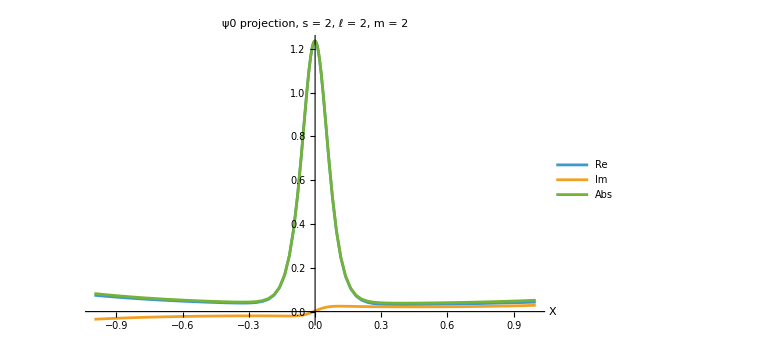

```mathematica
plotProjectedMode[ψm2,2,2,2]
```

```mathematica
ψm2["Data"]
```

```mathematica
plotProjectedMode[ψm2["Data"],+2,2]
```

Join::heads: Heads Missing[KeyAbsent,{2,2,Left}] and Missing[KeyAbsent,{2,2,Right}] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

-Graphics-

```mathematica
mUse=2
```

2

```mathematica
ellListPlus=Range[Max[Abs[mUse],2],15];
```

```mathematica
ClearAll[patchEdgeCheck];

patchEdgeCheck[res_Association,s_Integer,ell_Integer]:=Module[{left,right},left=getProjData[res,s,ell,"Left"];
right=getProjData[res,s,ell,"Right"];
<|"ell"->ell,"X left closest to 0"->Last[left["X"]],"Value left closest to 0"->Last[left["Values"]],"X right closest to 0"->First[right["X"]],"Value right closest to 0"->First[right["Values"]],"Jump estimate"->First[right["Values"]]-Last[left["Values"]],"Abs jump"->Abs[First[right["Values"]]-Last[left["Values"]]]|>];

Dataset[Table[patchEdgeCheck[resPlus,+2,ell],{ell,ellListPlus}]]
```

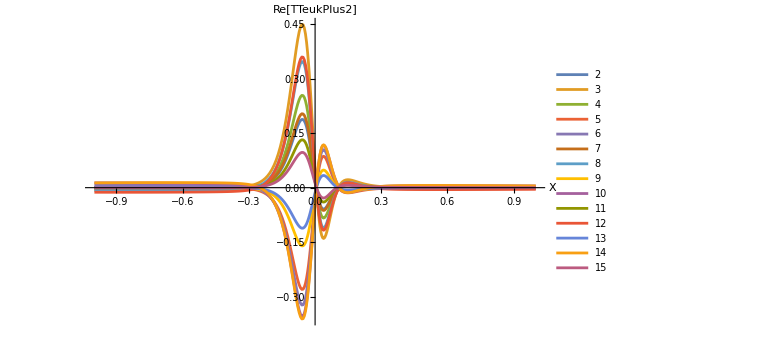

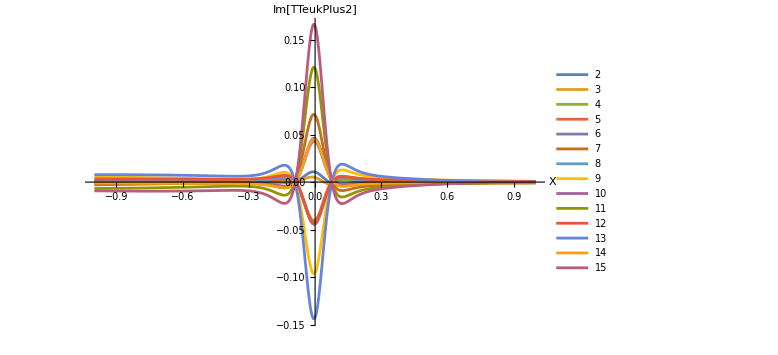

```mathematica
reCurvesPlus=Table[getJoinedProjData[resPlus,+2,ell]["ReData"],{ell,ellListPlus}];

imCurvesPlus=Table[getJoinedProjData[resPlus,+2,ell]["ImData"],{ell,ellListPlus}];

ListLinePlot[reCurvesPlus,PlotLegends->Placed[ellListPlus,Right],PlotRange->All,AxesLabel->{"X","Re[TTeukPlus2]"},ImageSize->Large]

ListLinePlot[imCurvesPlus,PlotLegends->Placed[ellListPlus,Right],PlotRange->All,AxesLabel->{"X","Im[TTeukPlus2]"},ImageSize->Large]
```

```mathematica
(* ============================================================*)(*Pull out and plot one projected Teukolsky source mode*)(* ============================================================*)ClearAll[projectionKeySummary,getProjectionEntry,getProjectionData,getJoinedProjectionData,plotProjectionEntry,plotProjectionMode,projectionEntryDataset];

projectionKeySummary[res_Association]:=Dataset[Table[<|"s"->key[[1]],"ell"->key[[2]],"Patch"->key[[3]]|>,{key,Keys[res]}]];

getProjectionEntry[res_Association,s_Integer,ell_Integer,patch_String]:=Module[{key},key={s,ell,patch};
If[!KeyExistsQ[res,key],Print["Missing key: ",key];
Print["Available keys are:"];
Print[Keys[res]];
Return[$Failed];];
res[key]];

getProjectionData[res_Association,s_Integer,ell_Integer,patch_String]:=Module[{entry,X,vals},entry=getProjectionEntry[res,s,ell,patch];
If[entry===$Failed,Return[$Failed]];
X=entry["XGrid"];
vals=entry["Values"];
<|"Entry"->entry,"X"->X,"Values"->vals,"ReData"->Transpose[{X,Re[vals]}],"ImData"->Transpose[{X,Im[vals]}],"AbsData"->Transpose[{X,Abs[vals]}]|>];

getJoinedProjectionData[res_Association,s_Integer,ell_Integer]:=Module[{left,right,X,vals,order},left=getProjectionData[res,s,ell,"Left"];
right=getProjectionData[res,s,ell,"Right"];
If[left===$Failed||right===$Failed,Return[$Failed]];
X=Join[left["X"],right["X"]];
vals=Join[left["Values"],right["Values"]];
order=Ordering[X];
<|"X"->X[[order]],"Values"->vals[[order]],"ReData"->Transpose[{X[[order]],Re[vals[[order]]]}],"ImData"->Transpose[{X[[order]],Im[vals[[order]]]}],"AbsData"->Transpose[{X[[order]],Abs[vals[[order]]]}]|>];

projectionEntryDataset[res_Association]:=Dataset@KeyValueMap[Function[{key,entry},<|"s"->key[[1]],"ell"->key[[2]],"Patch"->key[[3]],"m"->Lookup[entry,"m",Missing["No m"]],"nY"->Lookup[entry,"nY",Missing["No nY"]],"nX"->Length[entry["XGrid"]],"AllNumeric"->VectorQ[entry["Values"],NumericQ],"MaxAbs"->Max[Abs[entry["Values"]]],"MinAbs"->Min[Abs[entry["Values"]]]|>],res];
```

```mathematica
plotProjectionEntry[res_Association,s_Integer,ell_Integer,patch_String]:=Module[{data},data=getProjectionData[res,s,ell,patch];
If[data===$Failed,Return[$Failed]];
ListLinePlot[{data["ReData"],data["ImData"],data["AbsData"]},PlotLegends->{"Re","Im","Abs"},PlotRange->All,ImageSize->Large,AxesLabel->{"X","Projected source"},PlotLabel->Row[{"TTeuk, s = ",s,", ell = ",ell,", patch = ",patch}]]];
```

```mathematica
plotProjectionMode[res_Association,s_Integer,ell_Integer]:=Module[{data},data=getJoinedProjectionData[res,s,ell];
If[data===$Failed,Return[$Failed]];
ListLinePlot[{data["ReData"],data["ImData"],data["AbsData"]},PlotLegends->{"Re","Im","Abs"},PlotRange->All,ImageSize->Large,AxesLabel->{"X","Projected source"},PlotLabel->Row[{"TTeuk, s = ",s,", ell = ",ell,", m = ",mUse}]]];
```

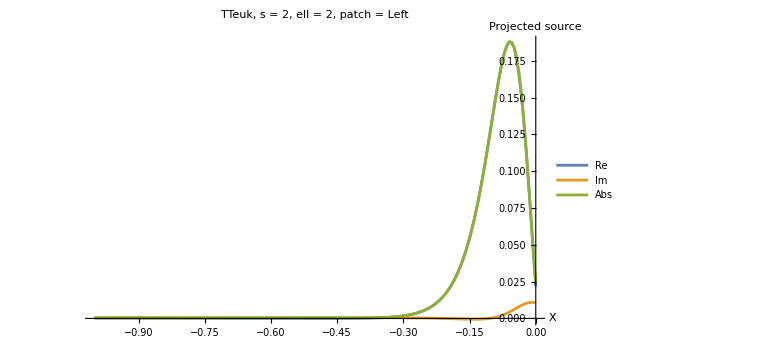

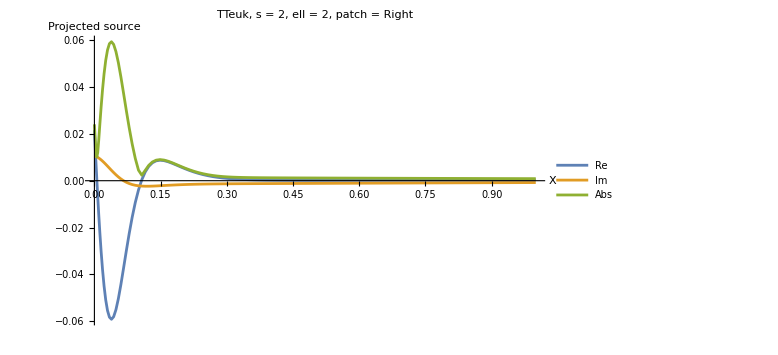

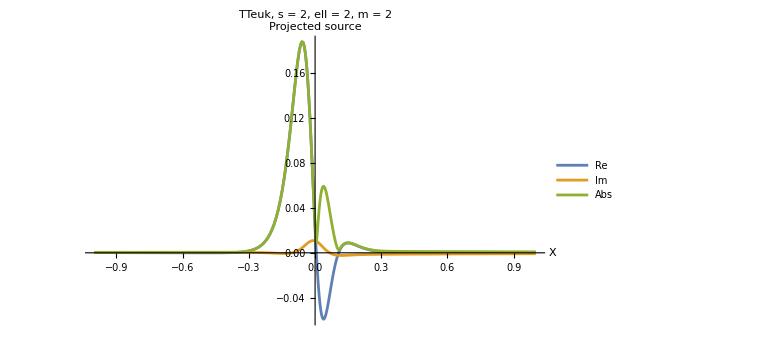

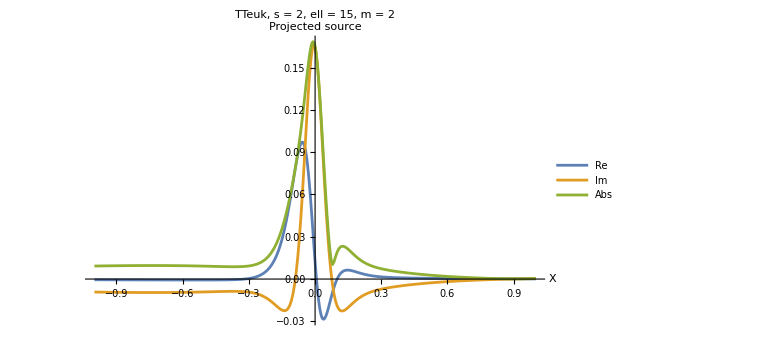

```mathematica
resPlus=plus2ProjectionResultsNX128;

projectionKeySummary[resPlus]

projectionEntryDataset[resPlus]

plotProjectionEntry[resPlus,+2,2,"Left"]

plotProjectionEntry[resPlus,+2,2,"Right"]

plotProjectionMode[resPlus,+2,2]

plotProjectionMode[resPlus,+2,15]
```

## C++ code Generator

```mathematica
ClearAll[componentIDs,patchIDs,yStorageIDs,magicBytes,hSFuncs,flattenComplexInterleaved,buildComponentMatrix,exportBinaryComponentFile,exportPatchBinaryFiles,exportTwoPatchModeBinaryFiles,flagBits,normalizeMetricSignature,buildFlags];

componentIDs=<|"ll"->0,"ln"->1,"lm"->2,"lmb"->3,"nn"->4,"nm"->5,"nmb"->6,"mm"->7,"mmb"->8, "mbmb"->9|>;

patchIDs=<|"left"->0,"right"->1|>;

yStorageIDs=<|"Full"->0,"HalfWithEvenReflection"->1|>;

magicBytes=Join[ToCharacterCode["GHZSRC1"],{0}];

(*flag bit masks*)
flagBits=<|"NegativeMIsConjugate"->1,(*bit 0*)"MostlyPlusSignature"->2    (*bit 1*)|>;

normalizeMetricSignature[s_]:=Which[s==="MostlyMinus"||s==="-+++"||s==="minus","MostlyMinus",s==="MostlyPlus"||s==="+---"||s==="plus","MostlyPlus",True,$Failed];

buildFlags[negM_,metricSig_]:=Module[{flags=0,sig=normalizeMetricSignature[metricSig]},If[sig===$Failed,Return[$Failed]];
If[TrueQ[negM],flags=BitOr[flags,flagBits["NegativeMIsConjugate"]]];
If[sig==="MostlyPlus",flags=BitOr[flags,flagBits["MostlyPlusSignature"]]];
flags];

teffFuncs=<|"ll"->hSll$MMode$XY$numeric,"ln"->hSln$MMode$XY$numeric,"lm"->hSlm$MMode$XY$numeric,"lmb"->hSlmb$MMode$XY$numeric,"nn"->hSnn$MMode$XY$numeric,"nm"->hSnm$MMode$XY$numeric,"nmb"->hSnmb$MMode$XY$numeric,"mm"->hSmm$MMode$XY$numeric,"mmb"->hSmmb$MMode$XY$numeric|>;

flattenComplexInterleaved[data_?MatrixQ]:=Flatten[({Re[#],Im[#]}&)/@Flatten[data]];

buildComponentMatrix[fun_,m_Integer?NonNegative,XGrid_List,YGrid_List]:=Table[fun[m][x,y],{x,XGrid},{y,YGrid}];

Options[exportBinaryComponentFile]={"YStorage"->"Full","NegativeMIsConjugate"->True,"MetricSignature"->"MostlyMinus"};

exportBinaryComponentFile[file_String,component_String,m_Integer?NonNegative,patch_String,XGrid_List,YGrid_List,data_?MatrixQ,rp_,B_,OptionsPattern[]]:=Module[{nx,ny,stream,flat,patchID,yStorageID,flags,metricSig},
nx=Length[XGrid];
ny=Length[YGrid];
If[!KeyExistsQ[componentIDs,component],Return[$Failed]];
If[!KeyExistsQ[patchIDs,patch],Return[$Failed]];
If[!KeyExistsQ[yStorageIDs,OptionValue["YStorage"]],Return[$Failed]];
If[Dimensions[data]=!={nx,ny},Print["Dimension mismatch in exportBinaryComponentFile for ",file];
Return[$Failed];];
metricSig=normalizeMetricSignature[OptionValue["MetricSignature"]];
If[metricSig===$Failed,Print["Invalid MetricSignature option in exportBinaryComponentFile for ",file];
Return[$Failed];];
patchID=patchIDs[patch];
yStorageID=yStorageIDs[OptionValue["YStorage"]];
flags=buildFlags[OptionValue["NegativeMIsConjugate"],metricSig];
If[flags===$Failed,Return[$Failed]];
flat=N15[flattenComplexInterleaved[data]];
stream=OpenWrite[file,BinaryFormat->True];
BinaryWrite[stream,magicBytes,"Byte"];
BinaryWrite[stream,1,"UnsignedInteger32"];(*layout unchanged*)BinaryWrite[stream,m,"Integer32"];
BinaryWrite[stream,componentIDs[component],"UnsignedInteger32"];
BinaryWrite[stream,patchID,"UnsignedInteger32"];
BinaryWrite[stream,yStorageID,"UnsignedInteger32"];
BinaryWrite[stream,flags,"UnsignedInteger32"];
BinaryWrite[stream,N15[rp],"Real64"];
BinaryWrite[stream,N15[B],"Real64"];
BinaryWrite[stream,nx,"UnsignedInteger64"];
BinaryWrite[stream,ny,"UnsignedInteger64"];
BinaryWrite[stream,N15[XGrid],"Real64"];
BinaryWrite[stream,N15[YGrid],"Real64"];
BinaryWrite[stream,flat,"Real64"];
Close[stream];
file];

Options[exportPatchBinaryFiles]={"Prefix"->"hS","YStorage"->"Full","NegativeMIsConjugate"->True,"MetricSignature"->"MostlyMinus","Verbose"->False};

exportPatchBinaryFiles[dir_String,m_Integer?NonNegative,patch_String,XGrid_List,YGrid_List,rp_,B_,OptionsPattern[]]:=Module[{prefix,yStorage,negm,metricSig,verbose,data,file},prefix=OptionValue["Prefix"];
yStorage=OptionValue["YStorage"];
negm=OptionValue["NegativeMIsConjugate"];
metricSig=OptionValue["MetricSignature"];
verbose=TrueQ[OptionValue["Verbose"]];
If[!MemberQ[{"left","right"},patch],Return[$Failed]];
CreateDirectory[dir,CreateIntermediateDirectories->True];
KeyValueMap[(If[verbose,Print["Writing ",#1,"  m=",m,"  patch=",patch,"  signature=",metricSig]];
data=buildComponentMatrix[#2,m,XGrid,YGrid];
file=FileNameJoin[{dir,StringTemplate["``_``_m``_``.bin"][prefix,#1,m,patch]}];
exportBinaryComponentFile[file,#1,m,patch,XGrid,YGrid,data,rp,B,"YStorage"->yStorage,"NegativeMIsConjugate"->negm,"MetricSignature"->metricSig])&,hSFuncs]];

Options[exportTwoPatchModeBinaryFiles]=Options[exportPatchBinaryFiles];

exportTwoPatchModeBinaryFiles[dir_String,m_Integer?NonNegative,XLeftGrid_List,XRightGrid_List,YGrid_List,rp_,B_,OptionsPattern[]]:=
Module[
{prefix,yStorage,negm,metricSig,verbose},
prefix=OptionValue["Prefix"];
yStorage=OptionValue["YStorage"];
negm=OptionValue["NegativeMIsConjugate"];
metricSig=OptionValue["MetricSignature"];
verbose=TrueQ[OptionValue["Verbose"]];
If[verbose,Print["=== Exporting mode m = ",m,"  signature=",metricSig," ==="]];
exportPatchBinaryFiles[dir,m,"left",XLeftGrid,YGrid,rp,B,"Prefix"->prefix,"YStorage"->yStorage,"NegativeMIsConjugate"->negm,"MetricSignature"->metricSig,"Verbose"->verbose];
exportPatchBinaryFiles[dir,m,"right",XRightGrid,YGrid,rp,B,"Prefix"->prefix,"YStorage"->yStorage,"NegativeMIsConjugate"->negm,"MetricSignature"->metricSig,"Verbose"->verbose];];
```

```mathematica
(* usage exportTwoPatchModeBinaryFiles[dir,m,XLeftGrid,XRightGrid,YGrid,rp,B,"MetricSignature"->"MostlyPlus","Verbose"->True] *)
```

```mathematica
YHalfGrid=YGrid[[1;;64]];
```

```mathematica
binaryDir[root_String]:=
FileNameJoin[{root,"hS_binary"<>spinTag[]}];
```

```mathematica
Do[exportTwoPatchModeBinaryFiles["hS_a0p0_WT_XYWindowed_Binary",m,XLeftGridProd,XRightGridProd,YHalfGrid,r0val,ℬ0val,"Prefix"->"hS","YStorage"->"HalfWithEvenReflection","NegativeMIsConjugate"->True,"MetricSignature"->"MostlyPlus","Verbose"->True],{m,0,20}];
```

=== Exporting mode m = 0  signature=MostlyPlus ===

Writing ll  m=0  patch=left  signature=MostlyPlus

$Aborted

```mathematica
hSSymbols={hSll$MMode$XY$numeric,hSln$MMode$XY$numeric,hSlm$MMode$XY$numeric,hSlmb$MMode$XY$numeric,hSnn$MMode$XY$numeric,hSnm$MMode$XY$numeric,hSnmb$MMode$XY$numeric,hSmm$MMode$XY$numeric,hSmmb$MMode$XY$numeric};

generatorSymbols={componentIDs,patchIDs,yStorageIDs,magicBytes,hSFuncs,flattenComplexInterleaved,buildComponentMatrix,exportBinaryComponentFile,exportPatchBinaryFiles,exportTwoPatchModeBinaryFiles};Save["hSsymbolic.wl",hSSymbols];
Save["hSBinaryGenerator.wl",generatorSymbols];
```

```mathematica
DumpSave["hSSources.mx",{hSll$MMode$XY$numeric,hSln$MMode$XY$numeric,hSlm$MMode$XY$numeric,hSlmb$MMode$XY$numeric,hSnn$MMode$XY$numeric,hSnm$MMode$XY$numeric,hSnmb$MMode$XY$numeric,hSmm$MMode$XY$numeric,hSmmb$MMode$XY$numeric}]
```

```mathematica
{hSll$MMode$XY$numeric,hSln$MMode$XY$numeric,hSlm$MMode$XY$numeric,hSlmb$MMode$XY$numeric,hSnn$MMode$XY$numeric,hSnm$MMode$XY$numeric,hSnmb$MMode$XY$numeric,hSmm$MMode$XY$numeric,hSmmb$MMode$XY$numeric}
```

```mathematica
Save["hSBinaryGenerator.wl",{componentIDs,patchIDs,yStorageIDs,magicBytes,hSFuncs,flattenComplexInterleaved,buildComponentMatrix,exportBinaryComponentFile,exportPatchBinaryFiles,exportTwoPatchModeBinaryFiles}]
```

```mathematica
Save["hSBinaryGeneratorWithSources.wl",{componentIDs,patchIDs,yStorageIDs,magicBytes,teffFuncs,flattenComplexInterleaved,buildComponentMatrix,exportBinaryComponentFile,exportPatchBinaryFiles,exportTwoPatchModeBinaryFiles,hSll$MMode$XY$numeric,hSln$MMode$XY$numeric,hSlm$MMode$XY$numeric,hSlmb$MMode$XY$numeric,hSnn$MMode$XY$numeric,hSnm$MMode$XY$numeric,hSnmb$MMode$XY$numeric,hSmm$MMode$XY$numeric,hSmmb$MMode$XY$numeric}]
```

```mathematica
(* ============================================================*)(*Read/write one saved IRG grid file*)(* ============================================================*)ClearAll[readIRGGridFile,writeIRGGridFile];

readIRGGridFile[file_String]:=Module[{obj},If[!FileExistsQ[file],Print["Missing file: ",file];
Return[$Failed]];
Clear[IRGhSGridData,teffGridCache];
Get[file];
obj=Which[ValueQ[IRGhSGridData]&&AssociationQ[IRGhSGridData],IRGhSGridData,ValueQ[teffGridCache]&&AssociationQ[teffGridCache],teffGridCache,True,Print["Could not find saved association in file: ",file];
$Failed];
Clear[IRGhSGridData,teffGridCache];
obj];

writeIRGGridFile[file_String,obj_Association]:=Module[{},Clear[IRGhSGridData];
IRGhSGridData=obj;
DumpSave[file,IRGhSGridData];
Clear[IRGhSGridData];
file];
```